```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/henry/Dropbox/EFT_analytical/Henry_work

## Halo kernels in real and redshift space

Final output of this section are the halo kernels in redshift space

### Perturbation Theory Kernels

```mathematica
perm12=Permutations[{q1,q2}];
perm123=Permutations[{q1,q2,q3}];
perm1234=Permutations[{q1,q2,q3,q4}];
```

```mathematica
Clear[Fn,Gn,n,m];
Fn[n_,v_]=If[n==1,1,Sum[Gn[m,v[[1;;m]]]/((2n+3)(n-1))((2n+1)al[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Fn[n-m,v[[m+1;;n]]]+2be[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Gn[n-m,v[[m+1;;n]]]),{m,1,n-1}]];
Gn[n_,v_]=If[n==1,1,Sum[Gn[m,v[[1;;m]]]/((2n+3)(n-1))(3al[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Fn[n-m,v[[m+1;;n]]]+2n be[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Gn[n-m,v[[m+1;;n]]]),{m,1,n-1}]];
```

```mathematica
F2[q1_,q2_]=Simplify[Sum[1/Length[perm12]Fn[2,{perm12[[i,1]],perm12[[i,2]]}],{i,1,Length[perm12]}]];
F3[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123]Fn[3,{perm123[[i,1]],perm123[[i,2]],perm123[[i,3]]}],{i,1,Length[perm123]}]];
F4[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234]Fn[4,{perm1234[[i,1]],perm1234[[i,2]],perm1234[[i,3]],perm1234[[i,4]]}],{i,1,Length[perm1234]}]]; 
G2[q1_,q2_]=Simplify[Sum[1/Length[perm12]Gn[2,{perm12[[i,1]],perm12[[i,2]]}],{i,1,Length[perm12]}]];
G3[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123]Gn[3,{perm123[[i,1]],perm123[[i,2]],perm123[[i,3]]}],{i,1,Length[perm123]}]];
G4[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234]Gn[4,{perm1234[[i,1]],perm1234[[i,2]],perm1234[[i,3]],perm1234[[i,4]]}],{i,1,Length[perm1234]}]];
```

```mathematica
alf[k1_,k2_]=(k1+k2).k1/(k1.k1);
bef[k1_,k2_]=(k1+k2).(k1+k2)(k1.k2)/2/(k1.k1)/(k2.k2) ;
alfm[k1_,k2_]=1+1/2(mag[k1+k2]^2-mag[k1]^2-mag[k2]^2)/mag[k1]^2;
befm[k1_,k2_]=(mag[k1+k2]^2(mag[k1+k2]^2-mag[k1]^2-mag[k2]^2))/(4 mag[k1]^2 mag[k2]^2);
```

### Define C_i Kernels and bare bias coefficients

initialize bare bias c_i values

```mathematica
c4 = Table[0,{i,1,15}];
```

```mathematica
c4[[1]]=Subscript["(ĉ)^(4)","δ,1"];
c4[[2]]=Subscript["(ĉ)^(4)","δ,2"];
c4[[3]]=Subscript["(ĉ)^(4)","δ,3"];
c4[[4]]=Subscript["(ĉ)^(4)","δ,4"];
c4[[5]]=Subscript["(ĉ)^(4)","δ^2,1"];
c4[[6]]=Subscript["(ĉ)^(4)","δ^2,2"];
c4[[7]]=Subscript["(ĉ)^(4)","δ^2,3"];
c4[[8]]=Subscript["(ĉ)^(4)","r^2,2"];
c4[[9]]=Subscript["(ĉ)^(4)","r^2,3"];
c4[[10]]=Subscript["(ĉ)^(4)","δ^3,1"];
c4[[11]]=Subscript["(ĉ)^(4)","δ^3,2"];
c4[[12]]=Subscript["(ĉ)^(4)","r^3,2"];
c4[[13]]=Subscript["(ĉ)^(4)","r^2δ,2"];
c4[[14]]=Subscript["(ĉ)^(4)","δ^4,1"];
c4[[15]]=Subscript["(ĉ)^(4)","δr^3,1"];
```

```mathematica
c3=c4//.{"(ĉ)^(4)"-> "(ĉ)^(3)"};
c2=c4//.{"(ĉ)^(4)"-> "(ĉ)^(2)"};
c1=c4//.{"(ĉ)^(4)"-> "(ĉ)^(1)"};
adelta = c4//.{"(ĉ)^(4)"-> "(c̃)^A"};
```

```mathematica
btheta={1,2,3,4,-1,-3/2,-2,0,0,1,4/3,0,0,-1,0};
```

Expressions for C_i kernels

```mathematica
For[i=1,i<16,i++,c1[[i]][q1_]:=0;]
For[i=1,i<16,i++,c2[[i]][q1_,q2_]:=0;]
For[i=1,i<16,i++,c3[[i]][q1_,q2_,q3_]:=0;]
```

```mathematica
c1[[1]][q1_]:=1;
c2[[1]][q1_,q2_]:=-(mag[q1]^2+mag[q2]^2-mag[q1+q2]^2)/(2 mag[q1]^2);
c2[[2]][q1_,q2_]:=((1+2 F2[q1,q2]) mag[q1]^2+mag[q2]^2-mag[q1+q2]^2)/(2 mag[q1]^2);
c2[[5]][q1_,q2_]:=1;
c3[[1]][q1_,q2_,q3_]:=1/8 (-1/mag[q2+q3]^2 2 G2[q2,q3] (2 mag[q1]^2+mag[q2]^2-mag[q1+q2]^2+mag[q3]^2-mag[q1+q3]^2)+((mag[q1]^2+mag[q2]^2-mag[q1+q2]^2) (mag[q1]^2+mag[q2]^2+2 mag[q3]^2-mag[q1+q3]^2-mag[q2+q3]^2))/(mag[q2]^2 mag[q3]^2));
c3[[2]][q1_,q2_,q3_]:=-(((mag[q1]^2+(1+2 F2[q1,q2]) mag[q2]^2-mag[q1+q2]^2) (mag[q1]^2+mag[q2]^2+2 mag[q3]^2-mag[q1+q3]^2-mag[q2+q3]^2))/(4 mag[q2]^2 mag[q3]^2));
c3[[3]][q1_,q2_,q3_]:=1/8 ((2 G2[q2,q3] (mag[q1]^2+mag[q2+q3]^2-mag[q1+q2+q3]^2))/mag[q2+q3]^2+1/(mag[q2]^2 mag[q3]^2)(mag[q1]^2 (mag[q1+q2]^2+mag[q3]^2-mag[q1+q2+q3]^2)-mag[q1+q2]^2 (mag[q1+q2]^2+mag[q3]^2-mag[q1+q2+q3]^2)+mag[q2]^2 ((1+4 F2[q1,q2]) mag[q1+q2]^2+(1+4 F2[q1,q2]+8 F3[q1,q2,q3]) mag[q3]^2-(1+4 F2[q1,q2]) mag[q1+q2+q3]^2)));c3[[5]][q1_,q2_,q3_]:=-(mag[q2]^2+mag[q3]^2-mag[q2+q3]^2)/mag[q3]^2;
c3[[6]][q1_,q2_,q3_]:=2 F2[q1,q2]+(mag[q2]^2+mag[q3]^2-mag[q2+q3]^2)/mag[q3]^2;
c3[[8]][q1_,q2_,q3_]:=1/(4 mag[q1]^2 mag[q2]^2 mag[q1+q2]^2 mag[q3]^2)(mag[q1]^4 mag[q1+q2]^2 (mag[q2]^2+mag[q3]^2-mag[q2+q3]^2)+(-mag[q2]^2 mag[q1+q2]+mag[q1+q2]^3)^2 (mag[q2]^2+mag[q3]^2-mag[q2+q3]^2)+2 mag[q1]^2 (mag[q2]^4 mag[q1+q2]^2+mag[q1+q2]^4 (-mag[q3]^2+mag[q2+q3]^2)+mag[q2]^2 ((-1+F2[q1,q2]) mag[q1+q2]^4+F2[q1,q2] (mag[q3]^2-mag[q1+q2+q3]^2)^2+mag[q1+q2]^2 ((1+2 F2[q1,q2]) mag[q3]^2-mag[q2+q3]^2-2 F2[q1,q2] mag[q1+q2+q3]^2))));
c3[[10]][q1_,q2_,q3_]:=1;
```

```mathematica
c4[[1]][q1_,q2_,q3_,q4_]:=1/48 (1/(mag[q2]^2 mag[q3+q4]^2)2 G2[q3,q4] (mag[q1]^2+mag[q2]^2-mag[q1+q2]^2) (3 mag[q1]^2+2 mag[q2]^2+5 mag[q3+q4]^2-3 mag[q1+q3+q4]^2-2 mag[q2+q3+q4]^2)+1/(mag[q2]^2 mag[q3]^2 mag[q2+q3]^2 mag[q4]^2)(-mag[q1]^6 mag[q2+q3]^2-mag[q2]^6 mag[q2+q3]^2+mag[q2]^4 mag[q2+q3]^2 (mag[q1+q2]^2-2 mag[q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)+mag[q1]^4 mag[q2+q3]^2 (-mag[q2]^2+mag[q1+q2]^2-4 mag[q3]^2+mag[q1+q3]^2-4 mag[q4]^2+mag[q1+q4]^2+3 mag[q3+q4]^2)+mag[q1+q2]^2 mag[q2+q3]^2 (4 mag[q3]^4+mag[q2+q3]^2 (-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)+mag[q1+q3]^2 (-4 mag[q4]^2+mag[q1+q4]^2+3 mag[q3+q4]^2)-mag[q3]^2 (3 mag[q1+q3]^2+mag[q2+q3]^2-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2))+mag[q1]^2 (-mag[q2]^4 mag[q2+q3]^2+mag[q2+q3]^2 (-4 mag[q3]^4+4 mag[q1+q3]^2 mag[q4]^2+2 mag[q2+q3]^2 mag[q4]^2-mag[q1+q3]^2 mag[q1+q4]^2-mag[q2+q3]^2 mag[q2+q4]^2-3 mag[q1+q3]^2 mag[q3+q4]^2-mag[q2+q3]^2 mag[q3+q4]^2+mag[q1+q2]^2 (4 mag[q3]^2-mag[q1+q3]^2+4 mag[q4]^2-mag[q1+q4]^2-3 mag[q3+q4]^2)+mag[q3]^2 (3 mag[q1+q3]^2+mag[q2+q3]^2-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2))+mag[q2]^2 (mag[q2+q3]^2 (mag[q1+q3]^2+mag[q2+q3]^2-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2)+2 mag[q3]^2 ((-3+G2[q2,q3]) mag[q2+q3]^2+G2[q2,q3] (mag[q4]^2-mag[q2+q3+q4]^2))))+mag[q2]^2 (-4 mag[q3]^4 mag[q2+q3]^2+mag[q1+q3]^2 mag[q2+q3]^2 (4 mag[q4]^2-mag[q1+q4]^2-3 mag[q3+q4]^2)+mag[q2+q3]^4 (2 mag[q4]^2-mag[q2+q4]^2-mag[q3+q4]^2)-mag[q1+q2]^2 mag[q2+q3]^2 (-2 mag[q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)+mag[q3]^2 (3 mag[q1+q3]^2 mag[q2+q3]^2+(1+2 G2[q2,q3]) mag[q2+q3]^4+2 G2[q2,q3] mag[q1+q2+q3]^2 (-mag[q4]^2+mag[q2+q3+q4]^2)+mag[q2+q3]^2 (-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2-2 G2[q2,q3] (mag[q1+q2+q3]^2-mag[q4]^2+mag[q2+q3+q4]^2)))))-(8 G3[q2,q3,q4] (mag[q1]^2+mag[q2+q3+q4]^2-mag[q1+q2+q3+q4]^2))/mag[q2+q3+q4]^2);
c4[[2]][q1_,q2_,q3_,q4_]:=-1/(16 mag[q2]^2)(1/(mag[q3]^2 mag[q4]^2)(-mag[q1]^6-mag[q2]^6+mag[q2]^4 (mag[q1+q2]^2-2 mag[q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)+mag[q1]^4 (-mag[q2]^2+mag[q1+q2]^2-4 mag[q3]^2+mag[q1+q3]^2-4 mag[q4]^2+mag[q1+q4]^2+3 mag[q3+q4]^2)-mag[q2]^2 (4 mag[q3]^4-3 mag[q3]^2 mag[q1+q3]^2-mag[q3]^2 mag[q2+q3]^2+6 mag[q3]^2 mag[q4]^2-4 mag[q1+q3]^2 mag[q4]^2-2 mag[q2+q3]^2 mag[q4]^2-mag[q3]^2 mag[q1+q4]^2+mag[q1+q3]^2 mag[q1+q4]^2-mag[q3]^2 mag[q2+q4]^2+mag[q2+q3]^2 mag[q2+q4]^2-4 mag[q3]^2 mag[q3+q4]^2+3 mag[q1+q3]^2 mag[q3+q4]^2+mag[q2+q3]^2 mag[q3+q4]^2+2 F2[q1,q2] (mag[q1+q2]^2+mag[q3]^2-mag[q1+q2+q3]^2) (mag[q1+q2]^2+mag[q3]^2+2 mag[q4]^2-mag[q1+q2+q4]^2-mag[q3+q4]^2)+mag[q1+q2]^2 (-2 mag[q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2))+mag[q1]^2 (-mag[q2]^4-4 mag[q3]^4+3 mag[q3]^2 mag[q1+q3]^2+mag[q3]^2 mag[q2+q3]^2-6 mag[q3]^2 mag[q4]^2+4 mag[q1+q3]^2 mag[q4]^2+2 mag[q2+q3]^2 mag[q4]^2+mag[q3]^2 mag[q1+q4]^2-mag[q1+q3]^2 mag[q1+q4]^2+mag[q3]^2 mag[q2+q4]^2-mag[q2+q3]^2 mag[q2+q4]^2+4 mag[q3]^2 mag[q3+q4]^2-3 mag[q1+q3]^2 mag[q3+q4]^2-mag[q2+q3]^2 mag[q3+q4]^2+mag[q1+q2]^2 (4 mag[q3]^2-mag[q1+q3]^2+4 mag[q4]^2-mag[q1+q4]^2-3 mag[q3+q4]^2)+mag[q2]^2 (-6 mag[q3]^2+mag[q1+q3]^2+mag[q2+q3]^2-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2))+mag[q1+q2]^2 (4 mag[q3]^4+mag[q2+q3]^2 (-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)+mag[q1+q3]^2 (-4 mag[q4]^2+mag[q1+q4]^2+3 mag[q3+q4]^2)-mag[q3]^2 (3 mag[q1+q3]^2+mag[q2+q3]^2-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2)))+1/mag[q3+q4]^2 2 G2[q3,q4] (mag[q1]^4+mag[q2]^4+mag[q1]^2 (2 mag[q2]^2-mag[q1+q2]^2+2 mag[q3+q4]^2-mag[q1+q3+q4]^2-mag[q2+q3+q4]^2)+mag[q1+q2]^2 (-2 mag[q3+q4]^2+mag[q1+q3+q4]^2+mag[q2+q3+q4]^2)+mag[q2]^2 ((-1+2 F2[q1,q2]) mag[q1+q2]^2+2 (1+F2[q1,q2]) mag[q3+q4]^2-mag[q1+q3+q4]^2-mag[q2+q3+q4]^2-2 F2[q1,q2] mag[q1+q2+q3+q4]^2)));
c4[[3]][q1_,q2_,q3_,q4_]:=1/(16 mag[q2]^2)(-1/mag[q3+q4]^2 2 G2[q3,q4] (mag[q1]^2+mag[q2]^2-mag[q1+q2]^2) (mag[q1]^2+mag[q3+q4]^2-mag[q1+q3+q4]^2)+1/(mag[q3]^2 mag[q2+q3]^2 mag[q4]^2)(-mag[q1]^6 mag[q2+q3]^2-mag[q2]^6 mag[q2+q3]^2+mag[q2]^4 mag[q2+q3]^2 (mag[q1+q2]^2-2 mag[q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)+mag[q1]^4 mag[q2+q3]^2 (-mag[q2]^2+mag[q1+q2]^2-4 mag[q3]^2+mag[q1+q3]^2-4 mag[q4]^2+mag[q1+q4]^2+3 mag[q3+q4]^2)+mag[q1+q2]^2 mag[q2+q3]^2 (4 mag[q3]^4+mag[q2+q3]^2 (-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)+mag[q1+q3]^2 (-4 mag[q4]^2+mag[q1+q4]^2+3 mag[q3+q4]^2)-mag[q3]^2 (3 mag[q1+q3]^2+mag[q2+q3]^2-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2))+mag[q1]^2 (-mag[q2]^4 mag[q2+q3]^2+mag[q2+q3]^2 (-4 mag[q3]^4+4 mag[q1+q3]^2 mag[q4]^2+2 mag[q2+q3]^2 mag[q4]^2-mag[q1+q3]^2 mag[q1+q4]^2-mag[q2+q3]^2 mag[q2+q4]^2-3 mag[q1+q3]^2 mag[q3+q4]^2-mag[q2+q3]^2 mag[q3+q4]^2+mag[q1+q2]^2 (4 mag[q3]^2-mag[q1+q3]^2+4 mag[q4]^2-mag[q1+q4]^2-3 mag[q3+q4]^2)+mag[q3]^2 (3 mag[q1+q3]^2+mag[q2+q3]^2-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2))+mag[q2]^2 (mag[q2+q3]^2 (mag[q1+q3]^2+mag[q2+q3]^2-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2)-2 mag[q3]^2 ((3+G2[q2,q3]) mag[q2+q3]^2+G2[q2,q3] (mag[q4]^2-mag[q2+q3+q4]^2))))-mag[q2]^2 (4 mag[q3]^4 mag[q2+q3]^2-3 mag[q3]^2 mag[q1+q3]^2 mag[q2+q3]^2-mag[q3]^2 mag[q2+q3]^4+2 G2[q2,q3] mag[q3]^2 mag[q2+q3]^4+8 F3[q1,q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q1+q2+q3]^2-2 G2[q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q1+q2+q3]^2+6 mag[q3]^2 mag[q2+q3]^2 mag[q4]^2+8 F3[q1,q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q4]^2+2 G2[q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q4]^2-4 mag[q1+q3]^2 mag[q2+q3]^2 mag[q4]^2-2 mag[q2+q3]^4 mag[q4]^2-2 G2[q2,q3] mag[q3]^2 mag[q1+q2+q3]^2 mag[q4]^2-mag[q3]^2 mag[q2+q3]^2 mag[q1+q4]^2+mag[q1+q3]^2 mag[q2+q3]^2 mag[q1+q4]^2-mag[q3]^2 mag[q2+q3]^2 mag[q2+q4]^2+mag[q2+q3]^4 mag[q2+q4]^2-4 mag[q3]^2 mag[q2+q3]^2 mag[q3+q4]^2+3 mag[q1+q3]^2 mag[q2+q3]^2 mag[q3+q4]^2+mag[q2+q3]^4 mag[q3+q4]^2+4 F2[q1,q2] mag[q2+q3]^2 (mag[q1+q2]^2+mag[q3]^2-mag[q1+q2+q3]^2) (mag[q1+q2]^2+mag[q3]^2+2 mag[q4]^2-mag[q1+q2+q4]^2-mag[q3+q4]^2)+mag[q1+q2]^2 mag[q2+q3]^2 (-2 mag[q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)-2 G2[q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q2+q3+q4]^2+2 G2[q2,q3] mag[q3]^2 mag[q1+q2+q3]^2 mag[q2+q3+q4]^2-8 F3[q1,q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q1+q2+q3+q4]^2)));
c4[[4]][q1_,q2_,q3_,q4_]:=1/48 ((8 G3[q2,q3,q4] (mag[q1]^2+mag[q2+q3+q4]^2-mag[q1+q2+q3+q4]^2))/mag[q2+q3+q4]^2+1/(mag[q2]^2 mag[q3+q4]^2)2 G2[q3,q4] (3 mag[q1]^4+mag[q2]^4+mag[q1]^2 (4 mag[q2]^2-3 mag[q1+q2]^2+4 mag[q3+q4]^2-3 mag[q1+q3+q4]^2-mag[q2+q3+q4]^2)+mag[q1+q2]^2 (-4 mag[q3+q4]^2+3 mag[q1+q3+q4]^2+mag[q2+q3+q4]^2)+mag[q2]^2 ((-1+6 F2[q1,q2]) mag[q1+q2]^2+(4+6 F2[q1,q2]) mag[q3+q4]^2-3 mag[q1+q3+q4]^2-mag[q2+q3+q4]^2-6 F2[q1,q2] mag[q1+q2+q3+q4]^2))+1/(mag[q2]^2 mag[q3]^2 mag[q2+q3]^2 mag[q4]^2)(mag[q1]^6 mag[q2+q3]^2+mag[q2]^6 mag[q2+q3]^2+mag[q1]^4 mag[q2+q3]^2 (mag[q2]^2-mag[q1+q2]^2+4 mag[q3]^2-mag[q1+q3]^2+4 mag[q4]^2-mag[q1+q4]^2-3 mag[q3+q4]^2)-mag[q2]^4 mag[q2+q3]^2 (mag[q1+q2]^2-2 mag[q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)+mag[q1+q2]^2 mag[q2+q3]^2 (-4 mag[q3]^4+mag[q1+q3]^2 (4 mag[q4]^2-mag[q1+q4]^2-3 mag[q3+q4]^2)+mag[q2+q3]^2 (2 mag[q4]^2-mag[q2+q4]^2-mag[q3+q4]^2)+mag[q3]^2 (3 mag[q1+q3]^2+mag[q2+q3]^2-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2))+mag[q1]^2 (mag[q2]^4 mag[q2+q3]^2+mag[q2+q3]^2 (4 mag[q3]^4-4 mag[q1+q3]^2 mag[q4]^2-2 mag[q2+q3]^2 mag[q4]^2+mag[q1+q3]^2 mag[q1+q4]^2+mag[q2+q3]^2 mag[q2+q4]^2+3 mag[q1+q3]^2 mag[q3+q4]^2+mag[q2+q3]^2 mag[q3+q4]^2+mag[q1+q2]^2 (-4 mag[q3]^2+mag[q1+q3]^2-4 mag[q4]^2+mag[q1+q4]^2+3 mag[q3+q4]^2)-mag[q3]^2 (3 mag[q1+q3]^2+mag[q2+q3]^2-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2))+mag[q2]^2 (-mag[q2+q3]^2 (mag[q1+q3]^2+mag[q2+q3]^2-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2)+mag[q3]^2 ((6+4 G2[q2,q3]) mag[q2+q3]^2+4 G2[q2,q3] (mag[q4]^2-mag[q2+q3+q4]^2))))+mag[q2]^2 (4 mag[q3]^4 mag[q2+q3]^2-3 mag[q3]^2 mag[q1+q3]^2 mag[q2+q3]^2-mag[q3]^2 mag[q2+q3]^4+4 G2[q2,q3] mag[q3]^2 mag[q2+q3]^4+24 F3[q1,q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q1+q2+q3]^2-4 G2[q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q1+q2+q3]^2+6 mag[q3]^2 mag[q2+q3]^2 mag[q4]^2+24 F3[q1,q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q4]^2+48 F4[q1,q2,q3,q4] mag[q3]^2 mag[q2+q3]^2 mag[q4]^2+4 G2[q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q4]^2-4 mag[q1+q3]^2 mag[q2+q3]^2 mag[q4]^2-2 mag[q2+q3]^4 mag[q4]^2-4 G2[q2,q3] mag[q3]^2 mag[q1+q2+q3]^2 mag[q4]^2-mag[q3]^2 mag[q2+q3]^2 mag[q1+q4]^2+mag[q1+q3]^2 mag[q2+q3]^2 mag[q1+q4]^2-mag[q3]^2 mag[q2+q3]^2 mag[q2+q4]^2+mag[q2+q3]^4 mag[q2+q4]^2-4 mag[q3]^2 mag[q2+q3]^2 mag[q3+q4]^2+3 mag[q1+q3]^2 mag[q2+q3]^2 mag[q3+q4]^2+mag[q2+q3]^4 mag[q3+q4]^2+6 F2[q1,q2] mag[q2+q3]^2 (mag[q1+q2]^2+mag[q3]^2-mag[q1+q2+q3]^2) (mag[q1+q2]^2+mag[q3]^2+2 mag[q4]^2-mag[q1+q2+q4]^2-mag[q3+q4]^2)+mag[q1+q2]^2 mag[q2+q3]^2 (-2 mag[q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)-4 G2[q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q2+q3+q4]^2+4 G2[q2,q3] mag[q3]^2 mag[q1+q2+q3]^2 mag[q2+q3+q4]^2-24 F3[q1,q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q1+q2+q3+q4]^2)));
c4[[5]][q1_,q2_,q3_,q4_]:=1/4 (1/(mag[q3]^2 mag[q4]^2)(mag[q2]^4+mag[q3]^4-mag[q3]^2 mag[q2+q3]^2+3 mag[q3]^2 mag[q4]^2-mag[q1+q3]^2 mag[q4]^2-2 mag[q2+q3]^2 mag[q4]^2-2 mag[q3]^2 mag[q2+q4]^2+mag[q1+q3]^2 mag[q2+q4]^2+mag[q2+q3]^2 mag[q2+q4]^2+mag[q1]^2 (mag[q2]^2+mag[q4]^2-mag[q2+q4]^2)-mag[q3]^2 mag[q3+q4]^2+mag[q2+q3]^2 mag[q3+q4]^2+mag[q2]^2 (3 mag[q3]^2-mag[q1+q3]^2-mag[q2+q3]^2+2 mag[q4]^2-mag[q2+q4]^2-mag[q3+q4]^2))-1/mag[q3+q4]^2 2 G2[q3,q4] (mag[q2]^2+mag[q3+q4]^2-mag[q2+q3+q4]^2));
c4[[6]][q1_,q2_,q3_,q4_]:=-1/(2 mag[q3]^2 mag[q4]^2)(mag[q2]^4+mag[q3]^4+2 F2[q1,q2] mag[q3]^4-mag[q3]^2 mag[q2+q3]^2+2 F2[q2,q3] mag[q3]^2 mag[q2+q3]^2+3 mag[q3]^2 mag[q4]^2+2 F2[q1,q2] mag[q3]^2 mag[q4]^2+2 F2[q2,q3] mag[q3]^2 mag[q4]^2-mag[q1+q3]^2 mag[q4]^2-2 mag[q2+q3]^2 mag[q4]^2-2 mag[q3]^2 mag[q2+q4]^2+mag[q1+q3]^2 mag[q2+q4]^2+mag[q2+q3]^2 mag[q2+q4]^2+mag[q1]^2 (mag[q2]^2+mag[q4]^2-mag[q2+q4]^2)-mag[q3]^2 mag[q3+q4]^2-2 F2[q1,q2] mag[q3]^2 mag[q3+q4]^2+mag[q2+q3]^2 mag[q3+q4]^2-mag[q2]^2 (-3 mag[q3]^2+mag[q1+q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)-2 F2[q2,q3] mag[q3]^2 mag[q2+q3+q4]^2);
c4[[7]][q1_,q2_,q3_,q4_]:=1/4 (1/mag[q4]^2 4 F2[q1,q2] (mag[q3]^2+(1+F2[q3,q4]) mag[q4]^2-mag[q3+q4]^2)+1/mag[q3+q4]^2 2 G2[q3,q4] (mag[q2]^2+mag[q3+q4]^2-mag[q2+q3+q4]^2)+1/(mag[q3]^2 mag[q4]^2)(mag[q2]^4+mag[q3]^4-mag[q3]^2 mag[q2+q3]^2+4 F2[q2,q3] mag[q3]^2 mag[q2+q3]^2+3 mag[q3]^2 mag[q4]^2+4 F2[q2,q3] mag[q3]^2 mag[q4]^2+8 F3[q1,q2,q3] mag[q3]^2 mag[q4]^2-mag[q1+q3]^2 mag[q4]^2-2 mag[q2+q3]^2 mag[q4]^2-2 mag[q3]^2 mag[q2+q4]^2+mag[q1+q3]^2 mag[q2+q4]^2+mag[q2+q3]^2 mag[q2+q4]^2+mag[q1]^2 (mag[q2]^2+mag[q4]^2-mag[q2+q4]^2)-mag[q3]^2 mag[q3+q4]^2+mag[q2+q3]^2 mag[q3+q4]^2+mag[q2]^2 (3 mag[q3]^2-mag[q1+q3]^2-mag[q2+q3]^2+2 mag[q4]^2-mag[q2+q4]^2-mag[q3+q4]^2)-4 F2[q2,q3] mag[q3]^2 mag[q2+q3+q4]^2));
c4[[8]][q1_,q2_,q3_,q4_]:=(-mag[q1]^6 mag[q1+q2]^2 mag[q2+q3]^2 (mag[q2]^2+mag[q4]^2-mag[q2+q4]^2)+mag[q1+q2]^2 (-mag[q2]^8 mag[q2+q3]^2+mag[q2]^6 mag[q2+q3]^2 (2 mag[q1+q2]^2-3 mag[q3]^2+mag[q1+q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)-mag[q2]^4 mag[q2+q3]^2 (mag[q1+q2]^4+mag[q3]^4-mag[q1+q3]^2 mag[q4]^2-2 mag[q2+q3]^2 mag[q4]^2+mag[q1+q3]^2 mag[q2+q4]^2+mag[q2+q3]^2 mag[q2+q4]^2+mag[q2+q3]^2 mag[q3+q4]^2+2 mag[q1+q2]^2 (-3 mag[q3]^2+mag[q1+q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)-mag[q3]^2 (mag[q2+q3]^2-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2))+mag[q1+q2]^4 mag[q2+q3]^2 (-mag[q3]^4+mag[q1+q3]^2 (mag[q4]^2-mag[q2+q4]^2)+mag[q2+q3]^2 (2 mag[q4]^2-mag[q2+q4]^2-mag[q3+q4]^2)+mag[q3]^2 (mag[q2+q3]^2-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2))+mag[q2]^2 (mag[q1+q2]^4 mag[q2+q3]^2 (-3 mag[q3]^2+mag[q1+q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)+2 mag[q1+q2]^2 mag[q2+q3]^2 (mag[q3]^4+mag[q1+q3]^2 (-mag[q4]^2+mag[q2+q4]^2)+mag[q2+q3]^2 (-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)-mag[q3]^2 (mag[q2+q3]^2-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2))-2 F2[q2,q3] mag[q3]^2 (mag[q2+q3]^2-mag[q1+q2+q3]^2)^2 (mag[q2+q3]^2+mag[q4]^2-mag[q2+q3+q4]^2)))+mag[q1]^4 mag[q1+q2]^2 (-3 mag[q2]^4 mag[q2+q3]^2+mag[q2+q3]^2 (-mag[q3]^4+mag[q1+q3]^2 mag[q4]^2+2 mag[q2+q3]^2 mag[q4]^2-mag[q1+q3]^2 mag[q2+q4]^2-mag[q2+q3]^2 mag[q2+q4]^2+2 mag[q1+q2]^2 (mag[q4]^2-mag[q2+q4]^2)-mag[q2+q3]^2 mag[q3+q4]^2+mag[q3]^2 (mag[q2+q3]^2-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2))+mag[q2]^2 (2 mag[q1+q2]^2 mag[q2+q3]^2+mag[q2+q3]^2 (mag[q1+q3]^2+mag[q2+q3]^2-4 mag[q4]^2+3 mag[q2+q4]^2+mag[q3+q4]^2)-mag[q3]^2 ((3+2 F2[q2,q3]) mag[q2+q3]^2+2 F2[q2,q3] (mag[q4]^2-mag[q2+q3+q4]^2))))-mag[q1]^2 (3 mag[q2]^6 mag[q1+q2]^2 mag[q2+q3]^2-mag[q2]^4 mag[q1+q2]^2 mag[q2+q3]^2 (4 mag[q1+q2]^2-6 mag[q3]^2+2 mag[q1+q3]^2+2 mag[q2+q3]^2-5 mag[q4]^2+3 mag[q2+q4]^2+2 mag[q3+q4]^2)+mag[q1+q2]^4 mag[q2+q3]^2 (-2 mag[q3]^4+2 mag[q1+q3]^2 mag[q4]^2+4 mag[q2+q3]^2 mag[q4]^2-2 mag[q1+q3]^2 mag[q2+q4]^2-2 mag[q2+q3]^2 mag[q2+q4]^2+mag[q1+q2]^2 (mag[q4]^2-mag[q2+q4]^2)-2 mag[q2+q3]^2 mag[q3+q4]^2+2 mag[q3]^2 (mag[q2+q3]^2-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2))+mag[q2]^2 (mag[q1+q2]^6 mag[q2+q3]^2+2 F2[q1,q2] mag[q2+q3]^2 (mag[q3]^2-mag[q1+q2+q3]^2)^2 (mag[q3]^2+mag[q4]^2-mag[q3+q4]^2)+2 mag[q1+q2]^4 mag[q2+q3]^2 ((-3+F2[q1,q2]) mag[q3]^2+mag[q1+q3]^2+mag[q2+q3]^2-3 mag[q4]^2+F2[q1,q2] mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2-F2[q1,q2] mag[q3+q4]^2)+2 mag[q1+q2]^2 ((1+2 F2[q1,q2]) mag[q3]^4 mag[q2+q3]^2+mag[q2+q3]^2 (mag[q1+q3]^2 (-mag[q4]^2+mag[q2+q4]^2)+2 F2[q1,q2] mag[q1+q2+q3]^2 (-mag[q4]^2+mag[q3+q4]^2)+mag[q2+q3]^2 (-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2))+mag[q3]^2 ((-1+2 F2[q2,q3]) mag[q2+q3]^4+2 F2[q2,q3] mag[q1+q2+q3]^2 (-mag[q4]^2+mag[q2+q3+q4]^2)-mag[q2+q3]^2 (-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2+2 F2[q1,q2] (mag[q1+q2+q3]^2-mag[q4]^2+mag[q3+q4]^2)+2 F2[q2,q3] (mag[q1+q2+q3]^2-mag[q4]^2+mag[q2+q3+q4]^2)))))))/(8 mag[q1]^2 mag[q2]^2 mag[q1+q2]^2 mag[q3]^2 mag[q2+q3]^2 mag[q4]^2);
c4[[9]][q1_,q2_,q3_,q4_]:=1/16 ((2 G2[q3,q4] (mag[q1]^2+mag[q2]^2-mag[q1+q2]^2)^2 (mag[q2]^2+mag[q3+q4]^2-mag[q2+q3+q4]^2))/(mag[q1]^2 mag[q2]^2 mag[q3+q4]^2)+1/mag[q1+q2]^2 4 F2[q1,q2] (((mag[q1+q2]^2+mag[q3]^2-mag[q1+q2+q3]^2)^2 (mag[q3]^2+mag[q4]^2-mag[q3+q4]^2))/(mag[q3]^2 mag[q4]^2)+1/mag[q3+q4]^2 F2[q3,q4] (mag[q1+q2]^2+mag[q3+q4]^2-mag[q1+q2+q3+q4]^2)^2)+(mag[q1]^6 mag[q2+q3]^2 mag[q1+q2+q3]^2 (mag[q2]^2+mag[q4]^2-mag[q2+q4]^2)+mag[q1+q2+q3]^2 (mag[q2]^8 mag[q2+q3]^2-mag[q2]^6 mag[q2+q3]^2 (2 mag[q1+q2]^2-3 mag[q3]^2+mag[q1+q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)+mag[q1+q2]^4 mag[q2+q3]^2 (mag[q3]^4+mag[q1+q3]^2 (-mag[q4]^2+mag[q2+q4]^2)+mag[q2+q3]^2 (-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)-mag[q3]^2 (mag[q2+q3]^2-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2))+mag[q2]^4 mag[q2+q3]^2 (mag[q1+q2]^4+mag[q3]^4-mag[q1+q3]^2 mag[q4]^2-2 mag[q2+q3]^2 mag[q4]^2+mag[q1+q3]^2 mag[q2+q4]^2+mag[q2+q3]^2 mag[q2+q4]^2+mag[q2+q3]^2 mag[q3+q4]^2+2 mag[q1+q2]^2 (-3 mag[q3]^2+mag[q1+q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)-mag[q3]^2 (mag[q2+q3]^2-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2))+mag[q2]^2 (-mag[q1+q2]^4 mag[q2+q3]^2 (-3 mag[q3]^2+mag[q1+q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)-2 mag[q1+q2]^2 mag[q2+q3]^2 (mag[q3]^4+mag[q1+q3]^2 (-mag[q4]^2+mag[q2+q4]^2)+mag[q2+q3]^2 (-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)-mag[q3]^2 (mag[q2+q3]^2-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2))+4 F2[q2,q3] mag[q3]^2 (mag[q2+q3]^2-mag[q1+q2+q3]^2)^2 (mag[q2+q3]^2+mag[q4]^2-mag[q2+q3+q4]^2)))+mag[q1]^4 mag[q1+q2+q3]^2 (3 mag[q2]^4 mag[q2+q3]^2+mag[q2+q3]^2 (mag[q3]^4-mag[q1+q3]^2 mag[q4]^2-2 mag[q2+q3]^2 mag[q4]^2+mag[q1+q3]^2 mag[q2+q4]^2+mag[q2+q3]^2 mag[q2+q4]^2-2 mag[q1+q2]^2 (mag[q4]^2-mag[q2+q4]^2)+mag[q2+q3]^2 mag[q3+q4]^2-mag[q3]^2 (mag[q2+q3]^2-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2))-mag[q2]^2 (2 mag[q1+q2]^2 mag[q2+q3]^2+mag[q2+q3]^2 (mag[q1+q3]^2+mag[q2+q3]^2-4 mag[q4]^2+3 mag[q2+q4]^2+mag[q3+q4]^2)-mag[q3]^2 ((3+4 F2[q2,q3]) mag[q2+q3]^2+4 F2[q2,q3] (mag[q4]^2-mag[q2+q3+q4]^2))))+mag[q1]^2 (3 mag[q2]^6 mag[q2+q3]^2 mag[q1+q2+q3]^2-mag[q2]^4 mag[q2+q3]^2 mag[q1+q2+q3]^2 (4 mag[q1+q2]^2-6 mag[q3]^2+2 mag[q1+q3]^2+2 mag[q2+q3]^2-5 mag[q4]^2+3 mag[q2+q4]^2+2 mag[q3+q4]^2)+mag[q1+q2]^2 mag[q2+q3]^2 mag[q1+q2+q3]^2 (-2 mag[q3]^4+2 mag[q1+q3]^2 mag[q4]^2+4 mag[q2+q3]^2 mag[q4]^2-2 mag[q1+q3]^2 mag[q2+q4]^2-2 mag[q2+q3]^2 mag[q2+q4]^2+mag[q1+q2]^2 (mag[q4]^2-mag[q2+q4]^2)-2 mag[q2+q3]^2 mag[q3+q4]^2+2 mag[q3]^2 (mag[q2+q3]^2-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2))+mag[q2]^2 (mag[q1+q2]^4 mag[q2+q3]^2 mag[q1+q2+q3]^2+2 mag[q1+q2]^2 mag[q2+q3]^2 mag[q1+q2+q3]^2 (-3 mag[q3]^2+mag[q1+q3]^2+mag[q2+q3]^2-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2)+2 (mag[q3]^4 mag[q2+q3]^2 mag[q1+q2+q3]^2+mag[q2+q3]^2 mag[q1+q2+q3]^2 (mag[q1+q3]^2 (-mag[q4]^2+mag[q2+q4]^2)+mag[q2+q3]^2 (-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2))+mag[q3]^2 ((-1+4 F2[q2,q3]) mag[q2+q3]^4 mag[q1+q2+q3]^2+4 F2[q2,q3] mag[q1+q2+q3]^4 (-mag[q4]^2+mag[q2+q3+q4]^2)+mag[q2+q3]^2 (mag[q1+q2+q3]^2 (3 mag[q4]^2-2 mag[q2+q4]^2-mag[q3+q4]^2)-4 F2[q2,q3] mag[q1+q2+q3]^2 (mag[q1+q2+q3]^2-mag[q4]^2+mag[q2+q3+q4]^2)+4 F3[q1,q2,q3] (mag[q1+q2+q3]^2+mag[q4]^2-mag[q1+q2+q3+q4]^2)^2))))))/(mag[q1]^2 mag[q2]^2 mag[q3]^2 mag[q2+q3]^2 mag[q1+q2+q3]^2 mag[q4]^2));
c4[[10]][q1_,q2_,q3_,q4_]:=-(3 (mag[q3]^2+mag[q4]^2-mag[q3+q4]^2))/(2 mag[q4]^2);
c4[[11]][q1_,q2_,q3_,q4_]:=(3 (mag[q3]^2+(1+2 F2[q1,q2]) mag[q4]^2-mag[q3+q4]^2))/(2 mag[q4]^2);
c4[[12]][q1_,q2_,q3_,q4_]:=-((3 (mag[q1]^4 mag[q1+q2]^2 (mag[q2]^2+mag[q3]^2-mag[q2+q3]^2)+mag[q1+q2]^2 (mag[q2]^2-mag[q1+q2]^2) (mag[q3]^2-mag[q1+q3]^2) (mag[q2]^2+mag[q3]^2-mag[q2+q3]^2)+mag[q1]^2 (mag[q2]^4 mag[q1+q2]^2-mag[q1+q2]^2 (mag[q1+q2]^2-mag[q3]^2+mag[q1+q3]^2) (mag[q3]^2-mag[q2+q3]^2)+mag[q2]^2 ((-1+2 F2[q1,q2]) mag[q1+q2]^4+2 F2[q1,q2] (mag[q3]^2-mag[q1+q2+q3]^2) (mag[q4]^2-mag[q1+q2+q4]^2)+mag[q1+q2]^2 (2 (1+F2[q1,q2]) mag[q3]^2-mag[q1+q3]^2-mag[q2+q3]^2-2 F2[q1,q2] mag[q1+q2+q3]^2+2 F2[q1,q2] mag[q4]^2-2 F2[q1,q2] mag[q1+q2+q4]^2)))) (mag[q3]^2+mag[q4]^2-mag[q3+q4]^2))/(16 mag[q1]^2 mag[q2]^2 mag[q1+q2]^2 mag[q3]^2 mag[q4]^2));
c4[[13]][q1_,q2_,q3_,q4_]:=1/(8 mag[q1]^2 mag[q2]^2 mag[q1+q2]^2 mag[q3]^2 mag[q4]^2)(mag[q1]^4 mag[q1+q2]^2 mag[q3]^2 (mag[q3]^2+(1+2 F2[q3,q4]) mag[q4]^2-mag[q3+q4]^2)+mag[q1+q2]^2 (mag[q2]^2-mag[q1+q2]^2)^2 mag[q3]^2 (mag[q3]^2+(1+2 F2[q3,q4]) mag[q4]^2-mag[q3+q4]^2)+2 mag[q1]^2 (mag[q2]^4 mag[q1+q2]^2 (mag[q3]^2+mag[q4]^2-mag[q3+q4]^2)+mag[q1+q2]^2 (mag[q3]^2-mag[q2+q3]^2)^2 (mag[q3]^2+mag[q4]^2-mag[q3+q4]^2)-mag[q1+q2]^4 mag[q3]^2 (mag[q3]^2+(1+2 F2[q3,q4]) mag[q4]^2-mag[q3+q4]^2)+mag[q2]^2 (2 F2[q1,q2] mag[q1+q2]^4 mag[q4]^2+2 F2[q1,q2] (mag[q3]^2-mag[q1+q2+q3]^2)^2 mag[q4]^2+mag[q1+q2]^2 (3 mag[q3]^4-2 mag[q2+q3]^2 mag[q4]^2-4 F2[q1,q2] mag[q1+q2+q3]^2 mag[q4]^2+2 mag[q2+q3]^2 mag[q3+q4]^2+mag[q3]^2 (-2 mag[q2+q3]^2+(3+4 F2[q1,q2]+2 F2[q3,q4]) mag[q4]^2-3 mag[q3+q4]^2)))));
c4[[14]][q1_,q2_,q3_,q4_]:=1;
c4[[15]][q1_,q2_,q3_,q4_]:=-(((mag[q1]^2+mag[q2]^2-mag[q1+q2]^2) (mag[q1]^2+mag[q3]^2-mag[q1+q3]^2) (mag[q2]^2+mag[q3]^2-mag[q2+q3]^2))/(8 mag[q1]^2 mag[q2]^2 mag[q3]^2));
```

### Preliminaries

Coordinate choices. Here we take k1 along the third axis. q is the integration vector. z is the line of sight, angles are chosen such that k1.z = μ

```mathematica
Clear[zhat];
coordchoice={k1->{0,0,kk1},k2->kk2{0,√(1-y^2),y},k3->{0,-kk2 √(1-y^2),-kk1-kk2 y},q->qq{√(1-x^2)Cos[β],√(1-x^2) Sin[β],x}(*q->qq{√(1-x^2)α,√(1-x^2) √(1-α^2),x}*)};zhat1=zhat->{√(1-μ^2)Cos[ϕ],√(1-μ^2)Sin[ϕ], μ};zhat2=zhat->{Sin[θ] Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
```

```mathematica
ysub={y->(k3^2-k1^2-k2^2)/(2 k1 k2)};
```

This is zhat with angles w.r.t. the normal of the triangle, and check with Yankelevich-Porciani. 0<ω<π, 0<χ<2π

```mathematica
zhatnorm=zhat->{Cos[ω],-Sin[ω]Cos[χ],Sin[ω]Sin[χ]};
```

```mathematica
k1.zhat/.coordchoice/.zhatnorm
```

kk1 Sin[χ] Sin[ω]

```mathematica
Assuming[{ξ12>0,ξ12<π},k2.zhat/.coordchoice/.zhatnorm/.y->Cos[ξ12]//FullSimplify]
```

-kk2 Sin[ξ12-χ] Sin[ω]

```mathematica
k3.zhat/.coordchoice/.zhatnorm//FullSimplify
```

(kk2 √(1-y^2) Cos[χ]-(kk1+kk2 y) Sin[χ]) Sin[ω]

```mathematica
q.zhat/.coordchoice/.zhatnorm//FullSimplify
```

qq (√(1-x^2) Cos[β] Cos[ω]+(-√(1-x^2) Cos[χ] Sin[β]+x Sin[χ]) Sin[ω])

Definitions of magnitudes, which are needed to expand the kernels and PS

```mathematica
kmq[k1] = k1mq;
kmq[k2] = k2mq;
kmq[k3] = k3mq;
kpq[k1] = k1pq;
kpq[k2] = k2pq;
kpq[k3] = k3pq;
```

```mathematica
yrep = {y->(-k1^2-k2^2+k3^2)/(2 k1 k2)};
```

```mathematica
magreps ={mag[-q]->q,mag[q]->q,mag[k1]->k1,mag[k2]->k2,mag[k3]->k3,mag[-k1]->k1,mag[-k2]->k2,mag[-k1-k2]->k3,mag[k1+k2]->k3,mag[-k1+q]->k1mq,mag[k1-q]->k1mq,mag[-k1-q]->k1pq,mag[k1+q]->k1pq,mag[-k2+q]->k2mq,mag[k2-q]->k2mq,mag[-k2-q]->k2pq,mag[k2+q]->k2pq,mag[-k1-k2-q]->k3mq,mag[k1+k2+q]->k3mq,mag[-k1-k2+q]->k3pq,mag[k1+k2-q]->k3pq,mag[-k3]->k3,mag[-k1-k3]->k2,mag[k1+k3]->k2,mag[-k3+q]->k3mq,mag[k3-q]->k3mq,mag[-k3-q]->k3pq,mag[k3+q]->k3pq,mag[-k1-k3-q]->k2mq,mag[k1+k3+q]->k2mq,mag[-k1-k3+q]->k2pq,mag[k1+k3-q]->k2pq,mag[-k2-k3]->k1,mag[k2+k3]->k1,mag[-k2-k3-q]->k1mq,mag[k2+k3+q]->k1mq,mag[-k2-k3+q]->k1pq,mag[k2+k3-q]->k1pq,
mag[-q1]->q1,mag[q1]->q1,mag[-q-q1]->qpq1,mag[q-q1]->qmq1,mag[-q+q1]->qmq1,mag[q+q1]->qpq1};
```

```mathematica
magrevreps  = {k1mq-> √(k1^2+q^2-2 k1 q x),k1pq-> √(k1^2+q^2+2 k1 q x),k2mq-> √(k2^2+q^2-2 k2 q (x y+√(1-x^2) √(1-y^2) Sin[β])),k2pq-> √(k2^2+q^2+2 k2 q (x y+√(1-x^2) √(1-y^2) Sin[β])),k3mq-> √(k3^2+q^2+2k1 q x+2k2 q x y+2k2 q √(1-x^2) √(1-y^2) Sin[β]),k3pq-> √(k3^2+q^2-2k1 q x-2k2 q x y-2k2 q √(1-x^2) √(1-y^2) Sin[β]),
qmq1-> √(q^2+q1^2-2ν q q1),qpq1-> √(q^2+q1^2+2ν q q1)};
```

Check magrevreps

```mathematica
Simplify[{(k1-q).(k1-q),(k1+q).(k1+q),(k2-q).(k2-q),(k2+q).(k2+q),(k3-q).(k3-q),(k3+q).(k3+q)}/.coordchoice]/.{kk1^2+kk2^2->kk3^2-2 kk1 kk2 y}//Simplify
```

{kk1^2+qq^2-2 kk1 qq x,kk1^2+qq^2+2 kk1 qq x,kk2^2+qq^2-2 kk2 qq x y-2 kk2 qq √(1-x^2) √(1-y^2) Sin[β],kk2^2+qq^2+2 kk2 qq x y+2 kk2 qq √(1-x^2) √(1-y^2) Sin[β],kk3^2+qq (qq+2 x (kk1+kk2 y))+2 kk2 qq √(1-x^2) √(1-y^2) Sin[β],kk3^2+qq (qq-2 x (kk1+kk2 y))-2 kk2 qq √(1-x^2) √(1-y^2) Sin[β]}

define line of sight angle. Note that for now we keep μ3 and intermediary also define μ0, which we will substitute later.
Try to integrate over μ and ϕ to get the monopole!

```mathematica
kzsub = {Subscript[k1, z]-> k1 μ1,Subscript[k2, z]-> k2 μ2,Subscript[q, z]-> q μ0,Subscript[k3, z]->k3 μ3};
```

```mathematica
μtoangles1=Assuming[{y>-1,y<1,μ>-1,μ<1,ϕ>0,ϕ<2π,x>-1,x<1},{μ1->(k1.zhat)/kk1,μ2->(k2.zhat)/kk2,μ3->(k3.zhat)/kk3,μ0->(q.zhat)/qq}/.coordchoice/.zhat1//FullSimplify]
```

{μ1→μ,μ2→y μ+√((-1+y^2) (-1+μ^2)) Sin[ϕ],μ3→-(kk1 μ+kk2 y μ+kk2 √((-1+y^2) (-1+μ^2)) Sin[ϕ])/kk3,μ0→x μ+√((-1+x^2) (-1+μ^2)) Cos[β-ϕ]}

```mathematica
μtoangles2=Assuming[{y>-1,y<1,μ>-1,μ<1,ϕ>0,ϕ<2π,x>-1,x<1},{μ1->(k1.zhat)/kk1,μ2->(k2.zhat)/kk2,μ3->(k3.zhat)/kk3,μ0->(q.zhat)/qq}/.coordchoice/.zhat2]
```

{μ1→Cos[θ],μ2→(kk2 y Cos[θ]+kk2 √(1-y^2) Sin[θ] Sin[ϕ])/kk2,μ3→((-kk1-kk2 y) Cos[θ]-kk2 √(1-y^2) Sin[θ] Sin[ϕ])/kk3,μ0→(qq x Cos[θ]+qq √(1-x^2) Cos[β] Cos[ϕ] Sin[θ]+qq √(1-x^2) Sin[β] Sin[θ] Sin[ϕ])/qq}

```mathematica
μtoanglesnorm=Assuming[{y>-1,y<1,ω>0,ω<π,χ>0,χ<2π,x>-1,x<1},{μ1->(k1.zhat)/kk1,μ2->(k2.zhat)/kk2,μ3->(k3.zhat)/kk3,μ0->(q.zhat)/qq}/.coordchoice/.zhatnorm//FullSimplify]
```

{μ1→Sin[χ] Sin[ω],μ2→(-√(1-y^2) Cos[χ]+y Sin[χ]) Sin[ω],μ3→((kk2 √(1-y^2) Cos[χ]-(kk1+kk2 y) Sin[χ]) Sin[ω])/kk3,μ0→√(1-x^2) Cos[β] Cos[ω]+(-√(1-x^2) Cos[χ] Sin[β]+x Sin[χ]) Sin[ω]}

```mathematica
μtoangles3=Assuming[{k1q∈Reals,qq>0,kk1>0,kk2>0,y>-1,y<1},{μ1->Cos[θ],μ2->y Cos[θ]+√(1-y^2) Sin[θ] Sin[ϕ],μ3->-((kk1+kk2 y) Cos[θ]+kk2 √(1-y^2) Sin[θ] Sin[ϕ])/kk3,μ0->x Cos[θ]+√(1-x^2) Cos[β-ϕ] Sin[θ]}/.x->k1q/(kk1 qq)//FullSimplify]
```

{μ1→Cos[θ],μ2→y Cos[θ]+√(1-y^2) Sin[θ] Sin[ϕ],μ3→-((kk1+kk2 y) Cos[θ]+kk2 √(1-y^2) Sin[θ] Sin[ϕ])/kk3,μ0→(k1q Cos[θ])/(kk1 qq)+√(1-k1q^2/(kk1^2 qq^2)) Cos[β-ϕ] Sin[θ]}

```mathematica
q.k2/.coordchoice
```

kk2 qq x y+kk2 qq √(1-x^2) √(1-y^2) Sin[β]

define symmetrization over two and three variables

```mathematica
q2sym[f_,q1_,q2_]:=1/2(f[q1,q2]+f[q2,q1]);
q3sym[f_,q1_,q2_,q3_]:=Total[(f@@@Permutations[{q1,q2,q3}])/(3!)];
q4sym[f_,q1_,q2_,q3_,q4_]:=Total[(f@@@Permutations[{q1,q2,q3,q4}])/(4!)]
```

define final bias coefficients

```mathematica
tb={adelta[[1]]-> b1,adelta[[2]]-> b2,adelta[[3]]-> b3,adelta[[4]]-> b4,adelta[[5]]-> b5,adelta[[6]]->b6,adelta[[7]]->b7-15/2 adelta[[13]],adelta[[8]]-> b8,adelta[[9]]-> b9,adelta[[10]]-> b10,adelta[[12]]-> b11};
tbrev  = {b1-> adelta[[1]],b2-> adelta[[2]],b3-> adelta[[3]],b4-> adelta[[4]],b5-> adelta[[5]],b6-> adelta[[6]],b7-> adelta[[7]]+15/2 adelta[[13]],b8-> adelta[[8]],b9-> adelta[[9]],b10-> adelta[[10]],b11-> adelta[[12]]};
biases = {b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11};
```

Projections on matter and velocity (as a special species of biased tracer)

```mathematica
submat=Thread[biases->{1,1,1,1,0,0,0,0,0,0,0}]
subvel=Thread[biases->{1,2,3,4,-1,-3/2,-2,0,0,1,0}]
```

{b1→1,b2→1,b3→1,b4→1,b5→0,b6→0,b7→0,b8→0,b9→0,b10→0,b11→0}

{b1→1,b2→2,b3→3,b4→4,b5→-1,b6→-3/2,b7→-2,b8→0,b9→0,b10→1,b11→0}

```mathematica
finduv[func_,n_]:=Series[func,{q,∞,n}]//Normal;
findir[func_,n_]:=Series[func,{q,0,n}]//Normal;
```

Here we only keep μ0, and leave μ1 and μ2, μ3 to the coefficients of each FFTLog integral

```mathematica
μlistfinal  = Table[μ0^i,{i,0,6}];
μlistfinalno1 = Delete[μlistfinal,1];
```

```mathematica
μlister[ker_]:=
Join[{ker},Monitor[Table[Coefficient[ker,μlistfinalno1⟦i⟧],{i,1,Length[μlistfinalno1]}],i]]/.{μ0-> 0}
```

Adds up the different contributions from the tabs, for instance {{0,0,0,a},{0,0,0,b}}→ {0,0,0,a+b}.

```mathematica
positionDuplicates[list_]:=GatherBy[Range@Length[list],list⟦#⟧&];
```

```mathematica
compressor[tab_] := Module[{tab1,tab2},
tab1 = positionDuplicates[Table[Delete[tab⟦i⟧,4],{i,1,Length[tab]}]];
tab2 = Monitor[Table[{tab⟦tab1⟦j,1⟧⟧⟦{1,2,3}⟧,
Sum[tab⟦tab1⟦j,i⟧⟧⟦4⟧,{i,1,Length[tab1⟦j⟧]}]}//Flatten,{j,1,Length[tab1]}],j*100.0/Length[tab1]]]
```

```mathematica
comp[tab_]:=Table[compressor[tab⟦i⟧],{i,1,7}]
```

Replacements
Notice that we modify μ0 as well!
the replacements q→ -q, q→ k1pq and q→ k2mq  have the following coding:
k1mk2=|k1-k2+q|,
k12pq = |2k1+q|,
k22mq = |2k2-q|,
kspeck1 = |2k1+k2+q|,
kspeck2 = |k1+2k2+q|

```mathematica
preqtok1pq= Thread[{q,k1pq, k1mq, k2pq, k2mq, k3pq, k3mq,μ0}-> {k1pqt,k12pq,qt,k3mqt,k1mk2,k2mqt,kspeck1,μ0t}];
preqtok2mq = Thread[{q,k1pq, k1mq, k2pq, k2mq, k3pq, k3mq,μ0}-> {k2mqt,k3pqt,k1mk2,k22mq,qt,k1pqt,kspeck2,μ0t}];
qtok1pq = Thread[ {k1pqt,k12pq,qt,k3mqt,k1mk2,k2mqt,kspeck1,μ0t}-> {k1pq,√(2 k1^2+2 k1pq^2-q^2),q,k3mq,√(k1^2+k1pq^2+k2^2+k2mq^2-k3^2-q^2),k2mq,√(2 k1pq^2-k2mq^2+2 k3^2),(q μ0+k1 μ1)/k1pq}];
qtok2mq = Thread[ {k2mqt,k3pqt,k1mk2,k22mq,qt,k1pqt,kspeck2,μ0t}->{k2mq,k3pq,√(k1^2+k1pq^2+k2^2+k2mq^2-k3^2-q^2),√(2 k2^2+2 k2mq^2-q^2),q,k1pq,√(-2 k1^2+k1pq^2+4 k2^2-2 k2mq^2+2 k3^2+2 q^2),(-q μ0+k2 μ2)/k2mq} ];
restrep = Thread[{k1mq,k2pq,k3mq,k3pq}-> {√(2 k1^2-k1pq^2+2 q^2),√(2 k2^2-k2mq^2+2 q^2),√(-k1^2+k1pq^2+k2^2-k2mq^2+k3^2+q^2),√(k1^2-k1pq^2-k2^2+k2mq^2+k3^2+q^2)}];
```

```mathematica
qrev1={k1mq->k1pqt,k1pq->k1mqt,k2mq->k2pqt,k2pq->k2mqt,k3mq->k3pqt,k3pq->k3mqt,μ0-> μ0t};
qrev2={k1mqt->k1mq,k1pqt->k1pq,k2mqt->k2mq,k2pqt->k2pq,k3mqt->k3mq,k3pqt->k3pq,μ0t-> -μ0};
```

Tests

Tabtester checks that all terms of the expression were listed in terms of the exponents of the master integral and coefficients. It passed if all is 0

```mathematica
(*Tabtester[final_,tab_]:=Table[final⟦j⟧-Sum[q^(-2tab⟦j,i,1⟧)k1pq^(-2tab⟦j,i,2⟧)k2mq^(-2tab⟦j,i,3⟧)*tab⟦j,i,4⟧,{i,1,Length[tab⟦j⟧]}]//Expand,{j,1,7}];*)
```

```mathematica
Tabtester[final_,tab_]:=Table[final-q^(-2tab⟦i,1⟧)k1pq^(-2tab⟦i,2⟧)k2mq^(-2tab⟦i,3⟧)*tab⟦i,4⟧,{i,1,Length[tab]}]//Expand;
```

Tabtester2 checks that the coefficients are only composed of f1, k1, k2, k3, Linear powerspectra without q dependence,μ1 and μ2, biases and numbers. It passed if the result is {1}

```mathematica
(*Tabtester2[tab_]:=Table[Table[tab⟦j,i⟧,{i,1,Length[tab⟦j⟧]}]//Expand,{j,1,7}]/.Thread[{ν,ν1,ν2}-> 1]/.{f1->1,k1->1,k2->1,k3->1,μ1->1,μ2->1,μ3->1}/.Thread[biases-> 1]/._Rational-> 1/._Integer-> 1//Flatten//DeleteDuplicates;*)
Tabtester2[tab_]:=Table[tab⟦i⟧,{i,1,Length[tab]}]//Expand/.Thread[{ν,ν1,ν2}-> 1]/.{f1->1,k1->1,k2->1,k3->1,μ1->1,μ2->1,μ3->1}/.Thread[biases-> 1]/._Rational-> 1/._Integer-> 1//Flatten//DeleteDuplicates;
```

### Halo Kernels (real space)

```mathematica
K1[aa_]:=aa⟦1⟧;
K2[q1_,q2_,aa_]:=K2[q1,q2,aa]=((Table[c2⟦i⟧[q1,q2],{i,1,15}]/.{al->alfm,be->befm}/.{mag[-q]->mag[q]}/.magreps//Expand)/.mag[0]-> 0//Simplify).aa;
K3[q1_,q2_,q3_,aa_]:=K3[q1,q2,q3,aa]=((Table[c3⟦i⟧[q1,q2,q3],{i,1,15}]/.{al->alfm,be->befm}/.{mag[-q]->mag[q]}/.magreps//Expand)/.mag[0]-> 0//Simplify).aa;
K4[q1_,q2_,q3_,q4_,aa_]:=K4[q1,q2,q3,q4,aa]=((Monitor[Table[q4sym[c4⟦i⟧,q1,q2,q3,q4]/.{al->alfm,be->befm}/.magreps//Simplify,{i,1,15}],i])/.mag[0]-> 0).aa;
```

Check the <δ(2)> which has to be subtracted

```mathematica
δ2vev=K2[q1,-q1,adelta]/.tb
```

-b1+b2+b5

### Halo Kernels (real space for delta)

```mathematica
K1d[q1_]:=K1[adelta]//.{kz-> q1.zhat}//.Dot[a_,a_]-> mag[a]^2/.{Dot[a_,zhat]-> Subscript[a, z]}/.magreps//.kzsub;
K2d[q1_,q2_]:=K2[q1,q2,adelta]/.{al->alfm,be->befm}/.Dot[a_,a_]-> mag[a]^2/.mag[-q]->mag[q]/.{kz-> (q1+q2).zhat}/.magreps//.Dot[a_+b_,c_]-> Dot[a,c]+Dot[b,c]/.{Dot[-a_,b_]-> -Dot[a,b]}/.{Dot[a_,zhat]-> Subscript[a, z]}//.kzsub;
K2dsym[q1_,q2_]:=q2sym[K2d,q1,q2];
K3d[q1_,q2_,q3_]:=K3[q1,q2,q3,adelta]/.Dot[a_,a_]-> mag[a]^2/.mag[-q]->mag[q]/.magreps/.{kz-> (q1+q2+q3).zhat}//.Dot[a_+b_,c_]-> Dot[a,c]+Dot[b,c]/.{Dot[-a_,b_]-> -Dot[a,b]}/.{Dot[a_,zhat]-> Subscript[a, z]}//.kzsub;
K3dsym[q1_,q2_,q3_] := q3sym[K3d,q1,q2,q3];
K4d[q1_,q2_,q3_,q4_]:=K4[q1,q2,q3,q4,adelta]/.Dot[a_,a_]-> mag[a]^2/.mag[-q]->mag[q]/.{kz-> (q1+q2+q3+q4).zhat}/.magreps//.Dot[a_+b_,c_]-> Dot[a,c]+Dot[b,c]/.{Dot[-a_,b_]-> -Dot[a,b]}/.{Dot[a_,zhat]-> Subscript[a, z]}//.kzsub;
K4dsym[q1_,q2_,q3_,q4_]:=q4sym[K4d,q1,q2,q3,q4];
```

Check the <δ(2)> which has to be subtracted

```mathematica
δ2vev=K2[q1,-q1,adelta]/.tb
```

-b1+b2+b5

### Halo Kernels (redshift space)

Notice that we need to normal order, which amounts to a known counterterm due to subtraction of <delta_h(2)> in the redshift space expression for delta

```mathematica
K1r[q1_]:=K1[adelta]+f1 kz^2/((q1).(q1))K1[btheta]//.{kz-> q1.zhat}//.Dot[a_,a_]-> mag[a]^2/.{Dot[a_,zhat]-> Subscript[a, z]}/.magreps//.kzsub;
```

```mathematica
K2r[q1_,q2_]:=K2[q1,q2,adelta]+f1   kz^2/((q1+q2).(q1+q2))K2[q1,q2,btheta]+ f1 kz 1/2((q1.zhat)/(q1.q1)+(q2.zhat)/(q2.q2))K1[btheta]K1[adelta]+1/2 f1^2 kz^2((q1.zhat)(q2.zhat))/((q1.q1)(q2.q2))K1[btheta]K1[btheta]/.{al->alfm,be->befm}/.Dot[a_,a_]-> mag[a]^2/.mag[-q]->mag[q]/.{kz-> (q1+q2).zhat}/.magreps//.Dot[a_+b_,c_]-> Dot[a,c]+Dot[b,c]/.{Dot[-a_,b_]-> -Dot[a,b]}/.{Dot[a_,zhat]-> Subscript[a, z]}//.kzsub;
K2rsym[q1_,q2_]:=q2sym[K2r,q1,q2];
```

```mathematica
K3r[q1_,q2_,q3_]:=K3[q1,q2,q3,adelta]+f1 kz^2/((q1+q2+q3).(q1+q2+q3)) K3[q1,q2,q3,btheta]+f1 kz (q3.zhat)/(q3.q3)K2[q1,q2,adelta]K1[btheta]+f1 kz (q1.zhat+q2.zhat)/((q1+q2).(q1+q2))K2[q1,q2,btheta]K1[adelta]+f1^2/2 kz^2 (q1.zhat)/(q1.q1)(q2.zhat)/(q2.q2)K1[btheta]K1[btheta]K1[adelta]+f1^2 kz^2(q1.zhat+q2.zhat)/((q1+q2).(q1+q2))(q3.zhat)/(q3.q3)K2[q1,q2,btheta]K1[btheta]+f1^3/6 kz^3(q1.zhat)/(q1.q1)(q2.zhat)/(q2.q2)(q3.zhat)/(q3.q3)K1[btheta]K1[btheta]K1[btheta]/.Dot[a_,a_]-> mag[a]^2/.mag[-q]->mag[q]/.magreps/.{kz-> (q1+q2+q3).zhat}//.Dot[a_+b_,c_]-> Dot[a,c]+Dot[b,c]/.{Dot[-a_,b_]-> -Dot[a,b]}/.{Dot[a_,zhat]-> Subscript[a, z]}//.kzsub;
K3rsym[q1_,q2_,q3_] := q3sym[K3r,q1,q2,q3];
```

Here we split the K4 kernels from the pieces of the previous ones, because of speed

```mathematica
K4rsome[q1_,q2_,q3_,q4_]:=K4[q1,q2,q3,q4,adelta]+f1 kz^2/((q1+q2+q3+q4).(q1+q2+q3+q4)) K4[q1,q2,q3,q4,btheta]/.Dot[a_,a_]-> mag[a]^2/.mag[-q]->mag[q]/.{kz-> (q1+q2+q3+q4).zhat}/.magreps//.Dot[a_+b_,c_]-> Dot[a,c]+Dot[b,c]/.{Dot[-a_,b_]-> -Dot[a,b]}/.{Dot[a_,zhat]-> Subscript[a, z]}//.kzsub;
```

```mathematica
K4dist[q1_,q2_,q3_,q4_]:=f1 kz (q1.zhat+q2.zhat+q3.zhat)/((q1+q2+q3).(q1+q2+q3))K3[q1,q2,q3,btheta]K1[adelta]+
f1 kz (q1.zhat+q2.zhat)/((q1+q2).(q1+q2))K2[q1,q2,btheta]K2[q3,q4,adelta]+
f1 kz (q1.zhat)/(q1.q1)K1[btheta]K3[q2,q3,q4,adelta]+
f1^2 kz^2(q1.zhat+q2.zhat+q3.zhat)/((q1+q2+q3).(q1+q2+q3))(q4.zhat)/(q4.q4)K3[q1,q2,q3,btheta]K1[btheta]+
f1^2/2 kz^2(q1.zhat+q2.zhat)/((q1+q2).(q1+q2))(q3.zhat+q4.zhat)/((q3+q4).(q3+q4))K2[q1,q2,btheta]K2[q3,q4,btheta]+
f1^2 kz^2(q1.zhat+q2.zhat)/((q1+q2).(q1+q2))(q3.zhat)/(q3.q3)K2[q1,q2,btheta]K1[btheta]K1[adelta]+
f1^2/2 kz^2 (q1.zhat)/(q1.q1)(q2.zhat)/(q2.q2)K1[btheta]K1[btheta]K2[q3,q4,adelta]+f1^3/2 kz^3(q1.zhat+q2.zhat)/((q1+q2).(q1+q2))(q3.zhat)/(q3.q3)(q4.zhat)/(q4.q4)K2[q1,q2,btheta]K1[btheta]K1[btheta]+f1^3/6 kz^3(q1.zhat)/(q1.q1)(q2.zhat)/(q2.q2)(q3.zhat)/(q3.q3)K1[btheta]K1[btheta]K1[btheta]K1[adelta]+f1^4/24 kz^4(q1.zhat)/(q1.q1)(q2.zhat)/(q2.q2)(q3.zhat)/(q3.q3)(q4.zhat)/(q4.q4)K1[btheta]K1[btheta]K1[btheta]K1[btheta]/.Dot[a_,a_]-> mag[a]^2/.mag[-q]->mag[q]/.{kz-> (q1+q2+q3+q4).zhat}/.magreps//.Dot[a_+b_,c_]-> Dot[a,c]+Dot[b,c]/.{Dot[-a_,b_]-> -Dot[a,b]}/.{Dot[a_,zhat]-> Subscript[a, z]}//.kzsub;
```

```mathematica
K4distrsym[q1_,q2_,q3_,q4_]:=q4sym[K4dist,q1,q2,q3,q4];
```

```mathematica
K4rsym[q1_,q2_,q3_,q4_]:=K4distrsym[q1,q2,q3,q4]+K4rsome[q1,q2,q3,q4];
```

## Numerical Integration, real space

```mathematica
plindat=Import["FFTlog/PlinPlanck_z0p56.dat"];
plin=Interpolation[plindat];
```

```mathematica
angint[a_,b_,c_,d_]=((1+(-1)^a) (1+(-1)^c) (1+(-1)^d) Gamma[(1+a)/2] Gamma[1+b/2] Gamma[(1+c)/2] Gamma[(1+d)/2])/(16 π Gamma[1/2 (3+a+b)] Gamma[1/2 (2+c+d)])
```

((1+(-1)^a) (1+(-1)^c) (1+(-1)^d) Gamma[(1+a)/2] Gamma[1+b/2] Gamma[(1+c)/2] Gamma[(1+d)/2])/(16 π Gamma[1/2 (3+a+b)] Gamma[1/2 (2+c+d)])

### Pfft

#### Compiled J ( Not tested for Abs[Im[ν]]>10 )

```mathematica
Needs["CompiledFunctionTools`"];
```

```mathematica
GammaC=Compile[{{z,_Complex}},
Block[{q0,q1,q2,q3,q4,q5,q6,p1,p2,result},
q0=75122.6331530+0.0I;
	q1=80916.6278952+0.0I;
	q2=36308.2951477+0.0I;
	q3=8687.24529705+0.0I;
	q4=1168.92649479+0.0I;
	q5=83.8676043424+0.0I;
	q6=2.50662827511+0.0I;
If[Re[z]≥0,p1=(q0+q1 z+q2 z^2+q3 z^3+q4 z^4+q5 z^5+q6 z^6)/(z(z+1)(z+2)(z+3)(z+4)(z+5)(z+6));result=p1 (z+5.5)^(z+0.5)Exp[-z-5.5],p1=(q0+q1(1-z)+q2 (1-z)^2+q3 (1-z)^3+q4 (1-z)^4+q5 (1-z)^5+q6 (1-z)^6)/((1-z)(2-z)(3-z)(4-z)(5-z)(6-z)(7-z));p2=p1(1-z+5.5)^(1-z+0.5)Exp[-1+z-5.5];result=π/(Sin[π z]p2)];
result
],
{{Sin[_],_Complex},{Exp[_],_Complex},{Re[_],_Real}}, 
CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization" -> True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True},RuntimeOptions->{"CatchMachineOverflow"->False , "CatchMachineUnderflow"->False,"CatchMachineIntegerOverflow"->False,"CompareWithTolerance"->False,"EvaluateSymbolically"->False}];
```

```mathematica
Hyp2F1basic=Compile[{{a,_Complex},{b,_Complex},{c,_Complex},{z,_Complex}},
Block[{p,s,sold,eps,n},
s=0.0+0.0 I;
p=1.0+0.0I;
eps=1.0;
n=0.0;
While[eps>10^-12,
sold=s;
s=s+p;
p=p((a+n)(b+n))/((c+n)(n+1))z;
eps=Abs[(s-sold)/s];
n++];
s
],
CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization" -> True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True},RuntimeOptions->{"CatchMachineOverflow"->False , "CatchMachineUnderflow"->False,"CatchMachineIntegerOverflow"->False,"CompareWithTolerance"->False,"EvaluateSymbolically"->False}];
```

```mathematica
JFastC = Compile[{{ν1,_Complex},{ν2,_Complex},{ν3,_Complex},{x,_Complex},{y,_Complex},{epscr,_Real}},
Block[
{p1,p2,s1,s2,s1old,s2old,eps,n,result},
s1=0.+I 0.;
p1=(GammaC[2-2 ν2] GammaC[2-2 ν3] Sin[π ν2] Sin[π ν3])/GammaC[5-2 ν2-2 ν3] x^(1.5-ν2-ν3);
p2=(GammaC[2-2 ν1] GammaC[2 (-2+ν1+ν2+ν3)] Sin[π ν1] Sin[π (ν1+ν2+ν3)])/GammaC[-1+2 ν2+2 ν3] y^(1.5-ν1-ν3);
s2=0.+I 0.;
eps=1.;
n=0.0;
While[eps>epscr,
s1old=s1;
s2old=s2;

s1=s1+p1 Hyp2F1basic[ν1+n,1.5-ν2+n,3-ν2-ν3+2 n,1-y];
s2=s2+p2 Hyp2F1basic[ν2+n,1.5-ν1+n,ν2+ν3+2 n,1-y];

p1=p1*((n+ν1) (3-ν1-ν2-ν3+n) (1.5-ν3+n) (1.5-ν2+n))/((1+n) (2.5-ν2-ν3+n) (4-ν2-ν3+2 n) (3-ν2-ν3+2 n)) x;
p2=p2*((1.5-ν1+n) (ν1+ν2+ν3-1.5+n) (n+ν2) (n+ν3))/((1+n) (ν2+ν3-0.5+n) (1+ν2+ν3+2 n) (ν2+ν3+2 n)) x;

eps=Abs[(s1-s2-s1old+s2old)/(s1-s2)];
n++];

result=Sec[π (ν2+ν3)]/(2 π^2) (s1-s2);
result
],
{{GammaC[_],_Complex},{Sec[_],_Complex},{Abs[_],_Real},{Sin[_],_Complex}}
,
CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization" -> True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True},RuntimeOptions->{"CatchMachineOverflow"->False , "CatchMachineUnderflow"->False,"CatchMachineIntegerOverflow"->False,"CompareWithTolerance"->False,"EvaluateSymbolically"->False}];
```

```mathematica
JFastCa[arr_,x_,y_]:= JFastC[10^-10+arr[[1]],10^-10+arr[[2]],10^-10+arr[[3]],x,y,10^-8];
```

#### J function numerical check

```mathematica
NIntegrate[q^2/(2π)^3/((q^2)^(0.9+3I)(1+q^2-2 q μ)^(0.6+I)(q^2+y+q (-1+x-y) μ+q √(-x^2-(-1+y)^2+2 x (1+y)) √(1-μ^2) Cos[ϕ])^(1+1.3I))/.{x->0.3,y->0.8},{ϕ,0,2π},{μ,-1,1},{q,0,1000},MaxPoints->1000000,AccuracyGoal->10]//Quiet//AbsoluteTiming
```

{2.45355,0.0176001+0.00370646 ⅈ}

```mathematica
ν1=0.9+3I;
ν2=0.6+I;
ν3=1+1.3I;
x=0.3;
y=0.8;
res=(Gamma[3/2-ν3]Gamma[ν1+ν2+ν3-3/2])/(4 π^2 Gamma[ν1]Gamma[ν2])NIntegrate[u^(ν1-1)(1-u)^(ν2-1)(x(1-u)+y u)^(3/2-ν1-ν2-ν3)Hypergeometric2F1[1.5-ν3,-1.5+ν1+ν2+ν3,1.5,1-(u(1-u))/(x(1-u)+y u)],{u,0,1}]//AbsoluteTiming
Clear[ν1,ν2,ν3,x,y];
```

{0.085751,0.0176001+0.00370646 ⅈ}

```mathematica
JFastC[0.9+3I,0.6+I,1+1.3I,0.3,0.8,10^-8]//AbsoluteTiming
```

{0.00054,0.0176001+0.00370646 ⅈ}

```mathematica
NIntegrate[q^2/(2π)^3/((q^2)^0.9(1+q^2-2 q μ)^(0.6+I)(q^2+y+q (-1+x-y) μ+q √(-x^2-(-1+y)^2+2 x (1+y)) √(1-μ^2) Cos[ϕ])^1)/.{x->0.3,y->0.8},{ϕ,0,2π},{μ,-1,1},{q,0,1000},MaxPoints->1000000,AccuracyGoal->10]//Quiet//AbsoluteTiming
```

{3.53184,0.0617987+0.0555097 ⅈ}

```mathematica
JFastC[0.9,0.6+I,0.9999999,0.3,0.8,10^-8]//AbsoluteTiming
```

{0.00005,0.0617986+0.0555097 ⅈ}

```mathematica
JFastC[0.99999,0.9,0,0.1,0.2,10^-8]//AbsoluteTiming
```

{0.000048,0.129282+0. ⅈ}

```mathematica
JFastC[0.9,0.6+I,0 0.9999999,0.3,0.8,10^-8]//AbsoluteTiming
```

{0.000028,0.0245486-0.0135016 ⅈ}

```mathematica
J2[1,0.9,0.6+I]
```

J2[1,0.9,0.6+1. ⅈ]

#### Linear PS and decomposition

```mathematica
As=plindat⟦1,2⟧;
kb=plindat⟦1,1⟧;
pextra=Table[{10^(-10+( i-1) 0.2), As (10^(-10+ (i-1) 0.2)/kb)^0.9649},{i,1,30}];
plindat2=Join[pextra,plindat];
plinus=Interpolation[plindat2];
plinint=Interpolation[Log[plindat2]];
```

```mathematica
Clear[plin]
khigh=4.;
pcut[k_]= Exp[plinint[Log[k]]]Exp[-(k/khigh)];
plin[k_]=pcut[k];
```

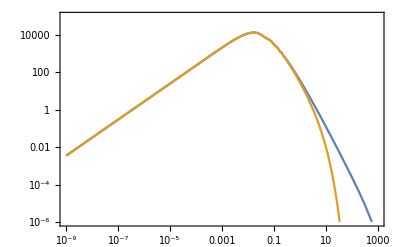

```mathematica
LogLogPlot[{Exp[plinint[Log[k]]],plin[k]},{k,10^-9,1000},Frame->True,PlotRange->{{0.000000001,1000},{10^-6,10^5}}]
```

```mathematica
(* Nmax log k bins, form kmin to kmax *)
kBins[Nmax_,kmin_,kmax_]:=Module[{Δ,result},
Δ=1/(Nmax-1)Log[kmax/kmin]//N;
result=Table[kmin Exp[(i-1) Δ],{i,1,Nmax}];
result
];
```

```mathematica
(* A table of coefficents and powers in FFTLog decomposition of the linear power spectrum *)
CoeffPow[b_,Nmax_,k0_,kmax_,Plin_]:=Module[{Δ,n,m,kn,ηm,ηn,Pn,cn,cnsym,result},
Δ=1/(Nmax-1)Log[kmax/k0]//N;
kn=Table[k0 Exp[(i-1) Δ],{i,1,Nmax}];
ηm=Table[b+(2π I)/(Nmax Δ)(j-Nmax/2-1),{j,1,Nmax+1}];

Pn=Table[{Plin[kn⟦i⟧]Exp[-b(i-1)Δ]},{i,1,Nmax}];
cn=Fourier[Pn,FourierParameters->{-1,-1}];
cnsym=Table[If[(j-Nmax/2)<1,k0^(-ηm⟦j⟧)Conjugate[cn⟦-j+Nmax/2+2,1⟧],k0^(-ηm⟦j⟧)cn⟦j-Nmax/2,1⟧],{j,1,Nmax+1}];
cnsym⟦1⟧=cnsym⟦1⟧/2;
cnsym⟦Length[cnsym]⟧=cnsym⟦Length[cnsym]⟧/2;
result=Table[{cnsym⟦i⟧,ηm⟦i⟧},{i,1,Length[ηm]}];
result
];
```

```mathematica
bias=-1.2501//N;
Nmax=24;
kmin=10^-3;
kmax=1;
cn=CoeffPow[bias,Nmax,kmin,kmax,plin];
kn=kBins[Nmax,kmin,kmax];
```

```mathematica
pfft[k_]=Abs[Total[cn⟦All,1⟧k^cn⟦All,2⟧]];
```

```mathematica
plin[0.0001]
```

235.825

```mathematica
pfft[0.001]
```

2133.13

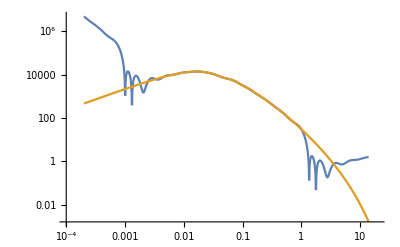

```mathematica
LogLogPlot[{Abs[Total[cn⟦All,1⟧k^cn⟦All,2⟧]],plin[k]},{k,2 10^-4,14},PlotRange->{{10^-4,20},Automatic}]
```

LogLinearPlot::prng: Value of option PlotRange -> {Automatic} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

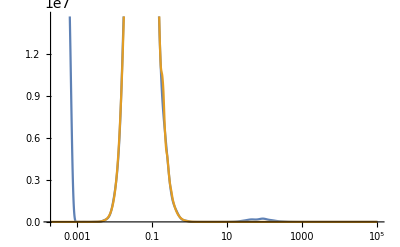

```mathematica
LogLinearPlot[{k^3 Abs[Total[cn⟦All,1⟧k^cn⟦All,2⟧]]^3,k^3 plin[k]^3},{k,2 10^-4,100000},PlotRange->{Automatic}]
```

### PInteger

```mathematica
kBins[Nmax_,kmin_,kmax_]:=Module[{Δ,result},
Δ=1/(Nmax-1)Log[kmax/kmin]//N;
result=Table[kmin Exp[(i-1) Δ],{i,1,Nmax}];
result
];
```

```mathematica
knFit=kBins[100,10^-3,0.4];
```

```mathematica
Ptab = Table[{knFit⟦i⟧,plin[knFit⟦i⟧]},{i,1,Length[knFit]}];
```

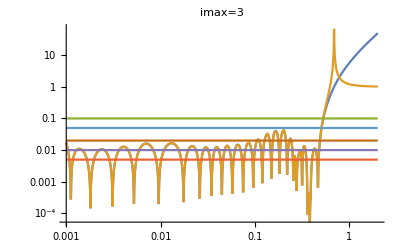

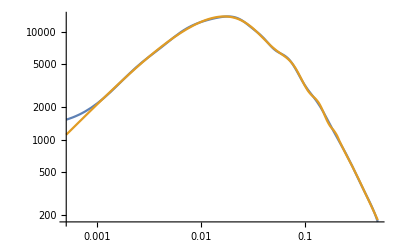

```mathematica
imax=3;
ClearAll[kuv1,kuv2,kuv3,kpeak1,kpeak2,kpeak3,kpeak4,kuv4,nlm,Pinteger]
kuv1=0.069;
kuv2=0.0082;
kuv3=0.0013;
kuv4=0.0000135;
kpeak1=-0.034;
kpeak2=-0.001;
kpeak3=-0.000076;
kpeak4=-0.0000156;
Parameters=Flatten[Table[{a1[i],a2[i],a3[i],a4[i]},{i,0,imax}]];

MyFitFunctions=Flatten[Table[{ 1/((1+((k^2-kpeak1)^2)/kuv1^2)^(i)), (k/(1/20))^2/((1+((k^2-kpeak2)^2)/kuv2^2)^(i+1)),1/((1+((k^2-kpeak3)^2)/kuv3^2)^(i+2)),1/((1+((k^2-kpeak4)^2)/kuv4^2)^(i+1))},{i,0,imax}]];
nlm=LinearModelFit[Ptab,MyFitFunctions(*,Parameters*),k,Weights->1/((10^-6 Ptab⟦All,2⟧)^2),IncludeConstantBasis->False]; 
Myparametersconstraint=Flatten[{{0.04≤kuv1≤ 0.15,0.00002≤kuv2≤0.0004,0.0085≤ kuv3≤0.017,0.000008≤ kuv4≤0.000052,-0.073≤kpeak1≤-0.0003,-0.0001≤kpeak2≤-0.000035,-0.0058≤kpeak3≤-0.0003,-0.00005≤kpeak4≤-0.0000029}}];
Pinteger[k_]=nlm[k];
LogLogPlot[{Abs[Pinteger[k]/plin[k]-1],Abs[plin[k]/Pinteger[k]-1],0.1,0.005,0.01,0.02,0.05},{k,0.001,2.},PlotRange-> All,PlotLabel->"imax="<>ToString[imax]]
LogLogPlot[{Pinteger[k],plin[k]},{k,0.0005,0.5},PlotRange->All]
```

```mathematica
nlm//Normal
```

-436.077+340740./((1+5.48697×10^9 (0.0000156+k^2)^2)^4)-506731./((1+5.48697×10^9 (0.0000156+k^2)^2)^3)+235864./((1+5.48697×10^9 (0.0000156+k^2)^2)^2)-60307.2/(1+5.48697×10^9 (0.0000156+k^2)^2)-203147./((1+591716. (0.000076+k^2)^2)^5)+535845./((1+591716. (0.000076+k^2)^2)^4)-508904./((1+591716. (0.000076+k^2)^2)^3)+204335./((1+591716. (0.000076+k^2)^2)^2)+(4.49831×10^6 k^2)/((1+14872.1 (0.001+k^2)^2)^4)+(4.32028×10^6 k^2)/((1+14872.1 (0.001+k^2)^2)^3)-(2.84454×10^6 k^2)/((1+14872.1 (0.001+k^2)^2)^2)+(4.50859×10^6 k^2)/(1+14872.1 (0.001+k^2)^2)-28591.9/((1+210.04 (0.034+k^2)^2)^3)+13133.4/((1+210.04 (0.034+k^2)^2)^2)-11266.1/(1+210.04 (0.034+k^2)^2)

```mathematica
MyFitFunctions[[16]]/.k->0.001
```

0.0251148

```mathematica
ksub0=Thread[{k1,k2,k3}->{0.017221,0.017221,0.017221}];
ksub20=Thread[{k1,k2,k3}->{0.027562,0.027562,0.027562}];
ksub29=Thread[{k1,k2,k3}->{0.081,0.070261,0.027562}];
ksub124=Thread[{k1,k2,k3}->{0.091757,0.091757,0.048836}];
ksub130=Thread[{k1,k2,k3}->{0.124006,0.102501,0.048836}];
ksub181=Thread[{k1,k2,k3}->{0.091757,0.081,0.059539}];
ksub250=Thread[{k1,k2,k3}->{0.124006,0.081,0.070261}];
ksub655=Thread[{k1,k2,k3}->{0.210114,0.199356,0.124006}];
ksub824=Thread[{k1,k2,k3}->{0.220892,0.220892,0.220892}];
ksubren=Thread[{k1,k2,k3}->{0.001,0.001,0.001}];
ksub=ksub655
```

{k1→0.210114,k2→0.199356,k3→0.124006}

```mathematica
ctest=Import["tables/coeffsb411_p123_numcmass.h5","/Dataset1"];
```

Check J for 411

```mathematica
inttest=q^(-2 n1)k1pq^(-2 n2)k2mq^(-2 n3)(MyFitFunctions⟦15⟧/.k->k2mq)/.{n1->-3,n2->0,n3->1}/.magrevreps/.yrep
```

ReplaceAll::reps: {magrevreps} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {yrep} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

q^6/(k2mq^2 (1+591716. (0.000076+k2mq^2)^2)^5)/.magrevreps/.yrep

```mathematica
ser=Series[inttest/.ksub,{q,∞,2}]//Normal
```

q^6/(k2mq^2 (1+591716. (0.000076+k2mq^2)^2)^5)/.magrevreps/.yrep

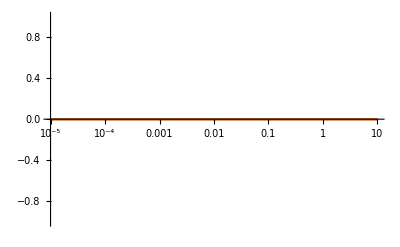

```mathematica
LogLinearPlot[Evaluate[{q^2(inttest-ser)/.ksub/.{β->π/4,x->-1/2,μ->1/2,ϕ->0},q^2(inttest-ser)/.ksub/.{β->π/2,x->0,μ->0,ϕ->π/2},q^2(inttest-ser)/.ksub/.{β->(3 π)/2,x->1/3,μ->1,ϕ->π/3},q^2(inttest-ser)/.ksub/.{β->(2 π)/3,x->-1/3,μ->0,ϕ->π}}/.Plin->plin],{q,10^-5,10}]
```

```mathematica
NIntegrate[q^2/(2π)^3(inttest-ser)/.ksub,{β,0,2π},{x,-1,1},{q,10^-5,10}]
```

ReplaceAll::reps: {magrevreps} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {yrep} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
intnew[n1_,n2_,n3_]=Evaluate[q^(-2 n1)k1pq^(-2 n2)k2mq^(-2 n3)(MyFitFunctions⟦15⟧/.k->q)/.magrevreps/.yrep];
```

ReplaceAll::reps: {magrevreps} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {yrep} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
nb=64;
```

```mathematica
pos1=Position[ctest⟦nb,All,656,1⟧,1.]//Flatten;
posc=Position[ctest⟦nb,All,656,5⟧,_?(#≠0.&)]//Flatten;
posx=Intersection[pos1,posc]
```

{111,113,114,121,123,126,135,137,145,154}

```mathematica
intlist=intnew[ctest⟦nb,posx,656,2⟧,ctest⟦nb,posx,656,3⟧,ctest⟦nb,posx,656,4⟧]/.ksub;
```

ReplaceAll::reps: {magrevreps} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {yrep} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
seruv=Table[Series[intlist⟦i⟧/.ksub,{q,∞,2}]//Normal,{i,1,Length[intlist]}]
```

ReplaceAll::reps: {magrevreps} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{{0,0,0,0,0,0,0,0,0,0}/.magrevreps,yrep}

```mathematica
serir=Table[Series[q^4 intlist⟦i⟧/.ksub,{q,0,0}]/.q->0//Normal,{i,1,Length[intlist]}]
```

ReplaceAll::reps: {magrevreps} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0^4. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{0,0}

```mathematica
LogLinearPlot[Evaluate[{q^2(intlist⟦1⟧-serir⟦1⟧/q^4)/.ksub/.{β->π/4,x->-1/2}}],{q,10^-5,10}]
```

ReplaceAll::reps: {magrevreps} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-Graphics-

```mathematica
Table[NIntegrate[q^2/(2π)^3(intlist⟦i⟧-serir⟦i⟧/q^4)/.ksub,{β,0,2π},{x,-1,1},{q,10^-5,10}],{i,1,Length[intlist]}]
```

ReplaceAll::reps: {magrevreps} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {yrep} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {magrevreps} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NIntegrate::inumr: The integrand (q^2 («1»))/(8 π^3) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,1},{1/100000,10}}.

NIntegrate::inumr: The integrand (q^2 yrep)/(8 π^3) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,1},{1/100000,10}}.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NIntegrate::inumr: The integrand (q^2 (-({0,0}⟦i⟧)/q^4+({1. Power[«2»] Power[«2»],«8»,1. Power[«2»]}/.magrevreps/.yrep)⟦i⟧))/(8 π^3) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,1},{1/100000,10}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{NIntegrate[(q^2 (intlist⟦i⟧-serir⟦i⟧/q^4))/(2 π)^3/.ksub,{β,0,2 π},{x,-1,1},{q,1/10^5,10}],NIntegrate[(q^2 (intlist⟦i⟧-serir⟦i⟧/q^4))/(2 π)^3/.ksub,{β,0,2 π},{x,-1,1},{q,1/10^5,10}]}

### 222

```mathematica
k222[k1_,k2_,q_]:=k222[k1,k2,q]=K2dsym[-q,q+k1]K2dsym[k1+q,k2-q]K2dsym[k2-q,q]
```

```mathematica
B222Integrand[k1_,k2_,q_] := B222Integrand[k1,k2,q]=8k222[k1,k2,q]*Plin[q]Plin[kmq[k2]]Plin[kpq[k1]]/.tb;
```

```mathematica
(*bsub=Thread[biases->{1,1,1,1,0,0,0,0,0,0,0}];*)bsub=Thread[biases->{0.77395605,0.43887844,0.85859792,0.69736803,0.09417735,0.97562235,0.7611397,0.78606431,0.12811363,0.45038594,0.37079802}];
(*bsub=Thread[biases->{2,1,0,0,1,0,0,0,0,0,0}];*)
(*bsub⟦5⟧=b5->(0.77395605-0.43887844);*)
(*ksub=Thread[{k1,k2,k3}->{0.017221,0.017221,0.017221}]*)
(*ksub=Thread[{k1,k2,k3}->{0.081,0.070261,0.027562}]*)
(*ksub=Thread[{k1,k2,k3}->{0.156301,0.145531,0.03818}]*)
(*ksub=Thread[{k1,k2,k3}->{0.027562,0.027562,0.017221}]*)
```

```mathematica
bsub
```

{b1→0.773956,b2→0.438878,b3→0.858598,b4→0.697368,b5→0.0941774,b6→0.975622,b7→0.76114,b8→0.786064,b9→0.128114,b10→0.450386,b11→0.370798}

Zeroth order IR. Converges in the IR for bias -0.25

```mathematica
f2ir0[k1_,k2_,k3_]=Series[8 k222[k1,k2,q]/.tb/.magrevreps,{q,0,-2}]//Normal//Simplify
```

1/(14 k1 k2 q^2)b1^2 (-28 b5 k1^2 k2^2+7 b1 (k1^2+k2^2) (k1^2+k2^2-k3^2)-2 b2 (k1^4+(k2^2-k3^2)^2+2 k1^2 (6 k2^2-k3^2))) x (x y+√(1-x^2) √(1-y^2) Sin[β])

```mathematica
σir0=Integrate[1/(4 π)f2ir0[k1,k2,k3],{β,0,2π},{x,-1,1}]//Simplify
```

1/(42 k1 k2 q^2)b1^2 (-28 b5 k1^2 k2^2+7 b1 (k1^2+k2^2) (k1^2+k2^2-k3^2)-2 b2 (k1^4+(k2^2-k3^2)^2+2 k1^2 (6 k2^2-k3^2))) y

```mathematica
intir0=(pfft[k1]pfft[k2]/.ksub)NIntegrate[q^2/(2 π^2)Plin[q]/.Plin-> pfft,{q,10^-7,100},MaxPoints->200000,PrecisionGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]
```

1.29039×10^10

Zeroth order UV. Converges as q->0

```mathematica
f2uv0[k1_,k2_,k3_]=Series[8 k222[k1,k2,q]/.magrevreps/.yrep,{q,∞,0}]/.tb//Normal
```

8 (-b1+b2+b5)^3

```mathematica
σ20=NIntegrate[q^2/(2 π^2)Plin[q]^3/.Plin-> pfft,{q,10^-4,100},MaxPoints->200000,PrecisionGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]
```

9.46234×10^7

```mathematica
f2uv0[k1,k2,k3]/.bsub
```

-0.111841

```mathematica
f2uv0[k1,k2,k3] σ20/.bsub
```

-1.05828×10^7

```mathematica
Series[f[q],{q,∞,-2}]
```

f[q]

Next order UV

```mathematica
(*f2uv2[k1_,k2_,k3_]=Series[8 k222[k1,k2,q]/.magrevreps/.yrep,{q,∞,2}]/.tb//Normal*)
```

```mathematica
t2 =B222Integrand[k1,k2,q]/.bsub/.magrevreps/.yrep/.ksub(*/.Plin[a_?NumericQ]-> plin[a]*);
```

```mathematica
int2=NIntegrate[q^2/(2π)^3 t2/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-4,10},MaxPoints->200000,PrecisionGoal->5,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 200047 integrand evaluations. NIntegrate obtained 197653. and 93.1751 for the integral and error estimates.

197653.

```mathematica
int2-intir0
```

-1.29037×10^10

```mathematica
t2uv =B222Integrand[k1,k2,q]/.bsub/.magrevreps/.yrep/.{k1->0.001,k2->0.001,k3->0.001}(*/.Plin[a_?NumericQ]-> plin[a]*);
```

```mathematica
int2uv=NIntegrate[q^2/(2π)^3(t2uv)/.Plin-> pfft,{β,0,2π},{x,-1,1},{q,10^-3,10},MaxPoints->200000,PrecisionGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-477627.+0. ⅈ

```mathematica
int2-int2uv
```

675280.+0. ⅈ

```mathematica
t2sub=t2-t2uv//Simplify;
```

$Aborted

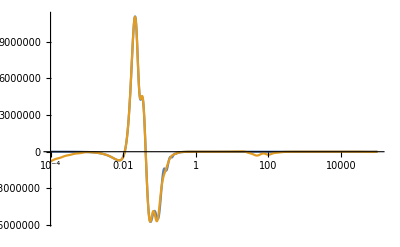

```mathematica
LogLinearPlot[{q^3 t2sub/.Plin->pcut/.{β->π/4,x->-0.8},q^3 t2sub/.Plin->pfft/.{β->π/4,x->-0.8}},{q,10^-4,10^5},PlotRange->All]
```

```mathematica
int2sub=NIntegrate[q^2/(2π)^3 t2sub/.Plin-> pfft,{β,0,2π},{x,-1,1},{q,10^-4,10},MaxPoints->200000,PrecisionGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in q near {β,x,q} = {1.5708,-0.804806,0.027562003339460462989261958354726844208202376568220238649587271635}. NIntegrate obtained 172722.+0. ⅈ and 564.89 for the integral and error estimates.

172722.

```mathematica
intir0
```

4.96573×10^13

```mathematica
-446766.02/-377891.70165368955
```

1.18226

```mathematica
bias
```

-0.801

```mathematica
-189911.7/180956.15718756025
```

-1.04949

```mathematica
-185229.77391878807/-1724547.10
```

0.107408

```mathematica
-189911.77/-213174.86791017855
```

0.890873

```mathematica
-597423.92496/-466017.8755094667
```

1.28198

```mathematica
143627.62473056576/147806.92304
```

0.971725

```mathematica
int2-int2uv
```

171105.+0. ⅈ

```mathematica
int2-f2uv0[k1,k2,k3] σ20/.bsub
```

2.38138×10^7+0. ⅈ

### 3211

```mathematica
k3211[k1_,k2_,q_]:=k3211[k1,k2,q]=K1d[k1] K2dsym[q,k2-q]K3dsym[-q,q-k2,-k1];
```

```mathematica
B3211Integrand[k1_,k2_,q_] :=B3211Integrand[k1,k2,q]= 6Plin[k1]k3211[k1,k2,q] Plin[q]Plin[kmq[k2]]/.tb
```

```mathematica
(*ksub=Thread[{k1,k2,k3}->{0.210114,0.199356,0.124006}]*)
ksub0=Thread[{k1,k2,k3}->{0.017221,0.017221,0.017221}];
ksub=ksub0
(*bsub=Thread[biases->{0.77395605,0.43887844,0.85859792,0.69736803,0.33507761,0.97562235,0.7611397,0.78606431,0.12811363,0.45038594,0.37079802}]*)
(*bsub=Thread[biases->{1,1,1,1,0,0,0,0,0,0,0}]*)
bsub=Thread[biases->{2,1,0,0,1,0,0,0,0,0,0}]
```

{k1→0.017221,k2→0.017221,k3→0.017221}

{b1→2,b2→1,b3→0,b4→0,b5→1,b6→0,b7→0,b8→0,b9→0,b10→0,b11→0}

```mathematica
f3[k1_,k2_,k3_]=B3211Integrand[k1,k2,q]/.magrevreps/.yrep;
```

Renormalization point -- remove only external p

```mathematica
f3ren=6 Plin[k1] k3211[k1,k2,q] Plin[q]^2/.tb/.bsub/.magrevreps/.yrep/.ksub/.Plin[a_?NumericQ]-> plin[a]//Simplify;
```

```mathematica
1/(plin[k1]/.ksub)NIntegrate[q^2/(2π)^3 f3ren/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.0001,40},MaxPoints->100000,PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

-3.20337

IR term

```mathematica
f3ir0[k1_,k2_,k3_]=Series[6 k3211[k1,k2,q]/.tb/.magrevreps,{q,0,-3}]
```

1/O[q]^2

Zeroth order UV

```mathematica
k3exp=Expand[6 k3211[k1,k2,q]/.tb/.magrevreps/.yrep];(*/.{k1->y1 k3,k2->y2 k3}/.k3->ϵ q];*)
```

```mathematica
serB3tab=Monitor[Table[Series[k3exp⟦i⟧,{q,∞,0}],{i,1,Length[k3exp]}],100.0 i/Length[k3exp]];
```

```mathematica
Total[SeriesCoefficient[#,0]&/@serB3tab]//Simplify
```

1/(7 k1^2)b1 (b1-b2-b5) (-42 b10 k1^2+27 b2 k1^2-26 b3 k1^2+35 b5 k1^2-68 b6 k1^2-40 b8 k1^2+7 b2 k2^2+7 b5 k2^2-7 b2 k3^2-7 b5 k3^2+8 b2 k1^2 x^2-16 b3 k1^2 x^2-16 b6 k1^2 x^2-44 b8 k1^2 x^2+b1 (-7 k2^2+7 k3^2+k1^2 (-1+8 x^2)))

```mathematica
f3uv0[k1_,k2_,k3_]=Series[6 k3211[k1,k2,q]/.tb/.magrevreps/.yrep,{q,∞,0}]//Normal
```

$Aborted

```mathematica
f3uv0sym=Series[6 k3211[k1,k3,q]/.tb/.magrevreps/.yrep,{q,∞,0}]//Normal
```

1/(7 k1^2)b1 (b1-b2-b5) (-b1 k1^2-42 b10 k1^2+27 b2 k1^2-26 b3 k1^2+35 b5 k1^2-68 b6 k1^2-40 b8 k1^2+7 b1 k2^2-7 b2 k2^2-7 b5 k2^2-7 b1 k3^2+7 b2 k3^2+7 b5 k3^2+8 b1 k1^2 x^2+8 b2 k1^2 x^2-16 b3 k1^2 x^2-16 b6 k1^2 x^2-44 b8 k1^2 x^2)

```mathematica
1/(4π)Integrate[f3uv0[k1,k2,k3]+f3uv0sym,{x,-1,1},{β,0,2π}]//Simplify
```

2/21 b1 (b1-b2-b5) (5 b1-126 b10+89 b2-94 b3+105 b5-220 b6-164 b8)

```mathematica
Reduce[1+3x<0]
```

x<-1/3

```mathematica
int3uv0=1/(4 π)Integrate[f3uv0[k1,k2,k3],{x,-1,1},{β,0,2π}]
```

1/(21 k1^2)b1 (b1-b2-b5) (5 b1 k1^2-126 b10 k1^2+89 b2 k1^2-94 b3 k1^2+105 b5 k1^2-220 b6 k1^2-164 b8 k1^2-21 b1 k2^2+21 b2 k2^2+21 b5 k2^2+21 (b1-b2-b5) k3^2)

```mathematica
f3uv0[k1,k2,k3]/.bsub
```

0.

Second order term

```mathematica
(*f3uv2[k1_,k2_,k3_]=Series[6 k3211[k1,k2,q]/.tb/.magrevreps,{q,∞,2}]*)
```

```mathematica
t3p1 =f3[k1,k2,k3]/Plin[k1]/.bsub/.magrevreps/.yrep/.ksub(*/.Plin[a_?NumericQ]-> plin[a]*)//Simplify;
t3p2 = f3[k2,k3,k1]/Plin[k2]/.bsub/.magrevreps/.yrep/.ksub(*/.Plin[a_?NumericQ]-> plin[a]*)//Simplify;
t3p3 = f3[k3,k1,k2]/Plin[k3]/.bsub/.magrevreps/.yrep/.ksub(*/.Plin[a_?NumericQ]-> plin[a]*)//Simplify;
t3p4 =f3[k2,k1,k3]/Plin[k2]/.bsub/.magrevreps/.yrep/.ksub(*/.Plin[a_?NumericQ]-> plin[a]*)//Simplify;
t3p5 = f3[k3,k2,k1]/Plin[k3]/.bsub/.magrevreps/.yrep/.ksub(*/.Plin[a_?NumericQ]-> plin[a]*)//Simplify;
t3p6 = f3[k1,k3,k2]/Plin[k1]/.bsub/.magrevreps/.yrep/.ksub(*/.Plin[a_?NumericQ]-> plin[a]*)//Simplify;
```

```mathematica
fullint1=NIntegrate[q^2/(2π)^3(t3p1+t3p2+t3p3+t3p4+t3p5+t3p6)/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,10},MaxPoints->100000,PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-2221.26

```mathematica
intsum=q^2/(2π)^3(plin[k1]t3p1+plin[k2]t3p2+plin[k3]t3p3+plin[k2]t3p4+plin[k3]t3p5+plin[k1]t3p6);
```

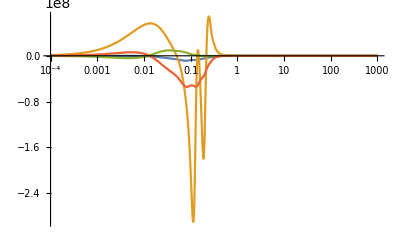

```mathematica
LogLinearPlot[Evaluate[{intsum/.β->0/.x->0,intsum/.β->π/2/.x->0,intsum/.β->π/2/.x->1,intsum/.β->π/4/.x->-1/2}/.ksub/.Plin-> plin],{q,0.0001,1000},PlotRange->All]
```

```mathematica
fullint=NIntegrate[q^2/(2π)^3(plin[k1]t3p1+plin[k2]t3p2+plin[k3]t3p3+plin[k2]t3p4+plin[k3]t3p5+plin[k1]t3p6)/.ksub/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.0001,10},MaxPoints->200000,PrecisionGoal->3,WorkingPrecision->MachinePrecision,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 200050 integrand evaluations. NIntegrate obtained -2.59668×10^7 and 28202.1 for the integral and error estimates.

-2.59668×10^7

```mathematica
int1=NIntegrate[q^2/(2π)^3(t3p1)/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.0001,10},(*MaxPoints->200000,*)PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-370.081

```mathematica
int2=NIntegrate[q^2/(2π)^3 t3p2/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100018 integrand evaluations. NIntegrate obtained -3.29669×10^6 and 4191.23 for the integral and error estimates.

-3.29669×10^6

```mathematica
int3=NIntegrate[q^2/(2π)^3 t3p3/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100010 integrand evaluations. NIntegrate obtained -3.57091×10^6 and 11386.2 for the integral and error estimates.

-3.57091×10^6

```mathematica
int4=NIntegrate[q^2/(2π)^3 t3p4/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100042 integrand evaluations. NIntegrate obtained -8.82483×10^6 and 5542.51 for the integral and error estimates.

-8.82483×10^6

```mathematica
int5=NIntegrate[q^2/(2π)^3 t3p5/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100060 integrand evaluations. NIntegrate obtained 3.70551×10^6 and 10630.9 for the integral and error estimates.

3.70551×10^6

```mathematica
int6=NIntegrate[q^2/(2π)^3 t3p6/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

-0.713759

```mathematica
int1+int2+int3+int4+int5+int6
```

-2.59794×10^7

```mathematica
{int1,int2,int3,int4,int5,int6}
```

{2.15038×10^6,2.30707×10^6,2.76814×10^6,2.4124×10^6,2.77275×10^6,2.05322×10^6}

Renormalization by stochastic counterterm. In real space there are 4 different conditions on the integral

```mathematica
K1r[k1]Plin[k1](Subscript[d, 3]+Subscript[d, 4] μ1^2+Subscript[d, 5] k1^2 +Subscript[d, 6](k2^2+k3^2) +Subscript[d, 7]((k2^2-k3^2)^2)/k1^2+Subscript[d, 8] k1^2 μ1^2 +Subscript[d, 9](k3^2 μ2^2+k2^2 μ3^2)+Subscript[d, 10] k1^2 (μ2^2+μ3^2) +Subscript[d, 11](k2^2 μ2^2+k3^2 μ3^2) +Subscript[d, 12] μ1^2(k2^2+k3^2)  +Subscript[d, 13]((k2^2-k3^2)^2 (μ2^2+μ3^2))/k1^2+Subscript[d, 14]((k2^2-k3^2) (k2^2 μ2^2-k3^2 μ3^2))/k1^2 +Subscript[d, 15] k1^2 μ1^4+Subscript[d, 16] μ1^2 (k2^2 μ2^2+k3^2 μ3^2) )/.tb/.μ1->0/.μ2->0/.μ3->0
```

b1 Plin[k1] (d_3+k1^2 d_5+(k2^2+k3^2) d_6+((k2^2-k3^2)^2 d_7)/k1^2)

So we will choose 4 different triangles to solve for the d’s, at small values of k

```mathematica
reneqs={I1+Subscript[d, 3]+k11^2 Subscript[d, 5]+(k12^2+k13^2) Subscript[d, 6]+((k12^2-k13^2)^2 Subscript[d, 7])/k11^2==0,I2+Subscript[d, 3]+k21^2 Subscript[d, 5]+(k22^2+k23^2) Subscript[d, 6]+((k22^2-k23^2)^2 Subscript[d, 7])/k21^2==0,I3+Subscript[d, 3]+k31^2 Subscript[d, 5]+(k32^2+k33^2) Subscript[d, 6]+((k32^2-k33^2)^2 Subscript[d, 7])/k31^2==0,I4+Subscript[d, 3]+k41^2 Subscript[d, 5]+(k42^2+k43^2) Subscript[d, 6]+((k42^2-k43^2)^2 Subscript[d, 7])/k41^2==0};
```

### 411

#### Save kernels

```mathematica
k411[k1_,k2_,q_]:=k411[k1,k2,q]= K1d[k1]K1d[k2] K4dsym[q,-q,-k2,-k1]/.mag[0]-> 0
```

```mathematica
k411[k1,k2,q]=<<"myk411k2k1.m";
```

```mathematica
B411Integrand[k1_,k2_,q_] :=B411Integrand[k1,k2,q]= 12Plin[k1]Plin[k2]Plin[q]k411[k1,k2,q]/.f1->0/.tb/.Thread[adelta-> 0]
```

```mathematica
B411Integrand[k1,k2,q]=<<"tables/B411realspacek1k2.m"
```

12 b1^2 ((b10 (k2^2 q^2 (k1mq^2+k1pq^2-k2^2+k3^2-2 q^2)-k1^4 1+k1^2 (k1mq^2 k2^2+k1pq^2 k2^2-2 k2^4+k2^2 k2mq^2+1-1+k2mq^2 q^2+k2pq^2 q^2+k3^2 q^2-2 q^4)))/(8 k1^2 k2^2 q^2)-(b6 1)/(336 2 q^4)+7+1+(b9 (-42 k1^12 (k1mq^2+k1pq^2) 3 k3^2 k3mq^2 k3pq^2+8+1))/(169344 k1^4 k1mq^2 k1pq^2 k2^4 k2mq^2 k2pq^2 k3^2 k3mq^2 k3pq^2 q^4)) 1 Plin[k2] Plin[q]
 |  |  |  |

```mathematica
k4exp=Expand[B411Integrand[k1,k2,q]/(Plin[k1]Plin[k2]Plin[q])/.magrevreps];
```

```mathematica
serB411tab=Monitor[Table[Series[k4exp⟦i⟧,{q,∞,2}],{i,1,Length[k4exp]}],100.0 i/Length[k4exp]];
```

Let’s consider the 0th order term, and integrate the various terms. Use similar rules as for the monopole

```mathematica
angint[a_,b_,c_,d_]=((1+(-1)^a) (1+(-1)^c) (1+(-1)^d) Gamma[(1+a)/2] Gamma[1+b/2] Gamma[(1+c)/2] Gamma[(1+d)/2])/(16 π Gamma[1/2 (3+a+b)] Gamma[1/2 (2+c+d)])
```

((1+(-1)^a) (1+(-1)^c) (1+(-1)^d) Gamma[(1+a)/2] Gamma[1+b/2] Gamma[(1+c)/2] Gamma[(1+d)/2])/(16 π Gamma[1/2 (3+a+b)] Gamma[1/2 (2+c+d)])

```mathematica
rulesμ04={x^(a_.) (√(1-x^2))^(b_.)Cos[β]^(c_.)Sin[β]^(d_.)->angint[a,b,c,d]};
rulesμ03={x^(a_.) (√(1-x^2))^(b_.)Cos[β]^(c_.)->angint[a,b,c,0],
x^(a_.) (√(1-x^2))^(b_.)Sin[β]^(d_.)->angint[a,b,0,d],
x^(a_.) Cos[β]^(c_.)Sin[β]^(d_.)->angint[a,0,c,d],
(√(1-x^2))^(b_.)Cos[β]^(c_.)Sin[β]^(d_.)->angint[0,b,c,d]};
rulesμ02={x^(a_.) (√(1-x^2))^(b_.)->angint[a,b,0,0],
x^(a_.) Cos[β]^(c_.)->angint[a,0,c,0],
 (√(1-x^2))^(b_.)Cos[β]^(c_.)->angint[0,b,c,0],
x^(a_.) Sin[β]^(d_.)->angint[a,0,0,d],
 (√(1-x^2))^(b_.)Sin[β]^(d_.)->angint[0,b,0,d],
Cos[β]^(c_.)Sin[β]^(d_.)->angint[0,0,c,d]};
rulesμ01={x^(a_.)->angint[a,0,0,0],(√(1-x^2))^(b_.)->angint[0,b,0,0], Cos[β]^(c_.)->angint[0,0,c,0],Sin[β]^(d_.)->angint[0,0,0,d]};
```

```mathematica
ser0B411tabtemp=Expand[Total[SeriesCoefficient[#,0]&/@serB411tab]];
```

```mathematica
ser0B411tabint=Monitor[Table[ser0B411tabtemp⟦i⟧/.rulesμ04/.rulesμ03/.rulesμ02/.rulesμ01,{i,1,Length[ser0B411tabtemp]}],100.0 i/Length[ser0B411tabtemp]];
```

```mathematica
ser0B411tabintfin=Simplify[Total[ser0B411tabint]];
```

```mathematica
(Plin[k1]Plin[k2]Plin[q]ser0B411tabintfin)>>"tables/B411realspacek1k2UV0.m"
```

```mathematica
ser2B411tabtemp=Expand[Total[SeriesCoefficient[#,2]&/@serB411tab]/.SeriesCoefficient[_,2]->0];
```

```mathematica
ser2B411tabint=Monitor[Table[Expand[ser2B411tabtemp⟦i⟧]/.rulesμ04/.rulesμ03/.rulesμ02/.rulesμ01,{i,1,Length[ser2B411tabtemp]}],100.0 i/Length[ser2B411tabtemp]];
```

```mathematica
ser2B411tabintfin=Simplify[Total[ser2B411tabint]];
```

```mathematica
(q^2 Plin[k1]Plin[k2]Plin[q]ser2B411tabintfin)>>"tables/B411realspacek1k2UV2.m"
```

Integrate

```mathematica
ksub=Thread[{k1,k2,k3}->{0.017221,0.017221,0.017221}]
bsub=Thread[biases->{1,1,1,1,0,0,0,0,0,0,0}]
```

{k1→0.017221,k2→0.017221,k3→0.017221}

{b1→1,b2→1,b3→1,b4→1,b5→0,b6→0,b7→0,b8→0,b9→0,b10→0,b11→0}

```mathematica
(*f4[k1_,k2_,k3_]=B411Integrand[k1,k2,q]/.magrevreps/.yrep*)
```

12 Plin[k1] 1 1 ((b10 (k2^2 (2 k1^2-k2^2+k3^2) q^2-k1^4 (1)+k1^2 (-2 k2^4-14 k2^2 q^2+7+k2^2 (1)+q^2 (k2^2+q^2+2 k2 q (1/(2 k1 k2)+1)))))/(8 k1^2 k2^2 q^2)-(b6 (96+k1^2 1))/(336 k1^2 k2^2 q^4)+32+(b4 (1))/(1862784 9 (1))+(f1 (1)^2 (-1+10+1/(465696 9 (1))))/k3^2)
 |  |  |  |

```mathematica
f4subUV[k1_,k2_,k3_]=(B411Integrand[k1,k2,q]-Plin[k1]Plin[k2]Plin[q](ser0B411tabintfin+q^2 ser2B411tabintfin))/.magrevreps/.yrep;
```

```mathematica
(*Plin[k1]Plin[k2]Plin[q](ser0B411tabintfin+q^2 ser2B411tabintfin)/.magrevreps/.yrep;*)
```

```mathematica
σ0=NIntegrate[q^2/(2 π^2)Plin[q]/.Plin-> plin,{q,0.001,20},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

16.3167

```mathematica
σ2=NIntegrate[q^4/(2 π^2)Plin[q]/.Plin-> plin,{q,0.001,20},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

1399.08

```mathematica
t4p1 =f4subUV[k1,k2,k3]/(Plin[k1] Plin[k2])/.bsub/.magrevreps/.yrep/.ksub/.Plin[a_?NumericQ]-> plin[a];
t4p2 = f4subUV[k2,k3,k1]/(Plin[k2] Plin[k3])/.bsub/.magrevreps/.yrep/.ksub/.Plin[a_?NumericQ]-> plin[a];
t4p3 = f4subUV[k3,k1,k2]/(Plin[k3] Plin[k1])/.bsub/.magrevreps/.yrep/.ksub/.Plin[a_?NumericQ]-> plin[a];
```

```mathematica
int1=NIntegrate[q^2/(2π)^3 t4p1/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,20},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

0.025888

```mathematica
int2=NIntegrate[q^2/(2π)^3 t4p2/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,20},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

0.025888

```mathematica
int3=NIntegrate[q^2/(2π)^3 t4p3/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,20},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

0.025888

```mathematica
-94854.02971241245-351635.51119745645-220502.23956838233
```

-666992.

```mathematica
Plin[k1]Plin[k2]σ2 ser2B411tabintfin/.Plin->plin/.bsub/.yrep/.ksub
```

-1.8311×10^6

#### Load and integrate

```mathematica
B411Integrand[k1,k2,q]=<<"tables/B411realspacek1k2.m"
```

12 b1^2 ((b10 (k2^2 q^2 (k1mq^2+k1pq^2-k2^2+k3^2-2 q^2)-k1^4 1+k1^2 (k1mq^2 k2^2+k1pq^2 k2^2-2 k2^4+k2^2 k2mq^2+1-1+k2mq^2 q^2+k2pq^2 q^2+k3^2 q^2-2 q^4)))/(8 k1^2 k2^2 q^2)-(b6 1)/(336 2 q^4)+7+1+(b9 (-42 k1^12 5 k3mq^2 k3pq^2+8+k1^2 (1)))/(169344 k1^4 k1mq^2 k1pq^2 k2^4 k2mq^2 k2pq^2 k3^2 k3mq^2 k3pq^2 q^4)) 1 Plin[k2] Plin[q]
 |  |  |  |

```mathematica
UV0=<<"tables/B411realspacek1k2UV0.m";
UV2=<<"tables/B411realspacek1k2UV2.m";
```

Integrate

```mathematica
ksub=Thread[{k1,k2,k3}->{0.017221,0.017221,0.017221}]
bsub=Thread[biases->{1,1,1,1,0,0,0,0,0,0,0}]
```

{k1→0.017221,k2→0.017221,k3→0.017221}

{b1→1,b2→1,b3→1,b4→1,b5→0,b6→0,b7→0,b8→0,b9→0,b10→0,b11→0}

```mathematica
f4[k1_,k2_,k3_]=(B411Integrand[k1,k2,q]-0 UV0-0 UV2)/.magrevreps/.yrep/.bsub
```

12 3 ((294 k1^8 3 (k2^2+q^2-2 k2 q (1/1+1)) (k2^2+q^2+2 k2 q (((-k1^2-k2^2+k3^2) x)/(2 k1 k2)+√(1-(1)^2/(4 k1^2 k2^2)) √(1-x^2) Sin[β]))+11+1)/(18816 k1^2 k2^2 3 (1) (k2^2+q^2-2 k2 q (1/(2 k1 k2)+1)) (k2^2+q^2+2 k2 q (((-k1^2-k2^2+k3^2) x)/(2 k1 k2)+√(1-(1)^2/(4 k1^2 k2^2)) √(1-x^2) Sin[β])))+2+1)
 |  |  |  |

```mathematica
f4eq[k_]=Simplify[f4[k,k,k]/Plin[k]^2];
```

```mathematica
t4eq =f4eq[k]/.k->0.017221/.Plin[a_?NumericQ]-> plin[a]//Simplify//Chop;
```

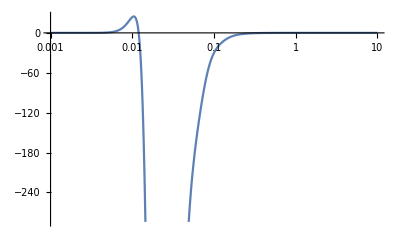

```mathematica
LogLinearPlot[t4eq/.x->0/.β->π/2/.Plin->Pinteger,{q,0.001,10}]
```

```mathematica
inteq=NIntegrate[q^2/(2π)^3 t4eq/.Plin-> Pinteger,{β,0,2π},{x,-1,1},{q,10^-5,5},MaxPoints->200000,PrecisionGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 200049 integrand evaluations. NIntegrate obtained 0.000781839 and 6.85625×10^-7 for the integral and error estimates.

0.000781839

```mathematica
fnew=f4[k1,k2,k3]/.β->0/.x->0/.Plin->Function[x,1]//Simplify;
```

```mathematica
f4subUV[k1_,k2_,k3_]=(B411Integrand[k1,k2,q]-UV0-UV2)/.magrevreps/.yrep;
```

```mathematica
t4p1 =f4[k1,k2,k3]/(Plin[k1] Plin[k2])/.bsub/.magrevreps/.yrep/.ksub/.Plin[a_?NumericQ]-> plin[a]//Simplify//Chop;
t4p2 = f4[k2,k3,k1]/(Plin[k2] Plin[k3])/.bsub/.magrevreps/.yrep/.ksub/.Plin[a_?NumericQ]-> plin[a]//Simplify//Chop;
t4p3 = f4[k3,k1,k2]/(Plin[k3] Plin[k1])/.bsub/.magrevreps/.yrep/.ksub/.Plin[a_?NumericQ]-> plin[a]//Simplify//Chop;
```

```mathematica
F1=B411Integrand[k1,k2,q]/.bsub/.magrevreps/.yrep/.ksub/.Plin[a_?NumericQ]-> plin[a]//Simplify//Chop;
F2=UV0/.bsub/.magrevreps/.yrep/.ksub/.Plin[a_?NumericQ]-> plin[a]//Simplify//Chop;
F3=UV2/.bsub/.magrevreps/.yrep/.ksub/.Plin[a_?NumericQ]-> plin[a]//Simplify//Chop;
```

One has to be careful in integrating far, since numerical imprecisions make spurious divergences for high q

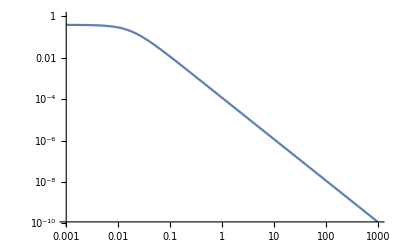

```mathematica
LogLogPlot[Evaluate[fnew/.bsub/.ksub],{q,0.001,1000}]
```

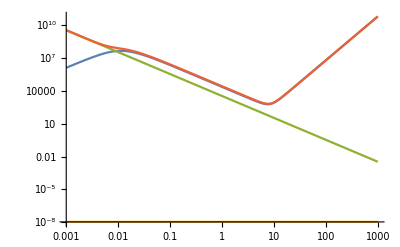

```mathematica
LogLogPlot[Evaluate[{Abs[F1],Abs[F2],Abs[F3],Abs[F1-F2-F3]}/.{β->0,x->0.}/.Plin-> Function[x,1]],{q,0.001,1000}]
```

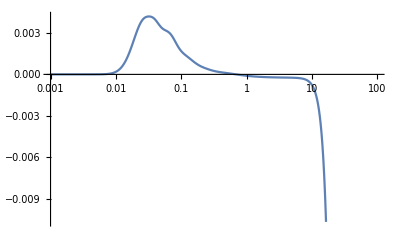

```mathematica
LogLinearPlot[q^2/(2π)^3 t4p1/.Plin-> Pinteger/.{β->0,x->0.},{q,0.001,100}]
```

```mathematica
int1=NIntegrate[q^2/(2π)^3 t4p1/.Plin-> Pinteger,{β,0,2π},{x,-1,1},{q,10^-4,0.4},MaxPoints->200000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

0.0000365861

```mathematica
int2=NIntegrate[q^2/(2π)^3 t4p2/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-4,10},MaxPoints->200000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

0.00258554

```mathematica
int3=NIntegrate[q^2/(2π)^3 t4p3/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-4,10},MaxPoints->200000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

0.00258554

```mathematica
int411=int1+int2+int3
```

```mathematica
-0.021234867118799315 2
```

-0.0424697

```mathematica
-94854.02971241245-351635.51119745645-220502.23956838233
```

-666992.

```mathematica
Plin[k1]Plin[k2]σ2 ser2B411tabintfin/.Plin->plin/.bsub/.yrep/.ksub
```

-1.8311×10^6

## Numerical Integration, real space FFT

```mathematica
plindat=Import["FFTlog/PlinPlanck_z0p56.dat"];
plin=Interpolation[plindat];
```

```mathematica
angint[a_,b_,c_,d_]=((1+(-1)^a) (1+(-1)^c) (1+(-1)^d) Gamma[(1+a)/2] Gamma[1+b/2] Gamma[(1+c)/2] Gamma[(1+d)/2])/(16 π Gamma[1/2 (3+a+b)] Gamma[1/2 (2+c+d)])
```

((1+(-1)^a) (1+(-1)^c) (1+(-1)^d) Gamma[(1+a)/2] Gamma[1+b/2] Gamma[(1+c)/2] Gamma[(1+d)/2])/(16 π Gamma[1/2 (3+a+b)] Gamma[1/2 (2+c+d)])

### Pfft

#### Compiled J ( Not tested for Abs[Im[ν]]>10 )

```mathematica
Needs["CompiledFunctionTools`"];
```

```mathematica
GammaC=Compile[{{z,_Complex}},
Block[{q0,q1,q2,q3,q4,q5,q6,p1,p2,result},
q0=75122.6331530+0.0I;
	q1=80916.6278952+0.0I;
	q2=36308.2951477+0.0I;
	q3=8687.24529705+0.0I;
	q4=1168.92649479+0.0I;
	q5=83.8676043424+0.0I;
	q6=2.50662827511+0.0I;
If[Re[z]≥0,p1=(q0+q1 z+q2 z^2+q3 z^3+q4 z^4+q5 z^5+q6 z^6)/(z(z+1)(z+2)(z+3)(z+4)(z+5)(z+6));result=p1 (z+5.5)^(z+0.5)Exp[-z-5.5],p1=(q0+q1(1-z)+q2 (1-z)^2+q3 (1-z)^3+q4 (1-z)^4+q5 (1-z)^5+q6 (1-z)^6)/((1-z)(2-z)(3-z)(4-z)(5-z)(6-z)(7-z));p2=p1(1-z+5.5)^(1-z+0.5)Exp[-1+z-5.5];result=π/(Sin[π z]p2)];
result
],
{{Sin[_],_Complex},{Exp[_],_Complex},{Re[_],_Real}}, 
CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization" -> True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True},RuntimeOptions->{"CatchMachineOverflow"->False , "CatchMachineUnderflow"->False,"CatchMachineIntegerOverflow"->False,"CompareWithTolerance"->False,"EvaluateSymbolically"->False}];
```

```mathematica
Hyp2F1basic=Compile[{{a,_Complex},{b,_Complex},{c,_Complex},{z,_Complex}},
Block[{p,s,sold,eps,n},
s=0.0+0.0 I;
p=1.0+0.0I;
eps=1.0;
n=0.0;
While[eps>10^-12,
sold=s;
s=s+p;
p=p((a+n)(b+n))/((c+n)(n+1))z;
eps=Abs[(s-sold)/s];
n++];
s
],
CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization" -> True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True},RuntimeOptions->{"CatchMachineOverflow"->False , "CatchMachineUnderflow"->False,"CatchMachineIntegerOverflow"->False,"CompareWithTolerance"->False,"EvaluateSymbolically"->False}];
```

```mathematica
JFastC = Compile[{{ν1,_Complex},{ν2,_Complex},{ν3,_Complex},{x,_Complex},{y,_Complex},{epscr,_Real}},
Block[
{p1,p2,s1,s2,s1old,s2old,eps,n,result},
s1=0.+I 0.;
p1=(GammaC[2-2 ν2] GammaC[2-2 ν3] Sin[π ν2] Sin[π ν3])/GammaC[5-2 ν2-2 ν3] x^(1.5-ν2-ν3);
p2=(GammaC[2-2 ν1] GammaC[2 (-2+ν1+ν2+ν3)] Sin[π ν1] Sin[π (ν1+ν2+ν3)])/GammaC[-1+2 ν2+2 ν3] y^(1.5-ν1-ν3);
s2=0.+I 0.;
eps=1.;
n=0.0;
While[eps>epscr,
s1old=s1;
s2old=s2;

s1=s1+p1 Hyp2F1basic[ν1+n,1.5-ν2+n,3-ν2-ν3+2 n,1-y];
s2=s2+p2 Hyp2F1basic[ν2+n,1.5-ν1+n,ν2+ν3+2 n,1-y];

p1=p1*((n+ν1) (3-ν1-ν2-ν3+n) (1.5-ν3+n) (1.5-ν2+n))/((1+n) (2.5-ν2-ν3+n) (4-ν2-ν3+2 n) (3-ν2-ν3+2 n)) x;
p2=p2*((1.5-ν1+n) (ν1+ν2+ν3-1.5+n) (n+ν2) (n+ν3))/((1+n) (ν2+ν3-0.5+n) (1+ν2+ν3+2 n) (ν2+ν3+2 n)) x;

eps=Abs[(s1-s2-s1old+s2old)/(s1-s2)];
n++];

result=Sec[π (ν2+ν3)]/(2 π^2) (s1-s2);
result
],
{{GammaC[_],_Complex},{Sec[_],_Complex},{Abs[_],_Real},{Sin[_],_Complex}}
,
CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization" -> True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True},RuntimeOptions->{"CatchMachineOverflow"->False , "CatchMachineUnderflow"->False,"CatchMachineIntegerOverflow"->False,"CompareWithTolerance"->False,"EvaluateSymbolically"->False}];
```

```mathematica
JFastCa[arr_,x_,y_]:= JFastC[10^-10+arr[[1]],10^-10+arr[[2]],10^-10+arr[[3]],x,y,10^-8];
```

#### J function numerical check

```mathematica
NIntegrate[q^2/(2π)^3/((q^2)^(0.9+3I)(1+q^2-2 q μ)^(0.6+I)(q^2+y+q (-1+x-y) μ+q √(-x^2-(-1+y)^2+2 x (1+y)) √(1-μ^2) Cos[ϕ])^(1+1.3I))/.{x->0.3,y->0.8},{ϕ,0,2π},{μ,-1,1},{q,0,1000},MaxPoints->1000000,AccuracyGoal->10]//Quiet//AbsoluteTiming
```

{2.218,0.0176001+0.00370646 ⅈ}

```mathematica
ν1=0.9+3I;
ν2=0.6+I;
ν3=1+1.3I;
x=0.3;
y=0.8;
res=(Gamma[3/2-ν3]Gamma[ν1+ν2+ν3-3/2])/(4 π^2 Gamma[ν1]Gamma[ν2])NIntegrate[u^(ν1-1)(1-u)^(ν2-1)(x(1-u)+y u)^(3/2-ν1-ν2-ν3)Hypergeometric2F1[1.5-ν3,-1.5+ν1+ν2+ν3,1.5,1-(u(1-u))/(x(1-u)+y u)],{u,0,1}]//AbsoluteTiming
Clear[ν1,ν2,ν3,x,y];
```

{0.083812,0.0176001+0.00370646 ⅈ}

```mathematica
JFastC[0.9+3I,0.6+I,1+1.3I,0.3,0.8,10^-8]//AbsoluteTiming
```

{0.000429,0.0176001+0.00370646 ⅈ}

```mathematica
NIntegrate[q^2/(2π)^3/((q^2)^0.9(1+q^2-2 q μ)^(0.6+I)(q^2+y+q (-1+x-y) μ+q √(-x^2-(-1+y)^2+2 x (1+y)) √(1-μ^2) Cos[ϕ])^1)/.{x->0.3,y->0.8},{ϕ,0,2π},{μ,-1,1},{q,0,1000},MaxPoints->1000000,AccuracyGoal->10]//Quiet//AbsoluteTiming
```

{3.2168,0.0617987+0.0555097 ⅈ}

```mathematica
JFastC[0.9,0.6+I,0.9999999,0.3,0.8,10^-8]//AbsoluteTiming
```

{0.000044,0.0617986+0.0555097 ⅈ}

```mathematica
JFastC[0.99999,0.9,0,0.1,0.2,10^-8]//AbsoluteTiming
```

{0.000044,0.129282+0. ⅈ}

```mathematica
JFastC[0.9,0.6+I,0 0.9999999,0.3,0.8,10^-8]//AbsoluteTiming
```

{0.000023,0.0245486-0.0135016 ⅈ}

```mathematica
J2[1,0.9,0.6+I]
```

J2[1,0.9,0.6+1. ⅈ]

#### Linear PS and decomposition

```mathematica
As=plindat⟦1,2⟧;
kb=plindat⟦1,1⟧;
pextra=Table[{10^(-10+( i-1) 0.2), As (10^(-10+ (i-1) 0.2)/kb)^0.9649},{i,1,30}];
plindat2=Join[pextra,plindat];
plinus=Interpolation[plindat2];
plinint=Interpolation[Log[plindat2]];
```

```mathematica
Clear[plin]
khigh=400.;
pcut[k_]= Exp[plinint[Log[k]]](*Exp[-(k/khigh)]*);
plin[k_]=pcut[k];
```

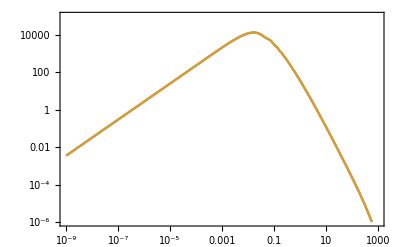

```mathematica
LogLogPlot[{Exp[plinint[Log[k]]],plin[k]},{k,10^-9,1000},Frame->True,PlotRange->{{0.000000001,1000},{10^-6,10^5}}]
```

```mathematica
(* Nmax log k bins, form kmin to kmax *)
kBins[Nmax_,kmin_,kmax_]:=Module[{Δ,result},
Δ=1/(Nmax-1)Log[kmax/kmin]//N;
result=Table[kmin Exp[(i-1) Δ],{i,1,Nmax}];
result
];
```

```mathematica
(* A table of coefficents and powers in FFTLog decomposition of the linear power spectrum *)
CoeffPow[b_,Nmax_,k0_,kmax_,Plin_]:=Module[{Δ,n,m,kn,ηm,ηn,Pn,cn,cnsym,result},
Δ=1/(Nmax-1)Log[kmax/k0]//N;
kn=Table[k0 Exp[(i-1) Δ],{i,1,Nmax}];
ηm=Table[b+(2π I)/(Nmax Δ)(j-Nmax/2-1),{j,1,Nmax+1}];

Pn=Table[{Plin[kn⟦i⟧]Exp[-b(i-1)Δ]},{i,1,Nmax}];
cn=Fourier[Pn,FourierParameters->{-1,-1}];
cnsym=Table[If[(j-Nmax/2)<1,k0^(-ηm⟦j⟧)Conjugate[cn⟦-j+Nmax/2+2,1⟧],k0^(-ηm⟦j⟧)cn⟦j-Nmax/2,1⟧],{j,1,Nmax+1}];
cnsym⟦1⟧=cnsym⟦1⟧/2;
cnsym⟦Length[cnsym]⟧=cnsym⟦Length[cnsym]⟧/2;
result=Table[{cnsym⟦i⟧,ηm⟦i⟧},{i,1,Length[ηm]}];
result
];
```

```mathematica
bias=-0.5501//N;
Nmax=24;
kmin=10^-3;
kmax=1;
cn=CoeffPow[bias,Nmax,kmin,kmax,plin];
kn=kBins[Nmax,kmin,kmax];
```

```mathematica
pfft[k_]=Abs[Total[cn⟦All,1⟧k^cn⟦All,2⟧]];
```

```mathematica
plin[0.0001]
```

235.831

```mathematica
pfft[0.001]
```

2133.67

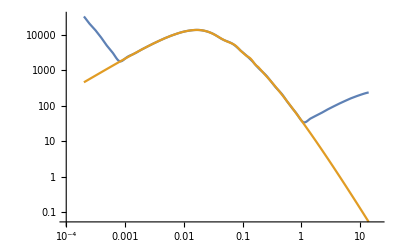

```mathematica
LogLogPlot[{Abs[Total[cn⟦All,1⟧k^cn⟦All,2⟧]],plin[k]},{k,2 10^-4,14},PlotRange->{{10^-4,20},Automatic}]
```

LogLinearPlot::prng: Value of option PlotRange -> {Automatic} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

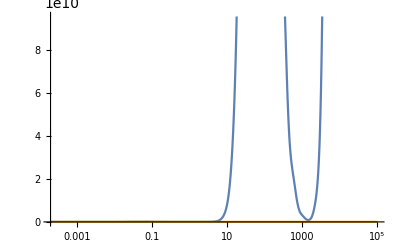

```mathematica
LogLinearPlot[{k^3 Abs[Total[cn⟦All,1⟧k^cn⟦All,2⟧]]^3,k^3 plin[k]^3},{k,2 10^-4,100000},PlotRange->{Automatic}]
```

LogLinearPlot::prng: Value of option PlotRange -> {Automatic} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

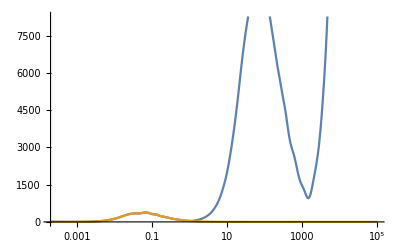

```mathematica
LogLinearPlot[{k Abs[Total[cn⟦All,1⟧k^cn⟦All,2⟧]],k plin[k]},{k,2 10^-4,100000},PlotRange->{Automatic}]
```

LogLinearPlot::prng: Value of option PlotRange -> {Automatic} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

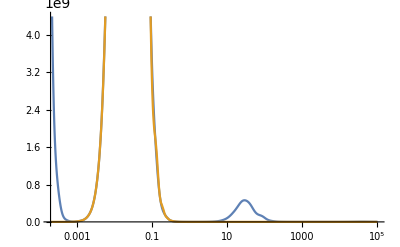

```mathematica
LogLinearPlot[{k Abs[Total[cn⟦All,1⟧k^cn⟦All,2⟧]]^3,k plin[k]^3},{k,2 10^-4,100000},PlotRange->{Automatic}]
```

FFT sum, and new basis sum, triangle 29. Bias -0.4, Diagrams are B222, B3211, B3212, B411

```mathematica
fftsum={179692,-112223317,3725768.615,6626690.8};
intsum={865662.182,-2917858295,22968133658,6431022.423};
```

```mathematica
fftsum//Total
```

-1.01691×10^8

```mathematica
intsum//Total
```

2.00576×10^10

```mathematica
(*bsub=Thread[biases->{0.77395605,0.43887844,0.85859792,0.69736803,0.09417735,0.97562235,0.7611397,0.78606431,0.12811363,0.45038594,0.37079802}];*)
(*bsub=Thread[biases->{0.77395605,0.43887844,0.85859792,0.69736803,0.33507761,0.97562235,0.7611397,0.78606431,0.12811363,0.45038594,0.37079802}];
bsub=Thread[biases->{2,1,0,0,1,0,0,0,0,0,0}];*)
bsub=Thread[biases->{1,1,1,1,0,0,0,0,0,0,0}]
ksub0=Thread[{k1,k2,k3}->{0.017221,0.017221,0.017221}];
ksub20=Thread[{k1,k2,k3}->{0.027562,0.027562,0.027562}];
ksub29=Thread[{k1,k2,k3}->{0.081,0.070261,0.027562}];
ksub124=Thread[{k1,k2,k3}->{0.091757,0.091757,0.048836}];
ksub130=Thread[{k1,k2,k3}->{0.124006,0.102501,0.048836}];
ksub181=Thread[{k1,k2,k3}->{0.091757,0.081,0.059539}];
ksub250=Thread[{k1,k2,k3}->{0.124006,0.081,0.070261}];
ksub655=Thread[{k1,k2,k3}->{0.210114,0.199356,0.124006}];
ksub824=Thread[{k1,k2,k3}->{0.220892,0.220892,0.220892}];
ksubren=Thread[{k1,k2,k3}->{0.001,0.001,0.001}];
ksub=ksub29
```

{b1→1,b2→1,b3→1,b4→1,b5→0,b6→0,b7→0,b8→0,b9→0,b10→0,b11→0}

{k1→0.081,k2→0.070261,k3→0.027562}

```mathematica
b5-b1+b2/.bsub
```

-0.2409

```mathematica
(*ksub=Thread[{k1,k2,k3}->{0.001,0.001,0.001}]*)
(*ksub=Thread[{k1,k2,k3}->{0.002,0.002,0.001}]*)(*ksub=Thread[{k1,k2,k3}->{0.002,0.0015,0.0015}]*)
(*ksub=Thread[{k1,k2,k3}->{0.003,0.002,0.0015}]*)
```

{k1→0.003,k2→0.002,k3→0.0015}

### 222

```mathematica
k222[k1_,k2_,q_]:=k222[k1,k2,q]=K2dsym[-q,q+k1]K2dsym[k1+q,k2-q]K2dsym[k2-q,q]
```

```mathematica
B222Integrand[k1_,k2_,q_] := B222Integrand[k1,k2,q]=8k222[k1,k2,q]*Plin[q]Plin[kmq[k2]]Plin[kpq[k1]]/.tb;
```

```mathematica
uv222=1/(4π)Integrate[Series[8k222[k1,k2,q]/.tb/.magrevreps,{q,∞,2}],{β,0,2π},{x,-1,1}]
```

-1/(21 q^2)4 (-b1+b2+b5)^2 (-42 b5 q^2+2 b2 (2 k1^2+2 k2^2+6 k3^2-21 q^2-4 k1 k2 y)+7 b1 (k1^2+k2^2-3 k3^2+6 q^2+4 k1 k2 y))

```mathematica
uv222/.yrep//FullSimplify
```

8 (-b1+b2+b5)^3+(4 (7 b1-8 b2) (-b1+b2+b5)^2 (k1^2+k2^2+k3^2))/(21 q^2)

```mathematica
t2 =B222Integrand[k1,k2,q]/.bsub/.magrevreps/.yrep/.ksub(*/.Plin[a_?NumericQ]-> plin[a]*)//Simplify;
```

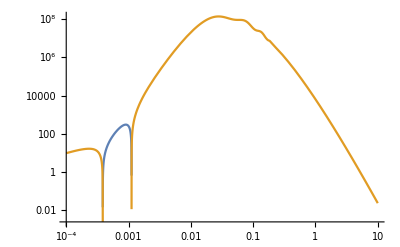

```mathematica
LogLogPlot[Evaluate[{q^2 t2,-q^2 t2}/.β->-π/4/.x->-1/2/.Plin->plin],{q,10^-4,10}]
```

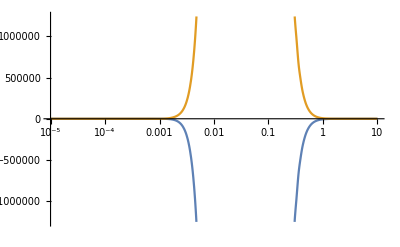

```mathematica
LogLinearPlot[Evaluate[{q^2 t2/.β->-π/4/.x->-1/2,-q^2 t2/.β->π/2/.x->0}/.Plin->plin],{q,10^-5,10}]
```

```mathematica
int222=NIntegrate[q^2/(2π)^3 t2/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-5,10},(*MaxPoints->200000,*)PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

-506401.

```mathematica
ksub
```

{k1→0.091757,k2→0.091757,k3→0.048836}

```mathematica
bsub
```

{b1→0.773956,b2→0.438878,b3→0.858598,b4→0.697368,b5→0.335078,b6→0.975622,b7→0.76114,b8→0.786064,b9→0.128114,b10→0.450386,b11→0.370798}

### 3211

```mathematica
k3211[k1_,k2_,q_]:=k3211[k1,k2,q]=K1d[k1] K2dsym[q,k2-q]K3dsym[-q,q-k2,-k1];
```

```mathematica
B3211Integrand[k1_,k2_,q_] :=B3211Integrand[k1,k2,q]= 6Plin[k1]k3211[k1,k2,q] Plin[q]Plin[kmq[k2]]/.tb
```

```mathematica
f3[k1_,k2_,k3_]=B3211Integrand[k1,k2,q]/.magrevreps/.yrep;
```

```mathematica
t3p1 =f3[k1,k2,k3]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
t3p2 = f3[k2,k3,k1]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
t3p3 = f3[k3,k1,k2]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
t3p4 =f3[k2,k1,k3]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
t3p5 = f3[k3,k2,k1]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
t3p6 = f3[k1,k3,k2]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
(*t3pfull=t3p1+t3p2+t3p3+t3p4+t3p5+t3p6;*)
t3pfull=(t3p1+t3p6)/(Plin[k1]/.ksub);
```

InterpolatingFunction::dmval: Input value {0.0000100028} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

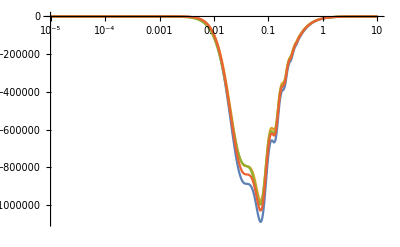

```mathematica
LogLinearPlot[Evaluate[{q^2 t3pfull/.β->π/4/.x->-1/2,q^2 t3pfull/.β->π/2/.x->0,q^2 t3pfull/.β->(3 π)/2/.x->1/3,q^2 t3pfull/.β->(2 π)/3/.x->-1/3}/.Plin->plin],{q,10^-5,10}]
```

```mathematica
fullint3211=NIntegrate[q^2/(2π)^3(t3pfull)/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-5,10},(*MaxPoints->200000,*)PrecisionGoal->6,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-10061.2

```mathematica
NIntegrate[q^2/(2π)^3(t3p3)/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-5,10},MaxPoints->200000,PrecisionGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-1.09434

```mathematica
int1=NIntegrate[q^2/(2π)^3(t3p1+t3p6)/.Plin-> Pinteger,{β,0,2π},{x,-1,1},{q,0.0001,0.4},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-4.4123

```mathematica
int2=NIntegrate[q^2/(2π)^3 t3p2/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100018 integrand evaluations. NIntegrate obtained -3.29669×10^6 and 4191.23 for the integral and error estimates.

-3.29669×10^6

```mathematica
int3=NIntegrate[q^2/(2π)^3 t3p3/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100010 integrand evaluations. NIntegrate obtained -3.57091×10^6 and 11386.2 for the integral and error estimates.

-3.57091×10^6

```mathematica
int4=NIntegrate[q^2/(2π)^3 t3p4/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100042 integrand evaluations. NIntegrate obtained -8.82483×10^6 and 5542.51 for the integral and error estimates.

-8.82483×10^6

```mathematica
int5=NIntegrate[q^2/(2π)^3 t3p5/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100060 integrand evaluations. NIntegrate obtained 3.70551×10^6 and 10630.9 for the integral and error estimates.

3.70551×10^6

```mathematica
int6=NIntegrate[q^2/(2π)^3 t3p6/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

-0.713759

```mathematica
int1+int2+int3+int4+int5+int6
```

-2.59794×10^7

```mathematica
{int1,int2,int3,int4,int5,int6}
```

{2.15038×10^6,2.30707×10^6,2.76814×10^6,2.4124×10^6,2.77275×10^6,2.05322×10^6}

```mathematica
t3p1 =f3[k1,k2,k3]/Plin[k1]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
t3p2 = f3[k2,k3,k1]/Plin[k2]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
t3p3 = f3[k3,k1,k2]/Plin[k3]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
t3p4 =f3[k2,k1,k3]/Plin[k2]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
t3p5 = f3[k3,k2,k1]/Plin[k3]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
t3p6 = f3[k1,k3,k2]/Plin[k1]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
```

Renormalization by stochastic counterterm. In real space there are 4 different conditions on the integral

```mathematica
K1r[k1]Plin[k1](Subscript[d, 3]+Subscript[d, 4] μ1^2+Subscript[d, 5] k1^2 +Subscript[d, 6](k2^2+k3^2) +Subscript[d, 7]((k2^2-k3^2)^2)/k1^2+Subscript[d, 8] k1^2 μ1^2 +Subscript[d, 9](k3^2 μ2^2+k2^2 μ3^2)+Subscript[d, 10] k1^2 (μ2^2+μ3^2) +Subscript[d, 11](k2^2 μ2^2+k3^2 μ3^2) +Subscript[d, 12] μ1^2(k2^2+k3^2)  +Subscript[d, 13]((k2^2-k3^2)^2 (μ2^2+μ3^2))/k1^2+Subscript[d, 14]((k2^2-k3^2) (k2^2 μ2^2-k3^2 μ3^2))/k1^2 +Subscript[d, 15] k1^2 μ1^4+Subscript[d, 16] μ1^2 (k2^2 μ2^2+k3^2 μ3^2) )/.tb/.μ1->0/.μ2->0/.μ3->0
```

b1 Plin[k1] (d_3+k1^2 d_5+(k2^2+k3^2) d_6+((k2^2-k3^2)^2 d_7)/k1^2)

So we will choose 4 different triangles to solve for the d’s, at small values of k

```mathematica
kren={{0.001,0.001,0.001},{0.002,0.002,0.001},{0.002,0.0015,0.0015},{0.003,0.002,0.0015}};
```

```mathematica
intren1=-10063.918228908558;
intren2=-10061.921741354427;
intren3=-10062.159009542605;
intren4=-10061.218671876506;
```

```mathematica
reneqs={intren1+Subscript[d, 3]+kren⟦1,1⟧^2 Subscript[d, 5]+(kren⟦1,2⟧^2+kren⟦1,3⟧^2) Subscript[d, 6]+((kren⟦1,2⟧^2-kren⟦1,3⟧^2)^2)/kren⟦1,1⟧^2 Subscript[d, 7]==0,intren2+Subscript[d, 3]+kren⟦2,1⟧^2 Subscript[d, 5]+(kren⟦2,2⟧^2+kren⟦2,3⟧^2) Subscript[d, 6]+((kren⟦2,2⟧^2-kren⟦2,3⟧^2)^2)/kren⟦2,1⟧^2 Subscript[d, 7]==0,intren3+Subscript[d, 3]+kren⟦3,1⟧^2 Subscript[d, 5]+(kren⟦3,2⟧^2+kren⟦3,3⟧^2) Subscript[d, 6]+((kren⟦3,2⟧^2-kren⟦3,3⟧^2)^2)/kren⟦3,1⟧^2 Subscript[d, 7]==0,intren4+Subscript[d, 3]+kren⟦4,1⟧^2 Subscript[d, 5]+(kren⟦4,2⟧^2+kren⟦4,3⟧^2) Subscript[d, 6]+((kren⟦4,2⟧^2-kren⟦4,3⟧^2)^2)/kren⟦4,1⟧^2 Subscript[d, 7]==0};
```

```mathematica
Solve[reneqs,{Subscript[d, 3], Subscript[d, 5], Subscript[d, 6],Subscript[d, 7]}]
```

{{d_3→10065.5,d_5→91545.2,d_6→-813542.,d_7→75334.6}}

### 3212

```mathematica
uvK3K2=1/(1890 q^2)(3 b1 (k1^2-130 q^2)+2 b3 (-32 k1^2+705 q^2)+30 ((63 b10-34 b2-42 b5+110 b6) q^2+b8 (-32 k1^2+82 q^2)));
```

```mathematica
k3212[k1_,k2_,q_]:=k3212[k1,k2,q]=K1d[k2]K2dsym[k1,k2](K3dsym[k1,q,-q]-uvK3K2)
```

```mathematica
B3212Integrand[k1_,k2_,q_] :=B3212Integrand[k1,k2,q] = 6Plin[k1]Plin[k2]Plin[q]k3212[k1,k2,q]/.tb
```

```mathematica
f3[k1_,k2_,k3_]=B3212Integrand[k1,k2,q]/.magrevreps/.yrep;
```

```mathematica
t3p1 =f3[k1,k2,k3]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
t3p2 = f3[k2,k3,k1]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
t3p3 = f3[k3,k1,k2]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
t3p4 =f3[k2,k1,k3]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
t3p5 = f3[k3,k2,k1]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
t3p6 = f3[k1,k3,k2]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
```

```mathematica
fullint3212=NIntegrate[q^2/(2π)^3(t3p1+t3p2+t3p3+t3p4+t3p5+t3p6)/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-3,10},MaxPoints->200000,PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

-2.07271×10^6

```mathematica
NIntegrate[q^2/(2π)^3(t3p1+t3p6)/.Plin-> Pinteger,{β,0,2π},{x,-1,1},{q,0.0001,4},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-4.66032

```mathematica
int1=NIntegrate[q^2/(2π)^3(t3p1+t3p6)/.Plin-> Pinteger,{β,0,2π},{x,-1,1},{q,0.0001,0.4},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-4.4123

```mathematica
int2=NIntegrate[q^2/(2π)^3 t3p2/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100018 integrand evaluations. NIntegrate obtained -3.29669×10^6 and 4191.23 for the integral and error estimates.

-3.29669×10^6

```mathematica
int3=NIntegrate[q^2/(2π)^3 t3p3/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100010 integrand evaluations. NIntegrate obtained -3.57091×10^6 and 11386.2 for the integral and error estimates.

-3.57091×10^6

```mathematica
int4=NIntegrate[q^2/(2π)^3 t3p4/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100042 integrand evaluations. NIntegrate obtained -8.82483×10^6 and 5542.51 for the integral and error estimates.

-8.82483×10^6

```mathematica
int5=NIntegrate[q^2/(2π)^3 t3p5/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100060 integrand evaluations. NIntegrate obtained 3.70551×10^6 and 10630.9 for the integral and error estimates.

3.70551×10^6

```mathematica
int6=NIntegrate[q^2/(2π)^3 t3p6/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

-0.713759

```mathematica
int1+int2+int3+int4+int5+int6
```

-2.59794×10^7

```mathematica
{int1,int2,int3,int4,int5,int6}
```

{2.15038×10^6,2.30707×10^6,2.76814×10^6,2.4124×10^6,2.77275×10^6,2.05322×10^6}

Renormalization by stochastic counterterm. In real space there are 4 different conditions on the integral

```mathematica
K1r[k1]Plin[k1](Subscript[d, 3]+Subscript[d, 4] μ1^2+Subscript[d, 5] k1^2 +Subscript[d, 6](k2^2+k3^2) +Subscript[d, 7]((k2^2-k3^2)^2)/k1^2+Subscript[d, 8] k1^2 μ1^2 +Subscript[d, 9](k3^2 μ2^2+k2^2 μ3^2)+Subscript[d, 10] k1^2 (μ2^2+μ3^2) +Subscript[d, 11](k2^2 μ2^2+k3^2 μ3^2) +Subscript[d, 12] μ1^2(k2^2+k3^2)  +Subscript[d, 13]((k2^2-k3^2)^2 (μ2^2+μ3^2))/k1^2+Subscript[d, 14]((k2^2-k3^2) (k2^2 μ2^2-k3^2 μ3^2))/k1^2 +Subscript[d, 15] k1^2 μ1^4+Subscript[d, 16] μ1^2 (k2^2 μ2^2+k3^2 μ3^2) )/.tb/.μ1->0/.μ2->0/.μ3->0
```

b1 Plin[k1] (d_3+k1^2 d_5+(k2^2+k3^2) d_6+((k2^2-k3^2)^2 d_7)/k1^2)

So we will choose 4 different triangles to solve for the d’s, at small values of k

```mathematica
reneqs={I1+Subscript[d, 3]+k11^2 Subscript[d, 5]+(k12^2+k13^2) Subscript[d, 6]+((k12^2-k13^2)^2 Subscript[d, 7])/k11^2==0,I2+Subscript[d, 3]+k21^2 Subscript[d, 5]+(k22^2+k23^2) Subscript[d, 6]+((k22^2-k23^2)^2 Subscript[d, 7])/k21^2==0,I3+Subscript[d, 3]+k31^2 Subscript[d, 5]+(k32^2+k33^2) Subscript[d, 6]+((k32^2-k33^2)^2 Subscript[d, 7])/k31^2==0,I4+Subscript[d, 3]+k41^2 Subscript[d, 5]+(k42^2+k43^2) Subscript[d, 6]+((k42^2-k43^2)^2 Subscript[d, 7])/k41^2==0};
```

### 411

```mathematica
B411Integrand[k1,k2,q]=<<"tables/B411realspacek1k2.m"
```

12 b1^2 ((b10 (k2^2 q^2 (k1mq^2+k1pq^2-k2^2+k3^2-2 q^2)-1+k1^2 1))/(8 k1^2 k2^2 q^2)-(b6 1)/1+7+1+(b9 (1))/(169344 k1^4 7 k3pq^2 q^4)) 1 Plin[k2] Plin[q]
 |  |  |  |

```mathematica
UV0=<<"tables/B411realspacek1k2UV0.m";
UV2=<<"tables/B411realspacek1k2UV2.m";
```

Integrate

```mathematica
f4[k1_,k2_,k3_]=(B411Integrand[k1,k2,q]-UV0-UV2)/.magrevreps/.yrep/.bsub
```

1/(4410 k1^2 k2^2 k3^2)-1+12 3 (1/(18816 7 (k2^2+q^2+2 k2 q (1+1)))+1+1+(1+7+1)/(1862784 9 (1)))
 |  |  |  |

```mathematica
(*fnew=f4[k1,k2,k3]/.β->0/.x->0/.Plin->Function[x,1]//Simplify;*)
```

```mathematica
(*f4subUV[k1_,k2_,k3_]=(B411Integrand[k1,k2,q]-UV0-UV2)/.magrevreps/.yrep;*)
```

```mathematica
t4p1 =f4[k1,k2,k3]/.bsub/.magrevreps/.yrep/.ksub(*/.Plin[a_?NumericQ]-> plin[a]*)//Simplify;
t4p2 = f4[k2,k3,k1]/.bsub/.magrevreps/.yrep/.ksub(*/.Plin[a_?NumericQ]-> plin[a]*)//Simplify;
t4p3 = f4[k3,k1,k2]/.bsub/.magrevreps/.yrep/.ksub(*/.Plin[a_?NumericQ]-> plin[a]*)//Simplify;
```

```mathematica
F1=B411Integrand[k1,k2,q]/.bsub/.magrevreps/.yrep/.ksub/.Plin[a_?NumericQ]-> plin[a]//Simplify//Chop;
F2=UV0/.bsub/.magrevreps/.yrep/.ksub/.Plin[a_?NumericQ]-> plin[a]//Simplify//Chop;
F3=UV2/.bsub/.magrevreps/.yrep/.ksub/.Plin[a_?NumericQ]-> plin[a]//Simplify//Chop;
```

One has to be careful in integrating far, since numerical imprecisions make spurious divergences for high q

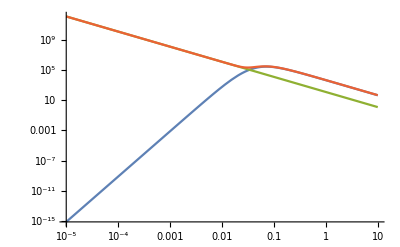

```mathematica
LogLogPlot[Evaluate[{Abs[F1],Abs[F2],Abs[F3],Abs[F1-F2-F3]}/.{β->0,x->0.}/.Plin-> Function[x,1]],{q,0.00001,10}]
```

InterpolatingFunction::dmval: Input value {0.0000100028} lies outside the range of data in the interpolating function. Extrapolation will be used.

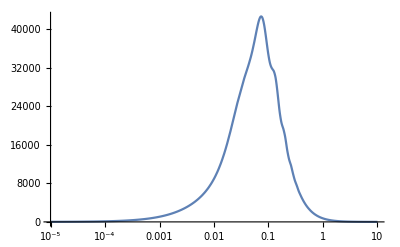

```mathematica
LogLinearPlot[q^2/(2π)^3 t4p1/.Plin-> plin/.{β->0,x->0.},{q,10^-5,10}]
```

```mathematica
fullint411=NIntegrate[q^2/(2π)^3(t4p1+t4p2+t4p3)/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-5,10},MaxPoints->200000,PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 200051 integrand evaluations. NIntegrate obtained -383102. and 663.531 for the integral and error estimates.

-383102.

```mathematica
int1=NIntegrate[q^2/(2π)^3 t4p1/.Plin-> pfft,{β,0,2π},{x,-1,1},{q,10^-4,0.4},MaxPoints->200000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

0.391796

```mathematica
int2=NIntegrate[q^2/(2π)^3 t4p2/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-4,10},MaxPoints->200000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

0.00258554

```mathematica
int3=NIntegrate[q^2/(2π)^3 t4p3/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-4,10},MaxPoints->200000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

0.00258554

```mathematica
int411=int1+int2+int3
```

```mathematica
-0.021234867118799315 2
```

-0.0424697

```mathematica
-94854.02971241245-351635.51119745645-220502.23956838233
```

-666992.

```mathematica
Plin[k1]Plin[k2]σ2 ser2B411tabintfin/.Plin->plin/.bsub/.yrep/.ksub
```

-1.8311×10^6

#### Sum

```mathematica
{int222,fullint3211,fullint3212,fullint411}
```

{-1.08971×10^6,-3.06388×10^7,-2.07271×10^6,-2.01441×10^10}

```mathematica
{int222,fullint3211,fullint3212,fullint411}//Total
```

-2.01779×10^10

## Numerical Integration, redshift space

```mathematica
plindat=Import["../patchy_pk.dat"];
plin=Interpolation[plindat];
```

```mathematica
angint[a_,b_,c_,d_]=((1+(-1)^a) (1+(-1)^c) (1+(-1)^d) Gamma[(1+a)/2] Gamma[1+b/2] Gamma[(1+c)/2] Gamma[(1+d)/2])/(16 π Gamma[1/2 (3+a+b)] Gamma[1/2 (2+c+d)])
```

((1+(-1)^a) (1+(-1)^c) (1+(-1)^d) Gamma[(1+a)/2] Gamma[1+b/2] Gamma[(1+c)/2] Gamma[(1+d)/2])/(16 π Gamma[1/2 (3+a+b)] Gamma[1/2 (2+c+d)])

```mathematica
bsub=Thread[biases-> {1,1,1,1,0,0,0,0,0,0,0,0,0,0,0}];
(*bsub=Thread[biases->{0.77395605,0.43887844,0.85859792,0.69736803,0.33507761,0.97562235,0.7611397,0.78606431,0.12811363,0.45038594,0.37079802}];*)
(*bsub=Thread[biases->{1,1,1,1,0,0,0,0,0,0,0}];*)
fsub={f1->0.7770083924901465};
ksub0=Thread[{k1,k2,k3}->{0.017221,0.017221,0.017221}];
ksub20=Thread[{k1,k2,k3}->{0.027562,0.027562,0.027562}];
ksub29=Thread[{k1,k2,k3}->{0.081,0.070261,0.027562}];
ksub50=Thread[{k1,k2,k3}->{0.188592,0.188592,0.027562}];
ksub130=Thread[{k1,k2,k3}->{0.124006,0.102501,0.048836}];
ksub181=Thread[{k1,k2,k3}->{0.091757,0.081,0.059539}];
ksub250=Thread[{k1,k2,k3}->{0.124006,0.081,0.070261}];
ksub655=Thread[{k1,k2,k3}->{0.210114,0.199356,0.124006}];
ksub824=Thread[{k1,k2,k3}->{0.220892,0.220892,0.220892}];
ksubren=Thread[{k1,k2,k3}->{0.001,0.001,0.001}];
ksub=ksub20
```

{k1→0.027562,k2→0.027562,k3→0.027562}

```mathematica
(*ksub=Thread[{k1,k2,k3}->{0.001,0.001,0.001}]*)
(*ksub=Thread[{k1,k2,k3}->{0.002,0.002,0.001}]*)(*ksub=Thread[{k1,k2,k3}->{0.002,0.0015,0.0015}]*)
(*ksub=Thread[{k1,k2,k3}->{0.003,0.002,0.0015}]*)
```

{k1→0.001,k2→0.001,k3→0.001}

Results of check in redshift space:
3212 works for random biases, also in FFTLog (bias -0.4)
222 works for random biases in FFTLog (bias -0.4) after NIntegrate subtraction (check another triangle to be sure), not integer

### 222

#### Use kernels

```mathematica
k222[k1_,k2_,q_]:=k222[k1,k2,q]=K2rsym[-q,q+k1]K2rsym[k1+q,k2-q]K2rsym[k2-q,q]
```

```mathematica
B222Integrand[k1_,k2_,q_] := B222Integrand[k1,k2,q]=8k222[k1,k2,q]*Plin[q]Plin[kmq[k2]]Plin[kpq[k1]]/.tb;
```

```mathematica
(*uv222=1/(4π)Integrate[Series[8k222[k1,k2,q]/.tb/.magrevreps,{q,∞,2}],{β,0,2π},{x,-1,1}]*)
```

```mathematica
(*uv222/.yrep//FullSimplify*)
```

```mathematica
(*μtoangles222θ={μ1->Cos[θ],μ2->y Cos[θ]+√(1-y^2) Sin[θ] Sin[ϕ],μ0->x Cos[θ]+√(1-x^2) Cos[β] Cos[ϕ] Sin[θ]+√(1-x^2) Sin[β] Sin[θ] Sin[ϕ]};*)
μtoangles222μ={μ1->μ,μ2->y μ+√(1-y^2) √(1-μ^2) Sin[ϕ],μ0->x μ+√(1-x^2) Cos[β] Cos[ϕ] √(1-μ^2)+√(1-x^2) Sin[β] √(1-μ^2) Sin[ϕ]}//Simplify;
```

Try to Nintegrate also in θ and ϕ, to get the monopole

```mathematica
t2 =B222Integrand[k1,k2,q]/.bsub/.fsub/.magrevreps/.μtoangles222μ/.yrep/.ksub(*/.Plin[a_?NumericQ]-> plin[a]*)(*//Simplify*);
```

InterpolatingFunction::dmval: Input value {0.0000100028} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

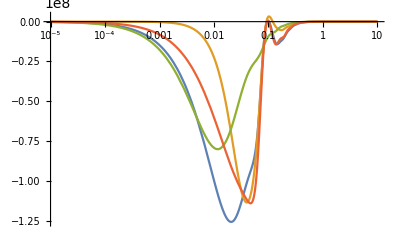

```mathematica
LogLinearPlot[Evaluate[{q^2 t2/.{β->π/4,x->-1/2,θ->0,ϕ->0,μ->0},q^2 t2/.{β->π/2,x->0,θ->0,ϕ->π/4,μ->1},q^2 t2/.{β->(3 π)/2,x->1/3,θ->π/3,ϕ->0,μ->1/2},q^2 t2/.{β->(2 π)/3,x->-1/3,θ->π/2,ϕ->0,μ->-1/3}}/.Plin->plin],{q,10^-5,10}]
```

```mathematica
(*int222=NIntegrate[q^2/(2π)^3 t2/(4π)Sin[θ]/.Plin-> plin,{θ,0,π},{ϕ,0,2π},{β,0,2π},{x,-1,1},{q,10^-5,10},(*MaxPoints->200000,*)PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]*)
```

```mathematica
int222=NIntegrate[q^2/(2π)^3 t2/(4π)/.Plin-> plin,{μ,-1,1},{ϕ,0,2π},{β,0,2π},{x,-1,1},{q,10^-5,10},(*MaxPoints->200000,*)PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.45521×10^6 and 11996.6 for the integral and error estimates.

1.45521×10^6

```mathematica
ksub-ksub181
```

{0,0,0}

#### Load and NIntegrate

```mathematica
Bint=<<"tables/B222monotoint.m";
```

```mathematica
newt2=(Bint)/.bsub/.fsub/.magrevreps/.yrep/.ksub(*/.Plin[a_?NumericQ]-> plin[a]*)//Simplify;
```

InterpolatingFunction::dmval: Input value {0.0000100028} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

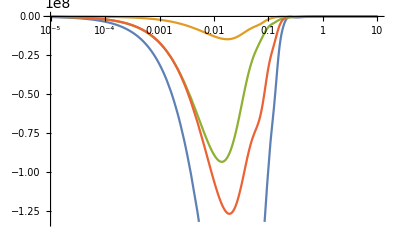

```mathematica
LogLinearPlot[Evaluate[{q^2 newt2/.{β->π/4,x->-1/2},q^2 newt2/.{β->π/2,x->0},q^2 newt2/.{β->(3 π)/2,x->1/3},q^2 newt2/.{β->(2 π)/3,x->-1/3}}/.Plin->plin],{q,10^-5,10}]
```

```mathematica
newint222=NIntegrate[q^2/(2π)^3 newt2/.Plin-> plin,{x,-1,1},{β,0,2π},{q,10^-5,10},(*MaxPoints->200000,*)PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-2.54953×10^6

```mathematica
ksub-ksub655
```

{0,0,0}

```mathematica
1.2025820475678837*^6-(-506702.29564213415)
```

1.70928×10^6

```mathematica
t2UV1=(Bint)/.bsub/.fsub/.magrevreps/.yrep/.{k1->0.0001,k2->0.0001,k3->0.0001}(*/.Plin[a_?NumericQ]-> plin[a]*)//Simplify;
t2UV2=(Bint)/.bsub/.fsub/.magrevreps/.yrep/.{k1->0.004,k2->0.004,k3->0.004}(*/.Plin[a_?NumericQ]-> plin[a]*)//Simplify;
```

```mathematica
-2.8464541743368176*^6-(-506702.29564213415)
```

-2.33975×10^6

```mathematica
int2UV1=NIntegrate[q^2/(2π)^3 t2UV1/.Plin-> plin,{x,-1,1},{β,0,2π},{q,10^-5,10},(*MaxPoints->200000,*)PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

-506702.

```mathematica
int2UV2=NIntegrate[q^2/(2π)^3 t2UV2/.Plin-> plin,{x,-1,1},{β,0,2π},{q,10^-5,10},(*MaxPoints->200000,*)PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

-504866.+5.49886×10^-14 ⅈ

```mathematica
solren=Solve[{r1+r2 3 (0.0001)^2==int2UV1,r1+r2 3 (0.004)^2==int2UV2},{r1,r2}]//Flatten
```

{r1→-506703.-3.43893×10^-17 ⅈ,r2→3.8283×10^7+1.14631×10^-9 ⅈ}

```mathematica
newint222-(r1+r2 (k1^2+k2^2+k3^2))/.solren/.ksub
```

-4.3171×10^6-3.08072×10^-11 ⅈ

### 3211

#### Full kernels

```mathematica
k3211[k1_,k2_,q_]:=k3211[k1,k2,q]=K1r[k1] K2rsym[q,k2-q]K3rsym[-q,q-k2,-k1];
```

```mathematica
B3211Integrand[k1_,k2_,q_] :=B3211Integrand[k1,k2,q]= 6Plin[k1]k3211[k1,k2,q] Plin[q]Plin[kmq[k2]]/.tb
```

```mathematica
μtoanglesμ={μ1->μ,μ2->y μ+√(1-y^2) √(1-μ^2) Sin[ϕ],μ0->x μ+√(1-x^2) Cos[β] Cos[ϕ] √(1-μ^2)+√(1-x^2) Sin[β] √(1-μ^2) Sin[ϕ]}//Simplify;
```

```mathematica
f3[k1_,k2_,k3_]=Evaluate[B3211Integrand[k1,k2,q]/.bsub/.fsub/.magrevreps/.μtoanglesμ/.yrep];
```

```mathematica
t3p1 =f3[k1,k2,k3]/.ksub;
t3p2 = f3[k2,k3,k1]/.ksub;
t3p3 = f3[k3,k1,k2]/.ksub;
t3p4 =f3[k2,k1,k3]/.ksub;
t3p5 = f3[k3,k2,k1]/.ksub;
t3p6 = f3[k1,k3,k2]/.ksub;
t3pfull=t3p1+t3p2+t3p3+t3p4+t3p5+t3p6;
(*t3pfull=(t3p1+t3p6)/(Plin[k1]/.ksub);*)
```

InterpolatingFunction::dmval: Input value {0.000010003} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

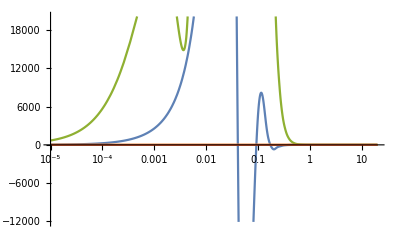

```mathematica
LogLinearPlot[Evaluate[{q^2 t3pfull/.{β->π/4,x->-1/2,μ->1/2,ϕ->0},q^2 t3pfull/.{β->π/2,x->0,μ->0,ϕ->π/2},q^2 t3pfull/.{β->(3 π)/2,x->1/3,μ->1,ϕ->π/3},q^2 t3pfull/.{β->(2 π)/3,x->-1/3,μ->0,ϕ->π}}/.Plin->plin],{q,10^-5,20}]
```

```mathematica
fullint3211=NIntegrate[q^2/(2π)^3 t3pfull/(4π)/.Plin-> plin,{μ,-1,1},{ϕ,0,2π},{x,-1,1},{β,0,2π},{q,10^-5,10},(*MaxPoints->200000,*)PrecisionGoal->2,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 200175 integrand evaluations. NIntegrate obtained -3.25624×10^7 and 1.72624×10^6 for the integral and error estimates.

-3.25624×10^7

```mathematica
int1=NIntegrate[q^2/(2π)^3(t3p1)/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-5,20},MaxPoints->200000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::inumr: The integrand «1» has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{-1,1},{1/100000,20}}.

NIntegrate[(q^2 t3p1)/(2 π)^3/.Plin→plin,{β,0,2 π},{x,-1,1},{q,1/10^5,20},MaxPoints→200000,AccuracyGoal→3,Method→{Automatic,SymbolicProcessing→0}]

```mathematica
int2=NIntegrate[q^2/(2π)^3 t3p2/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100018 integrand evaluations. NIntegrate obtained -3.29669×10^6 and 4191.23 for the integral and error estimates.

-3.29669×10^6

```mathematica
int3=NIntegrate[q^2/(2π)^3 t3p3/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100010 integrand evaluations. NIntegrate obtained -3.57091×10^6 and 11386.2 for the integral and error estimates.

-3.57091×10^6

```mathematica
int4=NIntegrate[q^2/(2π)^3 t3p4/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100042 integrand evaluations. NIntegrate obtained -8.82483×10^6 and 5542.51 for the integral and error estimates.

-8.82483×10^6

```mathematica
int5=NIntegrate[q^2/(2π)^3 t3p5/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100060 integrand evaluations. NIntegrate obtained 3.70551×10^6 and 10630.9 for the integral and error estimates.

3.70551×10^6

```mathematica
int6=NIntegrate[q^2/(2π)^3 t3p6/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

-0.713759

```mathematica
int1+int2+int3+int4+int5+int6
```

-2.59794×10^7

```mathematica
{int1,int2,int3,int4,int5,int6}
```

{2.15038×10^6,2.30707×10^6,2.76814×10^6,2.4124×10^6,2.77275×10^6,2.05322×10^6}

#### Load and NIntegrate

```mathematica
Bint=<<"tables/B3211monotoint.m";
```

```mathematica
Clear[newf3];
newf3[k1_,k2_,k3_]=Bint/.bsub/.fsub/.yrep;
```

```mathematica
(*ksub={k1->0.001,k2->0.001,k3->0.001};*)
```

```mathematica
t3p1 =newf3[k1,k2,k3]/.ksub(*//Simplify*);
(*t3p2 = newf3[k2,k3,k1]/.ksub(*//Simplify*);
t3p3 = newf3[k3,k1,k2]/.ksub(*//Simplify*);
t3p4 =newf3[k2,k1,k3]/.ksub(*//Simplify*);
t3p5 = newf3[k3,k2,k1]/.ksub(*//Simplify*);
t3p6 = newf3[k1,k3,k2]/.ksub(*//Simplify*);*)
```

```mathematica
t3pfull=t3p1+t3p2+t3p3+t3p4+t3p5+t3p6;
```

InterpolatingFunction::dmval: Input value {0.0000100028} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

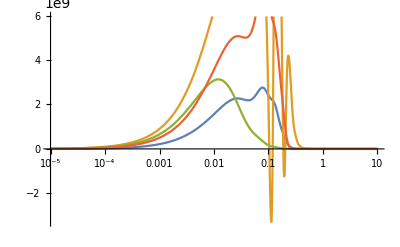

```mathematica
LogLinearPlot[Evaluate[{q^2 t3pfull/.{β->π/4,x->-1/2,μ->1/2,ϕ->0},q^2 t3pfull/.{β->π/2,x->0,μ->0,ϕ->π/2},q^2 t3pfull/.{β->(3 π)/2,x->1/3,μ->1,ϕ->π/3},q^2 t3pfull/.{β->(2 π)/3,x->-1/3,μ->0,ϕ->π}}/.Plin->plin],{q,10^-5,10}]
```

```mathematica
(*fullint3211=NIntegrate[q^2/(2π)^3(t3pfull)/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-3,10},(*MaxPoints->200000,*)PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]*)
```

```mathematica
int1=NIntegrate[q^2/(2π)^3(t3p1)/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-4,10},MaxPoints->200000,PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-6.8803×10^7

```mathematica
6 -6.88029851561665*^7
```

-6.8803×10^7

```mathematica
int2=NIntegrate[q^2/(2π)^3(t3p2)/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-4,5},MaxPoints->200000,PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.45345×10^6

```mathematica
int3=NIntegrate[q^2/(2π)^3(t3p3)/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-4,5},MaxPoints->200000,PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

4.65535×10^6

```mathematica
int4=NIntegrate[q^2/(2π)^3(t3p4)/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-4,5},MaxPoints->200000,PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

172541.

```mathematica
int5=NIntegrate[q^2/(2π)^3(t3p5)/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-4,5},MaxPoints->200000,PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

7.59497×10^6

```mathematica
int6=NIntegrate[q^2/(2π)^3(t3p6)/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-4,5},MaxPoints->200000,PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

293159.

```mathematica
intfull=int1+int2+int3+int4+int5+int6
```

1.42627×10^7

```mathematica
ksub-ksub250
```

{0,0,0}

```mathematica
fsub
```

{f1→0.7}

```mathematica
Solve[fullint3211-6 plin[0.001]d1==0,d1]
```

{{d1→-6527.22}}

```mathematica
ksub-ksub824
```

{0,0,0}

Try to renormalize subtracting only the k^0 term, at a small side triangle

```mathematica
t3ren=newf3[k1,k2,k3]/Plin[k1]/.{k1->0.001,k2->0.001,k3->0.001}(*//Simplify*);
```

InterpolatingFunction::dmval: Input value {0.0000100028} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

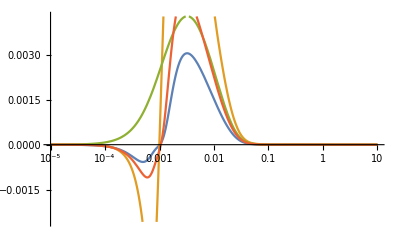

```mathematica
LogLinearPlot[Evaluate[{q^2 t3ren/.{β->π/4,x->-1/2,μ->1/2,ϕ->0},q^2 t3ren/.{β->π/2,x->0,μ->0,ϕ->π/2},q^2 t3ren/.{β->(3 π)/2,x->1/3,μ->1,ϕ->π/3},q^2 t3ren/.{β->(2 π)/3,x->-1/3,μ->0,ϕ->π}}/.Plin->plin],{q,10^-5,10}]
```

```mathematica
t3ren=NIntegrate[q^2/(2π)^3(t3ren)/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-5,10},MaxPoints->200000,PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 200022 integrand evaluations. NIntegrate obtained 2.38617×10^-6 and 3.73991×10^-9 for the integral and error estimates.

2.38617×10^-6

Renormalization by stochastic counterterm. In real space there are 4 different conditions on the integral

```mathematica
K1r[k1]Plin[k1](Subscript[d, 3]+Subscript[d, 4] μ1^2+Subscript[d, 5] k1^2 +Subscript[d, 6](k2^2+k3^2) +Subscript[d, 7]((k2^2-k3^2)^2)/k1^2+Subscript[d, 8] k1^2 μ1^2 +Subscript[d, 9](k3^2 μ2^2+k2^2 μ3^2)+Subscript[d, 10] k1^2 (μ2^2+μ3^2) +Subscript[d, 11](k2^2 μ2^2+k3^2 μ3^2) +Subscript[d, 12] μ1^2(k2^2+k3^2)  +Subscript[d, 13]((k2^2-k3^2)^2 (μ2^2+μ3^2))/k1^2+Subscript[d, 14]((k2^2-k3^2) (k2^2 μ2^2-k3^2 μ3^2))/k1^2 +Subscript[d, 15] k1^2 μ1^4+Subscript[d, 16] μ1^2 (k2^2 μ2^2+k3^2 μ3^2) )/.tb/.μ1->0/.μ2->0/.μ3->0
```

b1 Plin[k1] (d_3+k1^2 d_5+(k2^2+k3^2) d_6+((k2^2-k3^2)^2 d_7)/k1^2)

So we will choose 4 different triangles to solve for the d’s, at small values of k

```mathematica
kren={{0.001,0.001,0.001},{0.002,0.002,0.001},{0.002,0.0015,0.0015},{0.003,0.002,0.0015}};
```

```mathematica
intren1=-10063.918228908558;
intren2=-10061.921741354427;
intren3=-10062.159009542605;
intren4=-10061.218671876506;
```

```mathematica
reneqs={intren1+Subscript[d, 3]+kren⟦1,1⟧^2 Subscript[d, 5]+(kren⟦1,2⟧^2+kren⟦1,3⟧^2) Subscript[d, 6]+((kren⟦1,2⟧^2-kren⟦1,3⟧^2)^2)/kren⟦1,1⟧^2 Subscript[d, 7]==0,intren2+Subscript[d, 3]+kren⟦2,1⟧^2 Subscript[d, 5]+(kren⟦2,2⟧^2+kren⟦2,3⟧^2) Subscript[d, 6]+((kren⟦2,2⟧^2-kren⟦2,3⟧^2)^2)/kren⟦2,1⟧^2 Subscript[d, 7]==0,intren3+Subscript[d, 3]+kren⟦3,1⟧^2 Subscript[d, 5]+(kren⟦3,2⟧^2+kren⟦3,3⟧^2) Subscript[d, 6]+((kren⟦3,2⟧^2-kren⟦3,3⟧^2)^2)/kren⟦3,1⟧^2 Subscript[d, 7]==0,intren4+Subscript[d, 3]+kren⟦4,1⟧^2 Subscript[d, 5]+(kren⟦4,2⟧^2+kren⟦4,3⟧^2) Subscript[d, 6]+((kren⟦4,2⟧^2-kren⟦4,3⟧^2)^2)/kren⟦4,1⟧^2 Subscript[d, 7]==0};
```

```mathematica
Solve[reneqs,{Subscript[d, 3], Subscript[d, 5], Subscript[d, 6],Subscript[d, 7]}]
```

{{d_3→10065.5,d_5→91545.2,d_6→-813542.,d_7→75334.6}}

### 3212

```mathematica
B3212intp1=<<"tables/B3212subk2.m";
```

```mathematica
f3[k1_,k2_,k3_]=Evaluate[(B3212intp1/.ν->0)Plin[k1]Plin[k2]Plin[q]/.fsub/.bsub/.magrevreps/.yrep]
```

(-0.884045+0.48996911/k2^2+2258) Plin[k1] Plin[k2] Plin[q]
 |  |  |  |

```mathematica
t3p1 =f3[k1,k2,k3]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
t3p2 = f3[k2,k3,k1]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
t3p3 = f3[k3,k1,k2]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
t3p4 =f3[k2,k1,k3]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
t3p5 = f3[k3,k2,k1]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
t3p6 = f3[k1,k3,k2]/.bsub/.magrevreps/.yrep/.ksub//Simplify;
```

InterpolatingFunction::dmval: Input value {0.0000100034} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

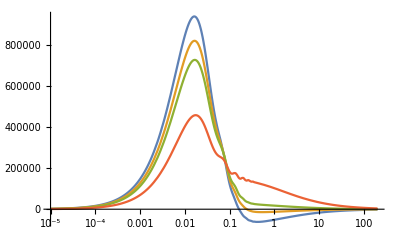

```mathematica
LogLinearPlot[Evaluate[{q^2/(2π)^3 t3p1/.{β->0,x->0.},q^2/(2π)^3 t3p1/.{β->π/2,x->1/2},q^2/(2π)^3 t3p1/.{β->-π/2,x->-2/3},q^2/(2π)^3 t3p1/.{β->π/3,x->1}}/.Plin-> plin],{q,10^-5,200}]
```

```mathematica
fullint3212=NIntegrate[q^2/(2π)^3(t3p1+t3p2+t3p3+t3p4+t3p5+t3p6)/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-5,200},MaxPoints->200000,PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

3.85942×10^6

```mathematica
NIntegrate[q^2/(2π)^3(t3p1+t3p6)/.Plin-> Pinteger,{β,0,2π},{x,-1,1},{q,0.0001,4},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-4.66032

```mathematica
int1=NIntegrate[q^2/(2π)^3(t3p1+t3p6)/.Plin-> Pinteger,{β,0,2π},{x,-1,1},{q,0.0001,0.4},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-4.4123

```mathematica
int2=NIntegrate[q^2/(2π)^3 t3p2/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100018 integrand evaluations. NIntegrate obtained -3.29669×10^6 and 4191.23 for the integral and error estimates.

-3.29669×10^6

```mathematica
int3=NIntegrate[q^2/(2π)^3 t3p3/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100010 integrand evaluations. NIntegrate obtained -3.57091×10^6 and 11386.2 for the integral and error estimates.

-3.57091×10^6

```mathematica
int4=NIntegrate[q^2/(2π)^3 t3p4/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100042 integrand evaluations. NIntegrate obtained -8.82483×10^6 and 5542.51 for the integral and error estimates.

-8.82483×10^6

```mathematica
int5=NIntegrate[q^2/(2π)^3 t3p5/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100060 integrand evaluations. NIntegrate obtained 3.70551×10^6 and 10630.9 for the integral and error estimates.

3.70551×10^6

```mathematica
int6=NIntegrate[q^2/(2π)^3 t3p6/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,40},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

-0.713759

```mathematica
int1+int2+int3+int4+int5+int6
```

-2.59794×10^7

```mathematica
{int1,int2,int3,int4,int5,int6}
```

{2.15038×10^6,2.30707×10^6,2.76814×10^6,2.4124×10^6,2.77275×10^6,2.05322×10^6}

Renormalization by stochastic counterterm. In real space there are 4 different conditions on the integral

```mathematica
K1r[k1]Plin[k1](Subscript[d, 3]+Subscript[d, 4] μ1^2+Subscript[d, 5] k1^2 +Subscript[d, 6](k2^2+k3^2) +Subscript[d, 7]((k2^2-k3^2)^2)/k1^2+Subscript[d, 8] k1^2 μ1^2 +Subscript[d, 9](k3^2 μ2^2+k2^2 μ3^2)+Subscript[d, 10] k1^2 (μ2^2+μ3^2) +Subscript[d, 11](k2^2 μ2^2+k3^2 μ3^2) +Subscript[d, 12] μ1^2(k2^2+k3^2)  +Subscript[d, 13]((k2^2-k3^2)^2 (μ2^2+μ3^2))/k1^2+Subscript[d, 14]((k2^2-k3^2) (k2^2 μ2^2-k3^2 μ3^2))/k1^2 +Subscript[d, 15] k1^2 μ1^4+Subscript[d, 16] μ1^2 (k2^2 μ2^2+k3^2 μ3^2) )/.tb/.μ1->0/.μ2->0/.μ3->0
```

b1 Plin[k1] (d_3+k1^2 d_5+(k2^2+k3^2) d_6+((k2^2-k3^2)^2 d_7)/k1^2)

So we will choose 4 different triangles to solve for the d’s, at small values of k

```mathematica
reneqs={I1+Subscript[d, 3]+k11^2 Subscript[d, 5]+(k12^2+k13^2) Subscript[d, 6]+((k12^2-k13^2)^2 Subscript[d, 7])/k11^2==0,I2+Subscript[d, 3]+k21^2 Subscript[d, 5]+(k22^2+k23^2) Subscript[d, 6]+((k22^2-k23^2)^2 Subscript[d, 7])/k21^2==0,I3+Subscript[d, 3]+k31^2 Subscript[d, 5]+(k32^2+k33^2) Subscript[d, 6]+((k32^2-k33^2)^2 Subscript[d, 7])/k31^2==0,I4+Subscript[d, 3]+k41^2 Subscript[d, 5]+(k42^2+k43^2) Subscript[d, 6]+((k42^2-k43^2)^2 Subscript[d, 7])/k41^2==0};
```

### 411

```mathematica
B411intp1=<<"tables/B411mono.m";//AbsoluteTiming
B411UVp1=<<"tables/B411_uvk2mono.m";//AbsoluteTiming
```

{2.49059,Null}

{1.17373,Null}

Check with real space. Ok

```mathematica
(*B411p1real=<<"tables/B411realspacek1k2.m";
B411p1UV0=<<"tables/B411realspacek1k2UV0.m";
B411p1UV2=<<"tables/B411realspacek1k2UV2.m";
(B411intp1/.f1->0/.ν->0)-(B411p1real/.Plin->Function[x,1])//Simplify
(B411UVp1/.f1->0/.ν->0)-((B411p1UV0+B411p1UV2)/.Plin->Function[x,1])//Simplify*)
```

```mathematica
(*diff=((B411intp1/.ν->0)-(B411UVp1/.ν->0))/.magrevreps*)
```

```mathematica
(*ser=Series[diff,{q,∞,0}]*)
```

```mathematica
(*serexp=Expand[ser]*)
```

```mathematica
(*serint=Monitor[Table[Integrate[serexp⟦i⟧/(4π),{x,-1,1},{β,0,2π}],{i,1,Length[serexp]}],i];*)
```

```mathematica
(*Total[serint]*)
```

0

Integrate

```mathematica
bsub=Thread[biases-> {1,1,1,1,0,0,0,0,0,0,0}];
(*bsub=Thread[biases->{0.77395605,0.43887844,0.85859792,0.69736803,0.33507761,0.97562235,0.7611397,0.78606431,0.12811363,0.45038594,0.37079802}];*)
(*bsub=Thread[biases->{1,1,1,1,0,0,0,0,0,0,0}];*)
fsub={f1->0};
```

```mathematica
Clear[f4]
```

```mathematica
f4[k1_,k2_,k3_]:=Evaluate[((B411intp1/.ν->0)-(B411UVp1/.ν->0))Plin[k1]Plin[k2]Plin[q]/.fsub/.bsub/.magrevreps/.yrep]
```

```mathematica
Clear[ksub,i,t4p1,t4p2,t4p3,t4full]
```

```mathematica
ksub[i_]:={k1-> kplotlist⟦i⟧,k2-> kplotlist⟦i⟧,k3-> kplotlist⟦i⟧};
```

```mathematica
t4p1[i_]:=f4[k1,k2,k3]/.fsub/.bsub/.ksub[i](*/.Plin[a_?NumericQ]-> plin[a]*)//Simplify//Chop//Expand;
t4p2[i_]:= f4[k2,k3,k1]/.fsub/.bsub/.ksub[i](*/.Plin[a_?NumericQ]-> plin[a]*)//Simplify;
t4p3[i_]:= f4[k3,k1,k2]/.fsub/.bsub/.ksub[i](*/.Plin[a_?NumericQ]-> plin[a]*)//Simplify;
```

```mathematica
t4full[i_]:=t4p1[i]+t4p2[i]+t4p3[i];
```

One has to be careful in integrating far, since numerical imprecisions make spurious divergences for high q

```mathematica
LogLinearPlot[Evaluate[{q^2/(2π)^3 t4full[1]/.{β->0,x->0.},q^2/(2π)^3 t4full[1]/.{β->-π/4,x->1/3},q^2/(2π)^3 t4full[1]/.{β->π/4,x->2/3},q^2/(2π)^3 t4full[1]/.{β->π/3,x->1}}/.Plin-> plin],{q,10^-4,100},PlotRange->All]
```

-Graphics-

```mathematica
fullint411=NIntegrate[q^2/(2π)^3(t4full[1])/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-3,1},(*MaxPoints->200000,*)PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

746.576

```mathematica
3(f4[kplotlist[[1]],kplotlist[[1]],kplotlist[[1]]]/.fsub/.bsub(*/.Plin[a_?NumericQ]-> plin[a]*)//Simplify//Chop//Expand)/.Plin-> plin/.q-> 0.1/.x-> 1/.β-> 1
```

1.80504×10^8

```mathematica
(t4full)/.Plin-> plin/.q-> 0.1/.x-> 1/.β-> 1
```

1.80504×10^8

```mathematica
ksub[1]
```

{k1→0.005,k2→0.005,k3→0.005}

```mathematica
i = 1;
NIntegrate[(3 q^2)/(2π)^3(f4[kplotlist[[i]],kplotlist[[i]],kplotlist[[i]]]/.fsub/.bsub(*/.Plin[a_?NumericQ]-> plin[a]*)//Simplify//Chop//Expand)/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-3,1},(*MaxPoints->200000,*)PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

384.9

```mathematica
computeB411red=Table[{kplotlist[[i]],NIntegrate[q^2/(2π)^3(t4full[i])/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-3,1},(*MaxPoints->200000,*)PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]},{i,1,Length[kplotlist]}]
```

{{0.005,384.9},{0.00586051,2050.97},{0.00686912,4121.69},{0.00805131,8030.13},{0.00943696,137900.},{0.0110611,22154.4},{0.0129647,37632.5},{0.015196,60506.4},{0.0178112,91377.9},{0.0208766,239670.},{0.0244695,323240.},{0.0286808,398892.},{0.0336168,82239.},{0.0394023,2.98432×10^6},{0.0461835,988745.},{0.0541318,204771.},{0.0634481,341546.},{0.0743676,4.94655×10^6},{0.0871664,-4.05675×10^6},{0.102168,158982.},{0.119751,142747.},{0.140361,-1.3794×10^6},{0.164517,220170.},{0.192831,186719.},{0.226018,-268900.},{0.264916,-89763.9},{0.310508,-74112.2},{0.363948,-60326.7},{0.426584,-47910.3},{0.5,-36746.5}}

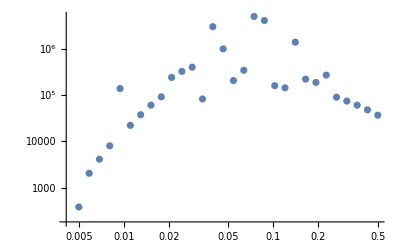

```mathematica
ListLogLogPlot[Abs[computeB411red]]
```

```mathematica
int1=NIntegrate[q^2/(2π)^3 t4p1/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-5,50},(*MaxPoints->200000,*)PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.28322×10^6 and 102366. for the integral and error estimates.

3.28322×10^6

```mathematica
int2=NIntegrate[q^2/(2π)^3 t4p2/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-3,50},(*MaxPoints->200000,*)PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.69119×10^7 and 133299. for the integral and error estimates.

-5.69119×10^7

```mathematica
int3=NIntegrate[q^2/(2π)^3 t4p3/.Plin-> plin,{β,0,2π},{x,-1,1},{q,10^-3,50},(*MaxPoints->200000,*)PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.69009×10^7 and 133299. for the integral and error estimates.

-5.69009×10^7

```mathematica
int411=int1+int2+int3
```

-1.70714×10^8

```mathematica
ksub-ksub824
```

{0,0,0}

```mathematica
-0.021234867118799315 2
```

-0.0424697

```mathematica
-94854.02971241245-351635.51119745645-220502.23956838233
```

-666992.

```mathematica
Plin[k1]Plin[k2]σ2 ser2B411tabintfin/.Plin->plin/.bsub/.yrep/.ksub
```

-1.8311×10^6

#### Sum

```mathematica
{int222,fullint3211,fullint3212,fullint411}
```

{-1.08971×10^6,-3.06388×10^7,-2.07271×10^6,-2.01441×10^10}

```mathematica
{int222,fullint3211,fullint3212,fullint411}//Total
```

-2.01779×10^10

## Check J functions

```mathematica
kBins[Nmax_,kmin_,kmax_]:=Module[{Δ,result},
Δ=1/(Nmax-1)Log[kmax/kmin]//N;
result=Table[kmin Exp[(i-1) Δ],{i,1,Nmax}];
result
];
```

```mathematica
knFit=kBins[100,10^-3,0.4];
```

```mathematica
Ptab = Table[{knFit⟦i⟧,plin[knFit⟦i⟧]},{i,1,Length[knFit]}];
```

```mathematica
imax=3;
ClearAll[kuv1,kuv2,kuv3,kpeak1,kpeak2,kpeak3,kpeak4,kuv4,nlm,Pinteger]
kuv1=0.069;
kuv2=0.0082;
kuv3=0.0013;
kuv4=0.0000135;
kpeak1=-0.034;
kpeak2=-0.001;
kpeak3=-0.000076;
kpeak4=-0.0000156;
Parameters=Flatten[Table[{a1[i],a2[i],a3[i],a4[i]},{i,0,imax}]];

MyFitFunctions=Flatten[Table[{ 1/((1+((k^2-kpeak1)^2)/kuv1^2)^(i)), (k/(1/20))^2/((1+((k^2-kpeak2)^2)/kuv2^2)^(i+1)),1/((1+((k^2-kpeak3)^2)/kuv3^2)^(i+2)),1/((1+((k^2-kpeak4)^2)/kuv4^2)^(i+1))},{i,0,imax}]];
nlm=LinearModelFit[Ptab,MyFitFunctions(*,Parameters*),k,Weights->1/((10^-6 Ptab⟦All,2⟧)^2),IncludeConstantBasis->False]; 
Myparametersconstraint=Flatten[{{0.04≤kuv1≤ 0.15,0.00002≤kuv2≤0.0004,0.0085≤ kuv3≤0.017,0.000008≤ kuv4≤0.000052,-0.073≤kpeak1≤-0.0003,-0.0001≤kpeak2≤-0.000035,-0.0058≤kpeak3≤-0.0003,-0.00005≤kpeak4≤-0.0000029}}];
Pinteger[k_]=nlm[k];
LogLogPlot[{Abs[Pinteger[k]/plin[k]-1],Abs[plin[k]/Pinteger[k]-1],0.1,0.005,0.01,0.02,0.05},{k,0.001,2.},PlotRange-> All,PlotLabel->"imax="<>ToString[imax]]
LogLogPlot[{Pinteger[k],plin[k]},{k,0.0005,0.5},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
nlm//Normal
```

-436.077+340740./((1+5.48697×10^9 (0.0000156+k^2)^2)^4)-506731./((1+5.48697×10^9 (0.0000156+k^2)^2)^3)+235864./((1+5.48697×10^9 (0.0000156+k^2)^2)^2)-60307.2/(1+5.48697×10^9 (0.0000156+k^2)^2)-203147./((1+591716. (0.000076+k^2)^2)^5)+535845./((1+591716. (0.000076+k^2)^2)^4)-508904./((1+591716. (0.000076+k^2)^2)^3)+204335./((1+591716. (0.000076+k^2)^2)^2)+(4.49831×10^6 k^2)/((1+14872.1 (0.001+k^2)^2)^4)+(4.32028×10^6 k^2)/((1+14872.1 (0.001+k^2)^2)^3)-(2.84454×10^6 k^2)/((1+14872.1 (0.001+k^2)^2)^2)+(4.50859×10^6 k^2)/(1+14872.1 (0.001+k^2)^2)-28591.9/((1+210.04 (0.034+k^2)^2)^3)+13133.4/((1+210.04 (0.034+k^2)^2)^2)-11266.1/(1+210.04 (0.034+k^2)^2)

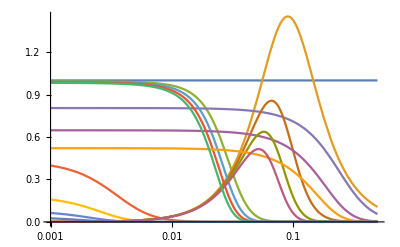

```mathematica
LogLinearPlot[MyFitFunctions,{k,10^-3,0.5}]
```

```mathematica
Limit[#,k->0]&/@MyFitFunctions
```

{1,0.,0.993199,0.428209,0.804631,0.,0.989816,0.183363,0.647431,0.,0.986445,0.0785176,0.520943,0.,0.983085,0.0336219}

```mathematica
Limit[#,k->∞]&/@MyFitFunctions
```

{1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ksub0=Thread[{k1,k2,k3}->{0.017221,0.017221,0.017221}];
ksub20=Thread[{k1,k2,k3}->{0.027562,0.027562,0.027562}];
ksub29=Thread[{k1,k2,k3}->{0.081,0.070261,0.027562}];
ksub124=Thread[{k1,k2,k3}->{0.091757,0.091757,0.048836}];
ksub130=Thread[{k1,k2,k3}->{0.124006,0.102501,0.048836}];
ksub181=Thread[{k1,k2,k3}->{0.091757,0.081,0.059539}];
ksub250=Thread[{k1,k2,k3}->{0.124006,0.081,0.070261}];
ksub655=Thread[{k1,k2,k3}->{0.210114,0.199356,0.124006}];
ksub824=Thread[{k1,k2,k3}->{0.220892,0.220892,0.220892}];
ksubren=Thread[{k1,k2,k3}->{0.001,0.001,0.001}];
ksub=ksub0
```

{k1→0.017221,k2→0.017221,k3→0.017221}

```mathematica
magrevreps={k1mq->√(k1^2+q^2-2 k1 q x),k1pq->√(k1^2+q^2+2 k1 q x),k2mq->√(k2^2+q^2-2 k2 q (x y+√(1-x^2) √(1-y^2) Sin[β])),k2pq->√(k2^2+q^2+2 k2 q (x y+√(1-x^2) √(1-y^2) Sin[β])),k3mq->√(k3^2+q^2+2 k1 q x+2 k2 q x y+2 k2 q √(1-x^2) √(1-y^2) Sin[β]),k3pq->√(k3^2+q^2-2 k1 q x-2 k2 q x y-2 k2 q √(1-x^2) √(1-y^2) Sin[β]),qmq1->√(q^2+q1^2-2 q q1 ν),qpq1->√(q^2+q1^2+2 q q1 ν)};
```

```mathematica
NumJreg[n1_,n2_,n3_,d1_,d2_,d3_,k1_,k2_,k3_]:=Module[{normk1pq,normk2mq,integrand,integrandIR,integrandIReven,integrandUV,integrandUVeven,integralIR,integralUV},
normk1pq=k1^2+q^2+2 k1 q ν;
normk2mq=k2^2+q^2+k1 q ν+((k2^2-k3^2) q ν)/k1-(√(-k1^4-(k2^2-k3^2)^2+2 k1^2 (k2^2+k3^2)) q √(1-ν^2) Sin[ϕ])/k1//Simplify;
integrand=q^(2(1-n1)) (normk1pq)^-n2(normk2mq)^-n3 fdiogotabfn[q]⟦d1⟧fdiogotabfn[√normk1pq]⟦d2⟧fdiogotabfn[√normk2mq]⟦d3⟧;
Print[integrand];
integrandIR=Normal[Series[integrand,{q,0,-1},Assumptions->{-1<ν<1,0<ϕ<2π,q>0,k1>0,k2>0,k3>0}]];
integrandUV=Normal[Series[integrand,{q,∞,0},Assumptions->{-1<ν<1,0<ϕ<2π,q>0,k1>0,k2>0,k3>0}]];
Print[integrandIR];
Print[integrandUV];
regintegrand=Simplify[integrand-integrandIR-integrandUV,Assumptions->{q>0,-1<ν<1,0<ϕ<2π}];
(*Print[regintegrand];*)
(*Print["After Simplify"];*)
(1/(2π)^3)NIntegrate[regintegrand,{q,1/10000,100},{ν,-1,1},{ϕ,0,2π},PrecisionGoal->10,(*WorkingPrecision->20,*)(*MaxRecursion->100,*)Method->{"GlobalAdaptive","SymbolicProcessing"->0}]
];
```

```mathematica
k1val=Rationalize[0.017221];
k2val=Rationalize[0.017221];
k3val=Rationalize[0.017221];
n1=2;
n2=2;
n3=2;
NumJreg[n1,n2,n3,5,1,1,k1val,k2val,k3val]
```

Part::partw: Part 5 of fdiogotabfn[q] does not exist.

fdiogotabfn[q]⟦5⟧/(q^2 (296562841/1000000000000+q^2+(17221 q ν)/500000)^(3/2) (296562841/1000000000000+q^2+(17221 q ν)/1000000-(17221 q √(3-3 ν^2) Sin[ϕ])/1000000)^(3/2))

Part::partw: Part 5 of fdiogotabfn[0] does not exist.

(1000000000000000000000000000000000000 fdiogotabfn[0]⟦5⟧)/(26082559118982653010589321 q^2)-(1000000000000000000000000000000000000 (4500000 ν fdiogotabfn[0]⟦5⟧-1500000 √3 √(1-ν^2) fdiogotabfn[0]⟦5⟧ Sin[ϕ]-17221 fdiogotabfn'[0] Part^(1,0)[fdiogotabfn[0],5]))/(449167750588000267495358696941 q)

0

Part::partw: Part 5 of fdiogotabfn[q] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NIntegrate::inumr: The integrand (1000000000000000000000000000000000000 (fdiogotabfn[0]⟦5⟧ («1»)+17221 («1»)))/(449167750588000267495358696941 q^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/10000,100},{-1,1},{0,6.28319}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

1/(8 π^3)NIntegrate[regintegrand,{q,1/10000,100},{ν,-1,1},{ϕ,0,2 π},PrecisionGoal→10,Method→{GlobalAdaptive,SymbolicProcessing→0}]

Check J’s new in redshift space, that are high (looked for in Python)

```mathematica
Clear[n1,n2,n3]
```

```mathematica
inttest=q^(-2 n1)k1pq^(-2 n2)k2mq^(-2 n3)(MyFitFunctions⟦1⟧/.k->q)(MyFitFunctions⟦1⟧/.k->k1pq)(MyFitFunctions⟦1⟧/.k->k2mq)/.{n1->2,n2->1,n3->0}/.magrevreps
```

((k1^2+q^2+2 k1 q x)^4)/q^2

```mathematica
inttestx=Integrate[1/2((k1^2+q^2+2 k1 q x)^4)/q^2,{x,-1,1}]
```

12 k1^6+k1^8/q^2+(126 k1^4 q^2)/5+12 k1^2 q^4+q^6

```mathematica
Series[inttestx MyFitFunctions⟦1+4⟧/.k->q,{q,∞,4}]//Normal
```

-0.000323748+0.057132 k1^2+(2.33422×10^-6-0.0000738717 k1^2-0.00815845 k1^4+0.057132 k1^6)/q^4+(-6.15597×10^-6-0.00388498 k1^2+0.119977 k1^4)/q^2+0.004761 q^2

```mathematica
seruv=Series[inttest,{q,∞,0}]//Normal
```

q^6+8 k1 q^5 x+16 k1^6 x^2+2 k1^4 (2 k1^2+4 k1^2 x^2)+q^4 (4 k1^2+24 k1^2 x^2)+q^3 (8 k1^3 x+8 k1 x (2 k1^2+4 k1^2 x^2))+q (8 k1^5 x+8 k1^3 x (2 k1^2+4 k1^2 x^2))+q^2 (2 k1^4+32 k1^4 x^2+(2 k1^2+4 k1^2 x^2)^2)

```mathematica
restest=NIntegrate[q^2/(2π)^3(inttest-seruv)/.ksub,{β,0,2π},{x,-1,1},{q,10^-6,100}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.137312 and 0.593542 for the integral and error estimates.

-0.137312

UV integrand. But we have to subtract also the subleading divergence

```mathematica
intuv=q^(-2 n1)k1pq^(-2 n2)k2mq^(-2 n3)(MyFitFunctions⟦1+4⟧/.k->q)(MyFitFunctions⟦1⟧/.k->k1pq)(MyFitFunctions⟦1⟧/.k->k2mq)/.{n1->-2,n2->0,n3->0}/.magrevreps/.yrep
```

q^4/(1+210.04 (0.034+q^2)^2)

```mathematica
intuv2=(12 k1^2 q^2+q^4)(MyFitFunctions⟦1+4⟧/.k->q)(MyFitFunctions⟦1⟧/.k->k1pq)(MyFitFunctions⟦1⟧/.k->k2mq)/.{n1->-2,n2->0,n3->0}/.magrevreps/.yrep
```

(12 k1^2 q^2+q^4)/(1+210.04 (0.034+q^2)^2)

```mathematica
Series[inttest-intuv2,{q,∞,2}]//Normal
```

(0.038088 k1 x)/q+(0.114264 (-0.333333 k1^2+1. k1^2 x^2))/q^2

```mathematica
seruv=Series[inttest,{q,∞,2}]//Normal
```

0.004761+(0.038088 k1 x)/q+(0.114264 (-0.00283333+0.166667 k1^2+1. k1^2 x^2))/q^2

```mathematica
serir=Series[inttest,{q,0,-4}]//Normal
```

(0.804631 k1^8)/q^4

```mathematica
(*inttest1=Integrate[inttest,{β,0,2π}]*)
```

```mathematica
(*inttest2=FullSimplify[1/(2π)inttest1/.ksub]//FullSimplify*)
```

```mathematica
ser1=Series[inttest,{q,0,-4}]//Normal
```

(0.804631 k1^8)/q^4

```mathematica
intir=Integrate[q^2/(2π)^3 ser1,{q,10^-5,10^-4},{x,-1,1},{β,0,2π}]
```

3668.68 k1^8

```mathematica
ser2=Series[inttest,{q,∞,2}]//Normal
```

0.004761+(0.038088 k1 x)/q+(0.114264 (-0.00283333+0.166667 k1^2+1. k1^2 x^2))/q^2

```mathematica
intuv=Integrate[q^2/(2π)^3 ser2,{q,1,10},{x,-1,1},{β,0,2π}]
```

0.0801703+0.0260491 k1^2

```mathematica
Series[inttest-intuv2,{q,∞,2}]//Simplify
```

0.028566+(0.114264 k1 x)/q+(-0.00194249+0.114264 k1^2 x^2)/q^2+O[1/q]^3

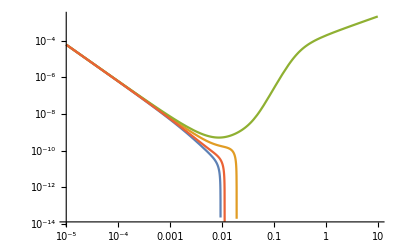

```mathematica
LogLogPlot[Evaluate[{q^2(inttest-intuv2)/.ksub/.{β->π/4,x->-1/2,μ->1/2,ϕ->0},q^2(inttest-intuv2)/.ksub/.{β->-π/2,x->0,μ->0,ϕ->π/2},q^2(inttest-intuv2)/.ksub/.{β->(3 π)/2,x->1/3,μ->1,ϕ->π/3},q^2(inttest-intuv2)/.ksub/.{β->(2 π)/3,x->-1/3,μ->0,ϕ->π}}/.Plin->plin],{q,10^-5,10},PlotRange->All]
```

```mathematica
restest=NIntegrate[q^2/(2π)^3(inttest-serir-seruv)/.ksub,{β,0,2π},{x,-1,1},{q,10^-5,10}]
```

2.79113×10^-6

```mathematica
restest-intir-intuv2/.ksub
```

0.0802457-(3 q^4+4 q^2 (0.000889689-2 (0.000296563+q^2+0.034442 q x)))/(1+210.04 (0.034+q^2)^2)

```mathematica
intnew[n1_,n2_,n3_]=Evaluate[q^(-2 n1)k1pq^(-2 n2)k2mq^(-2 n3)(MyFitFunctions⟦15⟧/.k->q)/.magrevreps/.yrep];
```

```mathematica
nb=64;
```

```mathematica
pos1=Position[ctest⟦nb,All,656,1⟧,1.]//Flatten;
posc=Position[ctest⟦nb,All,656,5⟧,_?(#≠0.&)]//Flatten;
posx=Intersection[pos1,posc]
```

{111,113,114,121,123,126,135,137,145,154}

```mathematica
intlist=intnew[ctest⟦nb,posx,656,2⟧,ctest⟦nb,posx,656,3⟧,ctest⟦nb,posx,656,4⟧]/.ksub;
```

```mathematica
seruv=Table[Series[intlist⟦i⟧/.ksub,{q,∞,2}]//Normal,{i,1,Length[intlist]}]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
serir=Table[Series[q^4 intlist⟦i⟧/.ksub,{q,0,0}]/.q->0//Normal,{i,1,Length[intlist]}]
```

{0.983085,0.0434011,0.00191607,0.0390706,0.00172488,0.00155277,0.,0.,0.,0}

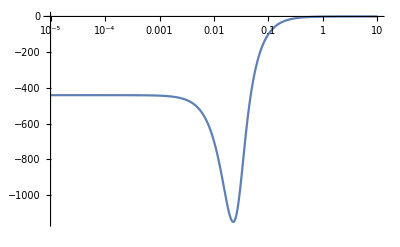

```mathematica
LogLinearPlot[Evaluate[{q^2(intlist⟦1⟧-serir⟦1⟧/q^4)/.ksub/.{β->π/4,x->-1/2}}],{q,10^-5,10}]
```

```mathematica
Table[NIntegrate[q^2/(2π)^3(intlist⟦i⟧-serir⟦i⟧/q^4)/.ksub,{β,0,2π},{x,-1,1},{q,10^-5,10}],{i,1,Length[intlist]}]
```

{-2.93468,-0.128521,-0.00556664,-0.115593,-0.0050142,-0.00449741,0.00103934,0.0000460944,0.000041516,2.09581×10^-7}

```mathematica
intnew[n1_,n2_,n3_]=Evaluate[q^(-2 n1)k1pq^(-2 n2)k2mq^(-2 n3)(MyFitFunctions⟦1+8⟧/.k->q)/.magrevreps/.yrep];
```

```mathematica
Series[intnew[2,2,-4],{q,∞,8}]
```

0.0000226671/q^8+O[1/q]^9

```mathematica
serir=Series[intnew[2,2,-4],{q,0,-3}]//Normal
```

(0.647431 k2^8)/(k1^4 q^4)+1/(k1^5 q^3)2.58972 (1. k1^2 k2^6 x-1. k2^6 k3^2 x-2. k1 k2^7 √(1-((-k1^2-k2^2+k3^2)^2)/(4 k1^2 k2^2)) √(1-x^2) Sin[β])

```mathematica
NIntegrate[q^2/(2π)^3(intnew[2,2,-4]-serir)/.ksub,{β,0,2π},{x,-1,1},{q,10^-5,10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in q near {β,x,q} = {2.89674,-0.99999999995875547865993083437065543843387624856761108915748081927,0.017221000490902135635310842440452605326929317980682182488835978511}. NIntegrate obtained 0.00485578 and 9.21965×10^-9 for the integral and error estimates.

0.00485578

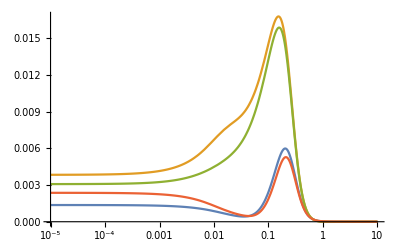

```mathematica
LogLinearPlot[Evaluate[{q^2(intnew[2,2,-4]-serir)/.ksub/.{β->π/4,x->-1/2,μ->1/2,ϕ->0},q^2(intnew[2,2,-4]-serir)/.ksub/.{β->-π/2,x->0,μ->0,ϕ->π/2},q^2(intnew[2,2,-4]-serir)/.ksub/.{β->(3 π)/2,x->1/3,μ->1,ϕ->π/3},q^2(intnew[2,2,-4]-serir)/.ksub/.{β->(2 π)/3,x->-1/3,μ->0,ϕ->π}}/.Plin->plin],{q,10^-5,10},PlotRange->All]
```

```mathematica
intirsafe[n1_,n2_,n3_]=Evaluate[q^(-2 n1)k1pq^(-2 n2)k2mq^(-2 n3)(MyFitFunctions⟦1+4⟧/.k->q)(MyFitFunctions⟦1+4⟧/.k->k1pq)/.magrevreps/.yrep];
```

```mathematica
Series[intirsafe[2,2,-4],{q,∞,8}]
```

0.0000226671/q^8+O[1/q]^9

```mathematica
serir=Series[intirsafe[2,2,-4],{q,0,-3}]//Normal
```

(0.804631 k2^8)/(k1^4 (1+210.04 (0.034+k1^2)^2) q^4)+1/q^3(k2^8 (-(3.21852 x)/(k1^5 (1+210.04 (0.034+k1^2)^2))-(0.0153234 (0.034 k1 x+1. k1^3 x))/(k1^4 (0.005917+0.068 k1^2+1. k1^4)^2))+(3.21852 k2^6 (k1^2 x+k2^2 x-k3^2 x-2 k1 k2 √(1-((-k1^2-k2^2+k3^2)^2)/(4 k1^2 k2^2)) √(1-x^2) Sin[β]))/(k1^5 (1+210.04 (0.034+k1^2)^2)))

```mathematica
k1pq/.magrevreps/.ksub
```

√(0.000296563+q^2+0.034442 q x)

```mathematica
NIntegrate[q^2/(2π)^3(2 intirsafe[2,2,-4] HeavisideTheta[k1pq-q])/.magrevreps/.ksub,{β,0,2π},{x,-1,1},{q,10^-5,100},PrecisionGoal->10,MaxPoints->200000,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 200003 integrand evaluations. NIntegrate obtained 0.000704136 and 4.83307×10^-6 for the integral and error estimates.

0.000704136

```mathematica
NIntegrate[q^2/(2π)^3 ser/.ksub,{β,0,2π},{x,-1,1},{q,10^-10,100},PrecisionGoal->10,MaxPoints->200000,Method->{Automatic,"SymbolicProcessing"->0}]
```

0.0241195

```mathematica
NIntegrate[q^2/(2π)^3(intirsafe[2,2,-4])/.magrevreps/.ksub,{β,0,2π},{x,-1,1},{q,10^-5,100},PrecisionGoal->3,MaxPoints->200000,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.000435914

```mathematica
NIntegrate[q^2/(2π)^3(serir)/.magrevreps/.ksub,{β,0,2π},{x,-1,1},{q,10^-10,0.001},PrecisionGoal->3,MaxPoints->200000,Method->{Automatic,"SymbolicProcessing"->0}]
```

28.7485

```mathematica
28.749796830196683-28.748467362777017
```

0.00132947

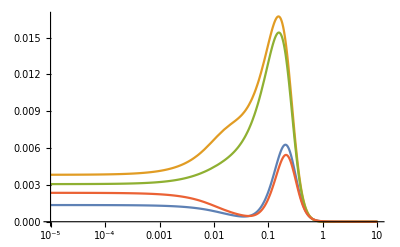

```mathematica
LogLinearPlot[Evaluate[{q^2(intirsafe[2,2,-4]-serir)/.ksub/.{β->π/4,x->-1/2,μ->1/2,ϕ->0},q^2(intirsafe[2,2,-4]-serir)/.ksub/.{β->-π/2,x->0,μ->0,ϕ->π/2},q^2(intirsafe[2,2,-4]-serir)/.ksub/.{β->(3 π)/2,x->1/3,μ->1,ϕ->π/3},q^2(intirsafe[2,2,-4]-serir)/.ksub/.{β->(2 π)/3,x->-1/3,μ->0,ϕ->π}}/.Plin->plin],{q,10^-5,10},PlotRange->All]
```

## Check J functions from Diogo

```mathematica
imax=3;
```

```mathematica
fdiogotab=Flatten[Table[{ 1/((1+((k^2-kpeak1)^2)/kuv1^2)^(i)), (k^2/(1/20)^2)/((1+((k^2-kpeak2)^2)/kuv2^2)^(i+1)),1/((1+((k^2-kpeak3)^2)/kuv3^2)^(i+2)),1/((1+((k^2-kpeak4)^2)/kuv4^2)^(i+1))},{i,0,imax}]]/.{kuv1->0.069,kuv2->0.0082,kuv3->0.0013,kuv4->0.0000135,kpeak1->-0.034,kpeak2->-0.001,kpeak3->-0.000076,kpeak4->-0.0000156};
```

```mathematica
fdiogotabfn[k_]=Rationalize[fdiogotab];
```

```mathematica
NumJreg[n1_,n2_,n3_,d1_,d2_,d3_,k1_,k2_,k3_]:=Module[{k1vec,k2vec,k3vec,qvec,k1mqvec,normk1mq,k2pqvec,k2mqvec,normk2pq,normk2mq,k3pqvec,normk3pq,ν2, integrand,integrandIR,integrandIReven,integrandUV,integrandUVeven,integralIR,integralUV},
k1vec=k1{0,0,1};
ν2=(1/(2k1 k2))(k3^2-k2^2-k1^2);
k2vec=k2{0,√(1-ν2^2),ν2};
k3vec=-k1vec-k2vec;
qvec=q{Cos[ϕ]√(1-ν^2),Sin[ϕ]√(1-ν^2),ν};
k1mqvec={-q √(1-ν^2) Cos[ϕ],-q √(1-ν^2) Sin[ϕ],k1-q ν}(*k1vec-qvec//Simplify*);
k2pqvec={q √(1-ν^2) Cos[ϕ],k2 √(1-((k1^2+k2^2-k3^2)^2)/(4 k1^2 k2^2))+q √(1-ν^2) Sin[ϕ],-(k1^2+k2^2-k3^2)/(2 k1)+q ν}(*k2vec+qvec//Simplify*);
k2mqvec=k2vec-qvec//Simplify;
k3pqvec={q √(1-ν^2) Cos[ϕ],-k2 √(1-((k1^2+k2^2-k3^2)^2)/(4 k1^2 k2^2))+q √(1-ν^2) Sin[ϕ],-(k1^2-k2^2+k3^2)/(2 k1)+q ν}(*k3vec+qvec//Simplify*);
normk1mq=k1^2+q^2-2 k1 q ν(*k1mqvec.k1mqvec//Simplify*);
normk2pq=1/k1(k1 (k2^2+q^2)-(k1^2+k2^2-k3^2) q ν+q √((k1-k2-k3) (k1+k2-k3) (k1-k2+k3) (k1+k2+k3) (-1+ν^2)) Sin[ϕ])//Simplify(*k2pqvec.k2pqvec//Simplify*);
normk2mq=k2^2+q^2+k1 q ν+((k2^2-k3^2) q ν)/k1-k2 √(-1/(k1^2 k2^2)(k1^4+(k2^2-k3^2)^2-2 k1^2 (k2^2+k3^2))) q √(1-ν^2) Sin[ϕ]//Simplify(*k2mqvec.k2mqvec//Simplify*);
normk3pq=1/k1(k1 (k3^2+q^2)-(k1^2-k2^2+k3^2) q ν-q √((k1-k2-k3) (k1+k2-k3) (k1-k2+k3) (k1+k2+k3) (-1+ν^2)) Sin[ϕ])//Simplify(*k3pqvec.k3pqvec//Simplify*);


If[n2>1&&n1≤1&&n3≤1,
(*Do change of variable q -> k1-q*)
integrand=q^(2(1-n2)) (normk1mq)^-n1(normk3pq)^-n3 fdiogotabfn[√normk1mq]⟦d1⟧fdiogotabfn[q]⟦d2⟧fdiogotabfn[√normk3pq]⟦d3⟧,

If[n3>1&&n1≤1&&n2≤1,
(*Do change of variable qnew = k2+q*)
integrand=q^(2(1-n3)) (normk3pq)^-n2(normk2mq)^-n1 fdiogotabfn[√normk2mq]⟦d1⟧fdiogotabfn[√normk3pq]⟦d2⟧fdiogotabfn[q]⟦d3⟧,
integrand=q^(2(1-n1)) (normk1mq)^-n2(normk2pq)^-n3 fdiogotabfn[q]⟦d1⟧fdiogotabfn[√normk1mq]⟦d2⟧fdiogotabfn[√normk2pq]⟦d3⟧]
];
(*Print[integrand];*)
integrandIR=Normal[Series[integrand,{q,0,-1},Assumptions->{-1<ν<1,0<ϕ<2π,q>0,k1>0,k2>0,k3>0}]];
integrandUV=Normal[Series[integrand,{q,∞,0},Assumptions->{-1<ν<1,0<ϕ<2π,q>0,k1>0,k2>0,k3>0}]];
(*Print[integrandIR];
Print[integrandUV];*)
integrandIReven=If[integrandIR=!=0,Select[integrandIR,EvenQ[Exponent[#,q]]&],0];
integrandUVeven=If[integrandUV=!=0,Select[integrandUV,EvenQ[Exponent[#,q]]&],0];
regintegrand=Simplify[integrand-integrandIR-integrandUV,Assumptions->{q>0,-1<ν<1,0<ϕ<2π}];
(*Print[regintegrand];*)
(*Print["After Simplify"];*)
(1/(2π)^3)NIntegrate[regintegrand,{q,10^-4,100},{ν,-1,1},{ϕ,0,2π},PrecisionGoal->6,(*WorkingPrecision->20,*)(*MaxRecursion->100,*)Method->{"GlobalAdaptive","SymbolicProcessing"->0}]
];
```

```mathematica
,0.188592,0.027562
```

```mathematica
(*k1val=Rationalize[0.017221];
k2val=Rationalize[0.017221];
k3val=Rationalize[0.017221];*)
k1val=Rationalize[0.188592];
k2val=Rationalize[0.188592];
k3val=Rationalize[0.027562];
```

```mathematica
NumJreg[2,1,2,6,1,1,k3val,k1val,k2val]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in q near {q,ν,ϕ} = {0.18859201369338101346709384325006775907536870908705313566382807722,0.0730731,4.71239}. NIntegrate obtained 6.48236×10^11 and 2.54724×10^11 for the integral and error estimates.

2.61332×10^9

```mathematica
NumJreg[2,2,2,1,1,1,0.001,0.001,0.001]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in q near {q,ν,ϕ} = {0.0010000001591936234361003754467688289536739093883509810643980182559,0.5,4.71239}. NIntegrate obtained 1.25855×10^35 and 7.71065×10^34 for the integral and error estimates.

5.07376×10^32

```mathematica
tab411=Import["/Users/guido/github/bisp_pybird/pybird_dev/new411.dat"]
```

{{-2,-1,2,0,0,4},{-1,1,2,0,0,3},{-3,-1,2,0,0,4},{-2,1,2,0,0,1},{-1,2,0,0,1,0},{-4,1,1,4,0,0},{-3,1,1,4,0,0},{1,2,-1,0,3,0},{0,2,-1,0,1,0},{1,2,0,0,3,0},{0,2,1,0,3,0},{-4,0,2,0,0,4},{-3,1,2,0,0,4},{-2,2,1,0,1,0},{-3,0,2,0,0,4},{1,2,-2,0,1,0},{-1,2,1,0,3,0},{-1,-3,2,0,0,4},{1,-1,2,0,0,3},{-1,-2,2,0,0,4},{1,0,2,0,0,3},{1,-2,2,0,0,1},{0,-4,2,0,0,4},{0,-3,2,0,0,4},{0,2,0,0,3,0},{2,0,-4,4,0,0},{-3,1,1,0,0,4},{2,-4,0,4,0,0},{-2,-2,2,0,0,4},{-4,1,1,0,0,4}}

```mathematica
k1val=Rationalize[0.017221];
k2val=Rationalize[0.017221];
k3val=Rationalize[0.017221];
(*n1=1;
n2=-4;
n3=0;
NumJreg[n1,n2,n3,5,1,1,k1val,k2val,k3val]*)
```

```mathematica
idx=30;
For[i=16,i≥1,i--,
Print[tab411⟦idx,;;3⟧,{0,0,i-1}];
Print[NumJreg[tab411⟦idx,1⟧,tab411⟦idx,2⟧,tab411⟦idx,3⟧,1,1,i,k1val,k2val,k3val]]]
```

{-4,1,1}{0,0,15}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in q near {q,ν,ϕ} = {0.017221001635134187608436738069398896059653798682828359045384414159,0.5,4.71239}. NIntegrate obtained 1.9587×10^-14 and 2.25757×10^-19 for the integral and error estimates.

7.89639×10^-17

{-4,1,1}{0,0,14}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

6.32185×10^-13

{-4,1,1}{0,0,13}

3.22456×10^-10

{-4,1,1}{0,0,12}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

1.4416×10^-7

{-4,1,1}{0,0,11}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in q near {q,ν,ϕ} = {0.017221001635134187608436738069398896059653798682828359045384414159,0.5,4.71239}. NIntegrate obtained 5.47119×10^-14 and 5.69579×10^-19 for the integral and error estimates.

2.20568×10^-16

{-4,1,1}{0,0,10}

9.12514×10^-13

{-4,1,1}{0,0,9}

1.35551×10^-9

{-4,1,1}{0,0,8}

2.59219×10^-6

{-4,1,1}{0,0,7}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in q near {q,ν,ϕ} = {0.017221001635134187608436738069398896059653798682828359045384414159,0.5,4.71239}. NIntegrate obtained 1.70953×10^-13 and 1.5317×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

6.89189×10^-16

{-4,1,1}{0,0,6}

1.59892×10^-12

{-4,1,1}{0,0,5}

Select::normal: Nonatomic expression expected at position 1 in Select[2825761/1562500000000,EvenQ[Exponent[#1,q]]&].

-1.20939×10^-8

{-4,1,1}{0,0,4}

2.83628×10^-6

{-4,1,1}{0,0,3}

3.59914×10^-15

{-4,1,1}{0,0,2}

6.15857×10^-12

{-4,1,1}{0,0,1}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.51143×10^-6 and 7.70828×10^-8 for the integral and error estimates.

1.01247×10^-8

{-4,1,1}{0,0,0}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.02399×10^-12 and 1.11762×10^-15 for the integral and error estimates.

-1.62225×10^-14

```mathematica
tab3211=Import["/Users/guido/github/bisp_pybird/pybird_dev/new3211.dat"]
```

{{1,-3,1,4,0,0},{2,-4,2,0,0,3},{2,-3,2,1,0,0},{-3,1,1,4,0,0},{-4,1,2,0,0,4},{2,-3,0,0,0,4},{0,-3,2,4,0,0},{1,-3,2,0,0,4},{2,-4,1,0,0,4},{2,0,-3,0,0,4},{2,-3,1,4,0,0},{-3,1,2,0,0,4},{1,-4,2,4,0,0}}

```mathematica
idx=9;
For[i=16,i≥1,i--,
For[j=16,j≥1,j--,
Print[tab3211⟦idx,;;3⟧,{i-1,0,j-1}];
Print[NumJreg[tab3211⟦idx,1⟧,tab3211⟦idx,2⟧,tab3211⟦idx,3⟧,i,1,j,k1val,k2val,k3val]]]]
```

{2,-4,1}{15,0,15}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-3.82241×10^-22

{2,-4,1}{15,0,14}

-2.63785×10^-11

{2,-4,1}{15,0,13}

-4.11229×10^-12

{2,-4,1}{15,0,12}

-2.00057×10^-11

{2,-4,1}{15,0,11}

-2.32013×10^-19

{2,-4,1}{15,0,10}

-2.85012×10^-11

{2,-4,1}{15,0,9}

-4.21396×10^-12

{2,-4,1}{15,0,8}

-2.49471×10^-11

{2,-4,1}{15,0,7}

-1.32327×10^-16

{2,-4,1}{15,0,6}

-3.07908×10^-11

{2,-4,1}{15,0,5}

-4.31814×10^-12

{2,-4,1}{15,0,4}

-3.1109×10^-11

{2,-4,1}{15,0,3}

-7.2773×10^-14

{2,-4,1}{15,0,2}

-3.326×10^-11

{2,-4,1}{15,0,1}

-4.42488×10^-12

{2,-4,1}{15,0,0}

-3.87928×10^-11

{2,-4,1}{14,0,15}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in q near {q,ν,ϕ} = {0.017221001635134187608436738069398896059653798682828359045384414159,0.5,4.71239}. NIntegrate obtained 4.40556×10^-11 and 5.10172×10^-16 for the integral and error estimates.

1.77607×10^-13

{2,-4,1}{14,0,14}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

5.754×10^-10

{2,-4,1}{14,0,13}

3.74709×10^-10

{2,-4,1}{14,0,12}

$Aborted

```mathematica
tab222=Import["/Users/guido/github/bisp_pybird/pybird_dev/new222.dat"]
```

{{1,2,-3,0,4,0},{2,1,-3,4,0,0},{2,2,-4,3,0,0},{2,-4,2,0,0,3},{2,-3,2,0,1,0},{-4,2,2,0,0,3},{-3,2,2,1,0,0},{1,-3,2,0,0,4},{2,-3,1,4,0,0},{2,2,-3,0,0,1},{-3,1,2,0,0,4},{-3,2,1,0,4,0}}

```mathematica
idx=6;
For[i=16,i≥1,i--,
For[j=16,j≥1,j--,
For[kk=16,kk≥1,kk--,
Print[tab222⟦idx,;;3⟧,{i-1,j-1,kk-1}];
Print[NumJreg[tab222⟦idx,1⟧,tab222⟦idx,2⟧,tab222⟦idx,3⟧,i,j,kk,k1val,k2val,k3val]]]]]
```

{-4,2,2}{15,15,15}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in q near {q,ν,ϕ} = {0.017221001635134187608436738069398896059653798682828359045384414159,0.5,4.71239}. NIntegrate obtained 3.35353×10^-21 and 3.6852×10^-21 for the integral and error estimates.

1.35196×10^-23

{-4,2,2}{15,15,14}

$Aborted

```mathematica
NumJreg[-4,2,2,1,1,1,k1val,k2val,k3val]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in q near {q,ν,ϕ} = {0.017221001635134187608436738069398896059653798682828359045384414159,0.5,4.71239}. NIntegrate obtained 592.84 and 505.055 for the integral and error estimates.

2.39